This Mathematica Notebook can be treated as a supplemental material with the article “Cooling through parametric modulations and phase-preserving quantum measurements” by Sreenath K. Manikandan and Sofia Qvarfort. It contains the relevant numerical simulations and resultant data in list/table form, which were used to make plots in the article.

Notebook author: Sreenath K. Manikandan, Nordita
Stockholm University and KTH Royal Institute of Technology
Hannes Alfvéns väg 12, SE-106 91 Stockholm, Sweden

## Correspondence to parameters used in the draft.

Note that the mathematica notebook uses different symbols compared to the manuscript. They are summarized here: w0 = ω_0, wd = ω_(p,) dt = dt, d2 = dw = λ, gh^2 = γ,  nhh = n_h, phi = ϕ_p, xa = x, pa = p, nt, nta = n̄, sxxa = σ_xx, sxpa = σ_xp, sppa = σ_pp.

## 1. Cooling with dissipation, and individual quantum trajectory of cooling.

```mathematica
Cooling with dissipation, numerical simulations. The value of parameter "gh" is changed in each run of the simulation to generate different degree of dissipation, with gh=0 implying no dissipation. The measurement is modeled by sampling according to the Husimi Q function of the final state at the end of the drive. We use the mean quanta in this state, and in simulations we assume that a feedback rotates the state after measurement to <p> = 0, such that the phase of the drive (phi in the simulations) can be taken to be pi/2 for every subsequent cycle.
```

```mathematica
avg={};
w0=1;dt=0.001Pi;dw=0.01 w0;
wd=2w0 ;No=80;
lambda={{1/Sqrt[2],1/Sqrt[2]},{-I/Sqrt[2],I/Sqrt[2]}};D2[t_] = d2 Cos[ωd t + ϕd] /.ωd-> 2;P11[t_] = Exp[- d2 t]((Exp[ 2 d2 t]- 1)(Sin[t + ϕd] - d2 Sin[t]) + d2( Exp[2 d2 t ] + 1) Cos[t + ϕd]- (Exp[2 d2 t] + 1)Cos[t])/(2 (d2 Cos[ϕd]  - 1));
IP22[t_] = Exp[- d2 t]( (Exp[2 d2 t] - 1)Cos[t + ϕd]- (Exp[2d2 t] + 1)Sin[t])/(2 (d2 Cos[ϕd]- 1));α[t_] =(P11[t]- I IP22[t] + I D[P11[tp]- I IP22[tp],tp] /.tp-> t)/2;
β[t_] = (P11[t]+ I IP22[t] + I D[P11[tp]+ I IP22[tp],tp] /.tp-> t)/2;b[t_] = α[t] μ + β[t]Conjugate[μ];
bdb[t_] = (Abs[α[t]]^2 + Abs[β[t]]^2)Abs[μ]^2   + Conjugate[α[t]] β[t]Conjugate[μ]^2 + α[t]Conjugate[β[t]]μ^2 + Abs[β[t]]^2;
b2[t_] = α[t]^2 μ^2 + α[t]β[t](2 Abs[μ]^2 + 1) + β[t]^2 Conjugate[μ]^2;NL =30;gc=Sqrt[w0/2];gh=0Sqrt[w0/2];betac=20/w0;betah=0.1/w0;Oc=w0/5;Oh=w0/2;nc=1/(Exp[betac Oc]-1);nh=1/(Exp[betah Oh]-1);
nhh=1/(Exp[betah w0]-1);
n0=1/(Exp[betac w0]-1);gamma=gh^2;nt= nh;rpt=10000;Do[NMS=20;phi=Pi/2;wa[ta_]:=w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi]];For[nj=1,nj<NMS,nj++,mn[1]=No;sols2[nj]=NDSolve[{xa'[ta]==pa[ta]-gamma/2xa[ta],pa'[ta]==-wa[ta]^2xa[ta]-gamma/2 pa[ta],sxxa'[ta]==2sxpa[ta]- gamma sxxa[ta]+gamma (2nt+1)/(2wa[ta]),sxpa'[ta]==sppa[ta]-sxxa[ta]wa[ta]^2-gamma sxpa[ta],sppa'[ta]==-gamma sppa[ta] +gamma (2nt+1)wa[ta]/2-2sxpa[ta]wa[ta]^2,sxxa[dt IntegerPart[NL Pi/(wd dt)(nj-1)]]==(1)/(2w0),sppa[dt IntegerPart[NL Pi/(wd dt)(nj-1)]]==w0(1)/2,sxpa[dt IntegerPart[NL Pi/(wd dt)(nj-1)]]==0,xa[dt IntegerPart[NL Pi/(wd dt)(nj-1)]]==Sqrt[2*mn[nj]/w0],pa[dt IntegerPart[NL Pi/(wd dt)(nj-1)]]==0},{xa,pa,sxxa,sppa,sxpa},{ta,dt IntegerPart[NL Pi/(wd dt)(nj-1)],IntegerPart[NL Pi/(wd dt)(nj)]dt}];
Sigmaa[nj]=Chop[Inverse[{{1,I},{1,-I}}].(Conjugate[Transpose[lambda]].{{(sxxa[dt IntegerPart[NL Pi/(wd dt)nj]]/.sols2[nj])[[1]],(sxpa[dt IntegerPart[NL Pi/(wd dt)nj]]/.sols2[nj])[[1]]},{(sxpa[dt IntegerPart[NL Pi/(wd dt)nj]]/.sols2[nj])[[1]],(sppa[dt IntegerPart[NL Pi/(wd dt)nj]]/.sols2[nj])[[1]]}}.lambda+1/2({{1,0},{0,1}})).Inverse[{{1,1},{-ⅈ,ⅈ}}]];rxf[nj]=Evaluate[Sqrt[w0/2](xa[dt IntegerPart[NL Pi/(wd dt)nj]]/.sols2[nj])[[1]]];rpf[nj]=Evaluate[(pa[dt IntegerPart[NL Pi/(wd dt)nj]]/.sols2[nj])[[1]]/Sqrt[2w0]];
meanf[nj]=Evaluate[((wa[dt IntegerPart[NL Pi/(wd dt)nj]]^2(sxxa[dt IntegerPart[NL Pi/(wd dt)nj]]+xa[dt IntegerPart[NL Pi/(wd dt)nj]]^2)+(sppa[dt IntegerPart[NL Pi/(wd dt)nj]]+pa[dt IntegerPart[NL Pi/(wd dt)nj]]^2))/(2wa[dt IntegerPart[NL Pi/(wd dt)nj]])-1/2)/.sols2[nj]][[1]];
mn[nj+1]=Norm[RandomVariate[MultinormalDistribution[{rxf[nj],rpf[nj]},Sigmaa[nj]]]]^2;];AppendTo[avg,{Table[{dt IntegerPart[NL Pi nj/(wd dt)],meanf[nj]},{nj,1,NMS}]}],{k,1,rpt}]
```

```mathematica
MeanCoolg0p05=Prepend[Table[{dt IntegerPart[NL Pi nj/(wd dt)], Sum[avg[[k]][[1]][[nj]][[2]],{k,1,rpt}]/rpt},{nj,1,NMS-1}],{0,No}] (*The data is saved as a table below in order to generate the plots*)
```

```mathematica
MeanCoolg0p05={{0,80},{47.12074821119331,30.931531067349752},{94.24463801504021,13.288786938368592},{141.36852781888712,6.7592936381937125},{188.492417622734,4.388924421013502},{235.6194490192345,3.495819106715201},{282.7401972304278,3.1717392754670444},{329.8640870342747,3.0407651129433386},{376.9879768381216,2.9931934128840205},{424.1118666419685,2.9873489124223154},{471.238898038469,2.9817088877057842},{518.3596462496623,2.965500464363835},{565.4835360535092,2.9799641863217734},{612.6074258573561,2.9916048769656998},{659.731315661203,2.97317951677059},{706.85520546505,2.9579031214589864},{753.9790952688968,2.981962925248168},{801.1029850727436,3.00939161953414},{848.2268748765906,3.0097762882749466},{895.3539062730911,2.9900681204539894}};
```

```mathematica
MeanCoolg0p1=Prepend[Table[{dt IntegerPart[NL Pi nj/(wd dt)], Sum[avg[[k]][[1]][[nj]][[2]],{k,1,rpt}]/rpt},{nj,1,NMS-1}],{0,No}]
```

```mathematica
MeanCoolg0p1={{0,80},{47.12074821119331,29.545441160759726},{94.24463801504021,14.33467696923299},{141.36852781888712,9.633868178334213},{188.492417622734,8.096449198184644},{235.6194490192345,7.68737031196714},{282.7401972304278,7.588601035837868},{329.8640870342747,7.504877999208041},{376.9879768381216,7.5164287595317445},{424.1118666419685,7.524289656367191},{471.238898038469,7.50832503586753},{518.3596462496623,7.582512268668668},{565.4835360535092,7.541928547536998},{612.6074258573561,7.533251651172061},{659.731315661203,7.525947753388384},{706.85520546505,7.492945211912101},{753.9790952688968,7.488259884821178},{801.1029850727436,7.543701293702025},{848.2268748765906,7.521265753655314},{895.3539062730911,7.539294699324824}};
```

```mathematica
MeanCool=Prepend[Table[{dt IntegerPart[NL Pi nj/(wd dt)], Sum[avg[[k]][[1]][[nj]][[2]],{k,1,rpt}]/rpt},{nj,1,NMS-1}],{0,No}]
```

```mathematica
MeanCool={{0,80},{47.12074821119331,31.43995309303342},{94.24463801504021,12.87883154666074},{141.36852781888712,5.655262704958721},{188.492417622734,2.8418360237215974},{235.6194490192345,1.7263565645383558},{282.7401972304278,1.3019897022465443},{329.8640870342747,1.132583919089975},{376.9879768381216,1.0745902924114736},{424.1118666419685,1.0515576468140546},{471.238898038469,1.032858503129769},{518.3596462496623,1.0295901141672854},{565.4835360535092,1.0261211314113652},{612.6074258573561,1.0322857876808544},{659.731315661203,1.0139043228467626},{706.85520546505,1.0289943861863042},{753.9790952688968,1.0339423773490246},{801.1029850727436,1.0214407074785334},{848.2268748765906,1.0477008959814194},{895.3539062730911,1.0386215681121744}};
```

## Average cooling with dissipation rate γ=10^-2ω_0/2.

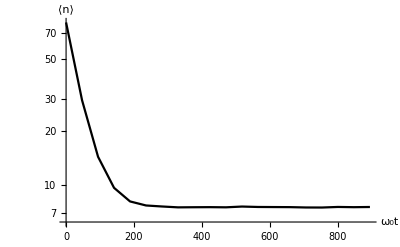

```mathematica
pg0p1=ListLogPlot[MeanCoolg0p1,PlotRange->All,Joined->True,PlotStyle->{Black},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩",Black,18]},TicksStyle->Directive[Black],PlotRange->All]
```

## Average cooling with dissipation rate γ=10^-2ω_0/8.

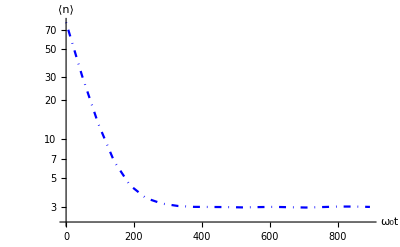

```mathematica
pg0p05=ListLogPlot[MeanCoolg0p05,PlotRange->All,Joined->True,PlotStyle->{Blue,DotDashed,PointSize[0.02]},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩",Black,18]},TicksStyle->Directive[Black],PlotRange->All]
```

## Average cooling with dissipation rate γ=0.

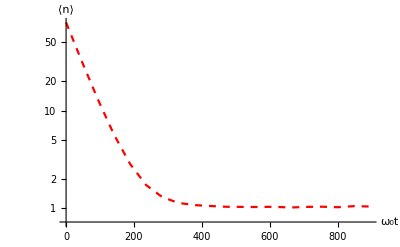

```mathematica
pg0=ListLogPlot[MeanCool,PlotRange->All,Joined->True,PlotStyle->{Red,Dashed,PointSize[0.02]},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩",Black,18]},TicksStyle->Directive[Black]]
```

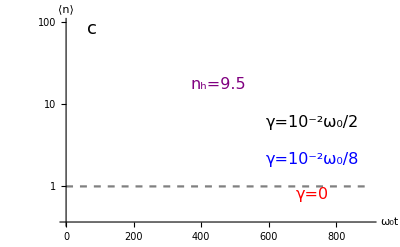

```mathematica
p51=LogPlot[1,{x,0,900},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩",Black,18]},TicksStyle->Directive[Black],PlotStyle->{Gray,Dashed},PlotRange->{{0,900},{0,100}},Epilog->{{Inset[Style["γ=10^-2ω_0/2",16],Scaled[{0.8,0.5}]]},{Inset[Style["γ=10^-2ω_0/8",16,Blue],Scaled[{0.8,0.32}]]},{Inset[Style["γ=0",16,Red],Scaled[{0.8,0.15}]]},{Inset[Style["c",18,Black],Scaled[{0.1,0.95}]]},{Inset[Style["n_h=9.5",16,Purple],Scaled[{0.5,0.68}]]}}]
```

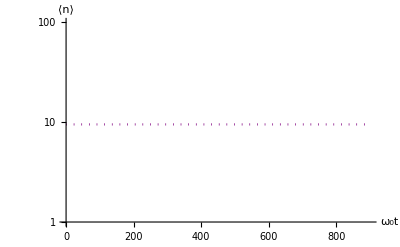

```mathematica
p52=LogPlot[nhh,{x,0,900},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩",Black,18]},TicksStyle->Directive[Black],PlotStyle->{Purple,Dotted},PlotRange->{{0,900},{0,100}}]
```

## Cooling with different degree of dissipation.

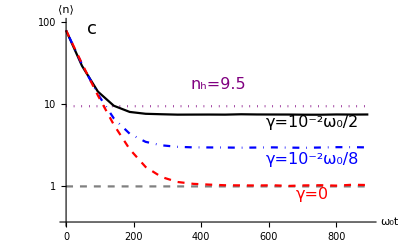

```mathematica
pbb=Show[p51,p52,pg0p1,pg0p05,pg0]
```

```mathematica
2. A single quantum trajectory of cooling with zero dissipation, starting with a coherent state of mean quanta 80. The following tables save data for initial points and final points in each cycle, and both theory and numerical comparison for the drive in between.
```

```mathematica
tabNm=Table[mn[j],{j,1,NMS}]
```

{80,30.3005,12.6608,6.84602,4.11791,4.7722,2.39183,0.465731,3.10284,2.74023,1.77516,2.6379,1.65674,0.0463327,4.06703,2.69468,4.01053,1.80247,5.0218,3.07922}

```mathematica
tabNm2=Table[{dt IntegerPart[NL Pi (nj-1)/(wd dt)],mn[nj]},{nj,1,NMS-1}]
```

{{0.,80},{47.1207,30.3005},{94.2446,12.6608},{141.369,6.84602},{188.492,4.11791},{235.619,4.7722},{282.74,2.39183},{329.864,0.465731},{376.988,3.10284},{424.112,2.74023},{471.239,1.77516},{518.36,2.6379},{565.484,1.65674},{612.607,0.0463327},{659.731,4.06703},{706.855,2.69468},{753.979,4.01053},{801.103,1.80247},{848.227,5.0218}}

```mathematica
tabNmf=Table[{dt IntegerPart[NL Pi nj/(wd dt)],meanf[nj]},{nj,1,NMS-1}]
```

{{47.1207,31.44},{94.2446,12.0523},{141.369,5.17506},{188.492,2.90801},{235.619,1.84439},{282.74,2.09948},{329.864,1.17144},{376.988,0.420497},{424.112,1.44864},{471.239,1.30727},{518.36,0.931011},{565.484,1.26737},{612.607,0.884843},{659.731,0.256982},{706.855,1.82455},{753.979,1.28951},{801.103,1.80253},{848.227,0.941659},{895.354,2.19679}}

```mathematica
sols3[nj_]:=NDSolve[{xa'[ta]==pa[ta]-gamma/2xa[ta],pa'[ta]==-wa[ta]^2xa[ta]-gamma/2 pa[ta],sxxa'[ta]==2sxpa[ta]- gamma sxxa[ta]+gamma (2nt+1)/(2wa[ta]),sxpa'[ta]==sppa[ta]-sxxa[ta]wa[ta]^2-gamma sxpa[ta],sppa'[ta]==-gamma sppa[ta] +gamma (2nt+1)wa[ta]/2-2sxpa[ta]wa[ta]^2,sxxa[dt IntegerPart[NL Pi/(wd dt)(nj-1)]]==(1)/(2w0),sppa[dt IntegerPart[NL Pi/(wd dt)(nj-1)]]==w0(1)/2,sxpa[dt IntegerPart[NL Pi/(wd dt)(nj-1)]]==0,xa[dt IntegerPart[NL Pi/(wd dt)(nj-1)]]==Sqrt[2*tabNm[[nj]]/w0],pa[dt IntegerPart[NL Pi/(wd dt)(nj-1)]]==0},{xa,pa,sxxa,sppa,sxpa},{ta,dt IntegerPart[NL Pi/(wd dt)(nj-1)],IntegerPart[NL Pi/(wd dt)(nj)]dt}]
```

```mathematica
pnds1[nj_]:=LogPlot[Evaluate[(wa[ta]^2((sxxa[ta]/.sols3[nj])+(xa[ta]/.sols3[nj])^2)+((sppa[ta]/.sols3[nj])+(pa[ta]/.sols3[nj])^2))/(2wa[ta])-1/2],{ta,dt IntegerPart[NL Pi(nj-1)/(wd dt)],dt IntegerPart[NL Pi nj/(wd dt)]},PlotRange->All,PlotStyle->{Blue,Dashed},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["t",Black,Italic,18],Style["n(t)",Black,Italic,18]},TicksStyle->Directive[Black]]
```

```mathematica
cps3=Table[ Table[{t,bdb[t-dt IntegerPart[NL Pi/(wd dt)(nj-1)]]/.{d2->0.01 w0,ϕd-> Pi/2,μ-> Sqrt[tabNm[[nj]]]}},{t,dt IntegerPart[NL Pi/(wd dt)(nj-1)],IntegerPart[NL Pi/(wd dt)(nj)]dt,dt}],{nj,1,NMS-1}];
```

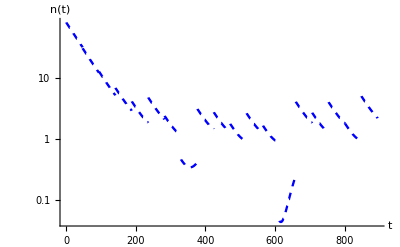

```mathematica
bz1=Show[Table[pnds1[nj],{nj,1,NMS-1}]]
```

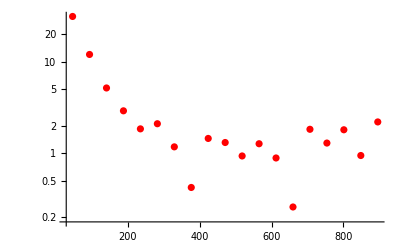

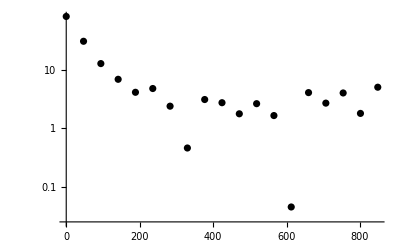

```mathematica
bz2=ListLogPlot[tabNmf,PlotStyle->Red,PlotRange->All]
bz3=ListLogPlot[tabNm2,PlotStyle->Black,PlotRange->All]
```

```mathematica
lines=Table[Line[{tabNmf[[k]],tabNm2[[k+1]]}],{k,1,Length[tabNmf]-1}](*These lines indicate the sudden changes in mean quanta due to measurements in an individual realization of the cooling process *)
```

{Line[{{47.1207,31.44},{47.1207,30.3005}}],Line[{{94.2446,12.0523},{94.2446,12.6608}}],Line[{{141.369,5.17506},{141.369,6.84602}}],Line[{{188.492,2.90801},{188.492,4.11791}}],Line[{{235.619,1.84439},{235.619,4.7722}}],Line[{{282.74,2.09948},{282.74,2.39183}}],Line[{{329.864,1.17144},{329.864,0.465731}}],Line[{{376.988,0.420497},{376.988,3.10284}}],Line[{{424.112,1.44864},{424.112,2.74023}}],Line[{{471.239,1.30727},{471.239,1.77516}}],Line[{{518.36,0.931011},{518.36,2.6379}}],Line[{{565.484,1.26737},{565.484,1.65674}}],Line[{{612.607,0.884843},{612.607,0.0463327}}],Line[{{659.731,0.256982},{659.731,4.06703}}],Line[{{706.855,1.82455},{706.855,2.69468}}],Line[{{753.979,1.28951},{753.979,4.01053}}],Line[{{801.103,1.80253},{801.103,1.80247}}],Line[{{848.227,0.941659},{848.227,5.0218}}]}

```mathematica
pss=ListLogPlot[cps3,PlotStyle->{Green},PlotRange->All,BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["n(ω_0t)",Black,18]},TicksStyle->Directive[Black],lineStyle={Green};Epilog->{{Inset[Style["b",18,Black],Scaled[{0.1,0.95}]]},{Directive[lineStyle],MapAt[Log,lines,{All,1,All,2}]}}]
```

-Graphics-

## Single trajectory of cooling, intervened by measurements.

```mathematica
paa=Show[pss,bz1,bz2,bz3]
```

```mathematica
paaaaaa=-Graphics-(*The plot is saved here for reproducibility of a single trajectory shown in the paper.*)
```

-Graphics-

## 3. Simulations demonstrating cooling down a thermal state on an average.

Here we present the relevant simulations and data for cooling down a thermal state through measurements and modulations of the potential. Theoretical predictions are also made, and are compared to numerical simulations.

### Sampling the mean quanta according to the Husimi Q function, which for thermal states is an exponential distribution, when expressed in terms of the mean quanta. In simulations we assume that a feedback rotates the state after measurement to <p> = 0, length determined by the mean quanta, such that the phase of the drive (phi in the simulations) can be taken to be pi/2 for every subsequent cycle.

```mathematica
Integrate[Exp[-na/(nta+1)]1/((nta+1)),{na,0,Infinity}]
```

1

```mathematica
nta=80;dat=RandomVariate[ExponentialDistribution[(1/(1+nta))],2000000];
```

```mathematica
das=Table[RandomVariate[ExponentialDistribution[(1/(1+nta))],1][[1]],{k,1,2000000}];
```

```mathematica
Mean[dat]
```

81.0309

```mathematica
Mean[das]
```

80.9526

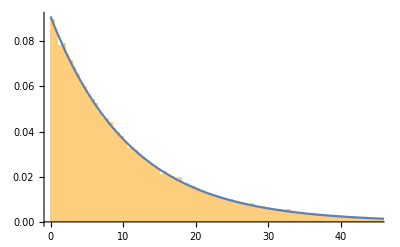

```mathematica
Show[Histogram[dat,200,"ProbabilityDensity"],Plot[PDF[ExponentialDistribution[(1/(1+nta))],x],{x,0,100},PlotRange->All]]
```

```mathematica
Integrate[x PDF[ExponentialDistribution[(1/(1+nta))],x],{x,0,Infinity}]
```

81

```mathematica
Here we numerically generate a single cooling cycle starting from a thermal state, with measurements in the coherent state basis. The data is saved, and compared to theory.
```

```mathematica
NTm=.;nta=10;SolTh=.;gamma=0;w0=1;dt=0.001Pi;dw=0.01 w0;
wd=2w0 ;wa[ta_]:=w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi]];phi=Pi/2;For[k=1,k<10001,k++,NTm[k]=RandomVariate[ExponentialDistribution[(1/(1+nta))],1][[1]];nj=1;SolTh[k]=NDSolve[{xa'[ta]==pa[ta]-gamma/2xa[ta],pa'[ta]==-wa[ta]^2xa[ta]-gamma/2 pa[ta],sxxa'[ta]==2sxpa[ta]- gamma sxxa[ta]+gamma (2nt+1)/(2wa[ta]),sxpa'[ta]==sppa[ta]-sxxa[ta]wa[ta]^2-gamma sxpa[ta],sppa'[ta]==-gamma sppa[ta] +gamma (2nt+1)wa[ta]/2-2sxpa[ta]wa[ta]^2,sxxa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==(1)/(2w0),sppa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==w0(1)/2,sxpa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0,xa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==Sqrt[2*NTm[k]/w0],pa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0},{xa,pa,sxxa,sppa,sxpa},{ta,dt IntegerPart[50Pi/(wd dt)(nj-1)],IntegerPart[50Pi/(wd dt)(nj)]dt}];plot[k]=Plot[Evaluate[(wa[ta]^2((sxxa[ta]/.SolTh[k])+(xa[ta]/.SolTh[k])^2)+((sppa[ta]/.SolTh[k])+(pa[ta]/.SolTh[k])^2))/(2wa[ta])-1/2],{ta,dt IntegerPart[50Pi(0)/(wd dt)],dt IntegerPart[50Pi/(wd dt)]},PlotRange->All,PlotStyle->Blue];
finalN0[k]=Evaluate[(wa[dt IntegerPart[0Pi/(wd dt)]]^2((sxxa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[0Pi/(wd dt)]])-1/2][[1]];finalN5[k]=Evaluate[(wa[dt IntegerPart[5Pi/(wd dt)]]^2((sxxa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[5Pi/(wd dt)]])-1/2][[1]];finalN10[k]=Evaluate[(wa[dt IntegerPart[10Pi/(wd dt)]]^2((sxxa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[10Pi/(wd dt)]])-1/2][[1]];finalN15[k]=Evaluate[(wa[dt IntegerPart[15Pi/(wd dt)]]^2((sxxa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[15Pi/(wd dt)]])-1/2][[1]];finalN20[k]=Evaluate[(wa[dt IntegerPart[20Pi/(wd dt)]]^2((sxxa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[20Pi/(wd dt)]])-1/2][[1]];finalN25[k]=Evaluate[(wa[dt IntegerPart[25Pi/(wd dt)]]^2((sxxa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[25Pi/(wd dt)]])-1/2][[1]];finalN30[k]=Evaluate[(wa[dt IntegerPart[30Pi/(wd dt)]]^2((sxxa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[30Pi/(wd dt)]])-1/2][[1]];finalN35[k]=Evaluate[(wa[dt IntegerPart[35Pi/(wd dt)]]^2((sxxa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[35Pi/(wd dt)]])-1/2][[1]];finalN40[k]=Evaluate[(wa[dt IntegerPart[40Pi/(wd dt)]]^2((sxxa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[40Pi/(wd dt)]])-1/2][[1]];finalN45[k]=Evaluate[(wa[dt IntegerPart[45Pi/(wd dt)]]^2((sxxa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[45Pi/(wd dt)]])-1/2][[1]];];tabth={{dt IntegerPart[0Pi/(wd dt)],Mean[Table[finalN0[k],{k,1,10000}]]},{dt IntegerPart[5Pi/(wd dt)],Mean[Table[finalN5[k],{k,1,10000}]]},{dt IntegerPart[10Pi/(wd dt)],Mean[Table[finalN10[k],{k,1,10000}]]},{dt IntegerPart[15Pi/(wd dt)],Mean[Table[finalN15[k],{k,1,10000}]]},{dt IntegerPart[20Pi/(wd dt)],Mean[Table[finalN20[k],{k,1,10000}]]},{dt IntegerPart[25Pi/(wd dt)],Mean[Table[finalN25[k],{k,1,10000}]]},{dt IntegerPart[30Pi/(wd dt)],Mean[Table[finalN30[k],{k,1,10000}]]},{dt IntegerPart[35Pi/(wd dt)],Mean[Table[finalN35[k],{k,1,10000}]]},{dt IntegerPart[40Pi/(wd dt)],Mean[Table[finalN40[k],{k,1,10000}]]},{dt IntegerPart[45Pi/(wd dt)],Mean[Table[finalN45[k],{k,1,10000}]]}}
```

```mathematica
tabth10={{0.,10.969605825993069},{7.850840041320893,9.380282634893499},{15.704821675295376,8.03892343577531},{23.55880330926986,6.904484680665446},{31.412784943244343,5.956725579826649},{39.266766577218824,5.165669973602153},{47.12074821119331,4.517206694565505},{54.97472984516779,3.9908236876836587},{62.82871147914228,3.577132820378664},{70.68269311311676,3.263046878712604}};
```

```mathematica
Mean[Table[NTm[k],{k,1,10000}]]
```

10.9696

## Average cooling starting from a thermal state of mean quanta n̄=10, numerical simulations.

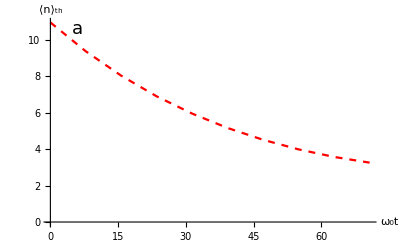

```mathematica
p11a=ListPlot[tabth10,Joined->True,PlotRange->All,PlotStyle->{Red,Dashed},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩_th",Black,18]},TicksStyle->Directive[Black],Epilog->{Inset[Style["a",18,Black],Scaled[{0.1,0.95}]]}]
```

```mathematica
The following averaging of theoretical expression for mean quanta yields the theory prediction. Repeated for different initial number of thermal quanta.
```

```mathematica
myd2 = 0.01 w0;nta=10;
myϕd = π/2;
myμ = .;D2[t_] = d2 Cos[ωd t + ϕd] /.ωd-> 2;P11[t_] = Exp[- d2 t]((Exp[ 2 d2 t]- 1)(Sin[t + ϕd] - d2 Sin[t]) + d2( Exp[2 d2 t ] + 1) Cos[t + ϕd]- (Exp[2 d2 t] + 1)Cos[t])/(2 (d2 Cos[ϕd]  - 1));
IP22[t_] = Exp[- d2 t]( (Exp[2 d2 t] - 1)Cos[t + ϕd]- (Exp[2d2 t] + 1)Sin[t])/(2 (d2 Cos[ϕd]- 1));α[t_] =(P11[t]- I IP22[t] + I D[P11[tp]- I IP22[tp],tp] /.tp-> t)/2;
β[t_] = (P11[t]+ I IP22[t] + I D[P11[tp]+ I IP22[tp],tp] /.tp-> t)/2;b[t_] = α[t] μ + β[t]Conjugate[μ];
bdb[t_] = (Abs[α[t]]^2 + Abs[β[t]]^2)Abs[μ]^2   + Conjugate[α[t]] β[t]Conjugate[μ]^2 + α[t]Conjugate[β[t]]μ^2 + Abs[β[t]]^2;
b2[t_] = α[t]^2 μ^2 + α[t]β[t](2 Abs[μ]^2 + 1) + β[t]^2 Conjugate[μ]^2;
params = {d2-> myd2,ϕd-> myϕd,μ->Sqrt[nmjh]};data = Table[{t,Integrate[Exp[-nmjh/(nta+1)]/((nta+1))(bdb[t]/.params),{nmjh,0,Infinity}]},{t,0,dt IntegerPart[45Pi/(wd dt)],0.1}]
```

```mathematica
data10={{0.,11.},{0.1,10.999822019757879},{0.2,10.998713718957639},{0.30000000000000004,10.995850403305555},{0.4,10.990482325617666},{0.5,10.981964215457635},{0.6000000000000001,10.969780533861874},{0.7000000000000001,10.95356546535399},{0.8,10.933116872789583},{0.9,10.908403683873807},{1.,10.879566441658081},{1.1,10.846911024386527},{1.2000000000000002,10.810895811822817},{1.3,10.772112834837793},{1.4000000000000001,10.731263682294337},{1.5,10.689131144778008},{1.6,10.646547740439877},{1.7000000000000002,10.60436238770668},{1.8,10.563406558303715},{1.9000000000000001,10.52446125939652},{2.,10.488226155290596},{2.1,10.455292048774558},{2.2,10.42611780365377},{2.3000000000000003,10.401012609002487},{2.4000000000000004,10.380124269535111},{2.5,10.363433963999647},{2.6,10.35075765438336},{2.7,10.341754063366903},{2.8000000000000003,10.33593887645165},{2.9000000000000004,10.332704578883716},{3.,10.331345115647755},{3.1,10.33108437413409},{3.2,10.331107340968005},{3.3000000000000003,10.330592682662575},{3.4000000000000004,10.32874544808204},{3.5,10.324828591039473},{3.6,10.318192063477875},{3.7,10.30829833131956},{3.8000000000000003,10.294743311972747},{3.9000000000000004,10.27727191863149},{4.,10.255787614334048},{4.1000000000000005,10.230355619461054},{4.2,10.20119967029103},{4.3,10.168692483230538},{4.4,10.133340329161559},{4.5,10.095762355088773},{4.6000000000000005,10.056665496732125},{4.7,10.0168159977846},{4.800000000000001,9.977008682532785},{4.9,9.938035213370105},{5.,9.900652600227746},{5.1000000000000005,9.865553213890886},{5.2,9.833337490356298},{5.300000000000001,9.804490401600633},{5.4,9.77936261399771},{5.5,9.758157065452401},{5.6000000000000005,9.740921473814158},{5.7,9.727547051103757},{5.800000000000001,9.717773450079253},{5.9,9.711199721588478},{6.,9.707300822877228},{6.1000000000000005,9.70544899798485},{6.2,9.704939160201992},{6.300000000000001,9.705017250782547},{6.4,9.704910433752},{6.5,9.703857918122115},{6.6000000000000005,9.701141178652403},{6.7,9.696112375102517},{6.800000000000001,9.688219846356425},{6.9,9.67702967663897},{7.,9.662242491303902},{7.1000000000000005,9.643704832817605},{7.2,9.621414685779314},{7.300000000000001,9.595520954324924},{7.4,9.566316936663048},{7.5,9.534228080156376},{7.6000000000000005,9.49979452680443},{7.7,9.463649164243503},{7.800000000000001,9.42649207337437},{7.9,9.389062403570659},{8.,9.352108804691106},{8.1,9.31635959807093},{8.200000000000001,9.282493874374763},{8.3,9.251114664615258},{8.4,9.222725243619685},{8.5,9.197709496403013},{8.6,9.176317112571843},{8.700000000000001,9.158654178760727},{8.8,9.144679522072902},{8.9,9.134206927282166},{9.,9.126913116363479},{9.1,9.122351150090017},{9.200000000000001,9.119968697047195},{9.3,9.119130423942122},{9.4,9.119143600057459},{9.5,9.119285884398286},{9.600000000000001,9.118834181309863},{9.700000000000001,9.117093412231812},{9.8,9.113424059140552},{9.9,9.107267388621052},{10.,9.098167362097833},{10.100000000000001,9.085788373529178},{10.200000000000001,9.06992812527229},{10.3,9.05052514898675},{10.4,9.027660693450235},{10.5,9.00155492638394},{10.600000000000001,8.972557623825999},{10.700000000000001,8.941133739233837},{10.8,8.907844446673892},{10.9,8.873324430189465},{11.,8.838256337750334},{11.100000000000001,8.803343427384046},{11.200000000000001,8.769281500968836},{11.3,8.736731245196449},{11.4,8.706292078603722},{11.5,8.678478539322885},{11.600000000000001,8.653700143038808},{11.700000000000001,8.632245498912251},{11.8,8.614271298714645},{11.9,8.59979659810693},{12.,8.588702596785845},{12.100000000000001,8.580737904622701},{12.200000000000001,8.575529062696763},{12.3,8.572595879955577},{12.4,8.57137095636031},{12.5,8.57122259927767},{12.600000000000001,8.571480207988934},{12.700000000000001,8.571461106621472},{12.8,8.570497752185183},{12.9,8.567964233686759},{13.,8.563301010758147},{13.100000000000001,8.556036914408388},{13.200000000000001,8.545807545277617},{13.3,8.53236935149838},{13.4,8.515608842983134},{13.5,8.495546594595522},{13.600000000000001,8.472335899362088},{13.700000000000001,8.44625614628546},{13.8,8.417701206920832},{13.9,8.38716331235081},{14.,8.355213079730238},{14.100000000000001,8.322476498187132},{14.200000000000001,8.289609801671807},{14.3,8.257273236785048},{14.4,8.226104773634127},{14.5,8.196694805928516},{14.600000000000001,8.169562843072724},{14.700000000000001,8.145137113833309},{14.8,8.123737881715623},{14.9,8.105565121377902},{15.,8.090691029357515},{15.100000000000001,8.079057648190815},{15.200000000000001,8.070479678470234},{15.3,8.06465234667864},{15.4,8.061163996003517},{15.5,8.05951288072084},{15.600000000000001,8.059127479520937},{15.700000000000001,8.059389505814249},{15.8,8.05965868896067},{15.9,8.059298333521694},{16.,8.057700636555294},{16.1,8.054310756580438},{16.2,8.048648681431626},{16.3,8.04032803351576},{16.400000000000002,8.029071076194116},{16.5,8.014719339028018},{16.6,7.9972394562078435},{16.7,7.976724004518026},{16.8,7.953387326975271},{16.900000000000002,7.927556527834956},{17.,7.899658016052897},{17.1,7.870200149933578},{17.2,7.839752688665296},{17.3,7.808923880739412},{17.400000000000002,7.778336110041744},{17.5,7.748601074207859},{17.6,7.7202954846529215},{17.7,7.693938253084283},{17.8,7.669970066412232},{17.900000000000002,7.648736153442947},{18.,7.630472916626017},{18.1,7.615298945736505},{18.2,7.603210754022026},{18.3,7.594083388132755},{18.400000000000002,7.587675868654267},{18.5,7.5836412260375745},{18.6,7.581540714799227},{18.7,7.580861624243196},{18.8,7.581037963119721},{18.900000000000002,7.581473184093974},{19.,7.581564035973621},{19.1,7.58072459030913},{19.200000000000003,7.578409485736209},{19.3,7.574135468258269},{19.400000000000002,7.567500377033905},{19.5,7.558198830160615},{19.6,7.546033999125882},{19.700000000000003,7.5309250185795635},{19.8,7.512909753489088},{19.900000000000002,7.492142831526192},{20.,7.468889037269033},{20.1,7.443512348965791},{20.200000000000003,7.416461070887271},{20.3,7.3882496678877665},{20.400000000000002,7.3594380376572595},{20.5,7.330609055253228},{20.6,7.302345290018271},{20.700000000000003,7.275205824444339},{20.8,7.249704096902739},{20.900000000000002,7.226287645867803},{21.,7.2053205542260415},{21.1,7.187069281758563},{21.200000000000003,7.171692436431431},{21.3,7.159234876298036},{21.400000000000002,7.149626360010874},{21.5,7.142684782130048},{21.6,7.138123846865927},{21.700000000000003,7.135564857869096},{21.8,7.134552139160066},{21.900000000000002,7.134571459687607},{22.,7.135070716914706},{22.1,7.135482047815293},{22.200000000000003,7.1352444820693215},{22.3,7.1338262340715115},{22.400000000000002,7.130745748208162},{22.5,7.1255906648576515},{22.6,7.118033960490677},{22.700000000000003,7.107846630541085},{22.8,7.094906423687858},{22.900000000000002,7.079202295169867},{23.,7.060834418350682},{23.1,7.040009771084475},{23.200000000000003,7.017033489430587},{23.3,6.992296348925853},{23.400000000000002,6.966258886312456},{23.5,6.939432806318299},{23.6,6.912360423636971},{23.700000000000003,6.885592965556076},{23.8,6.859668602857483},{23.900000000000002,6.83509108410768},{24.,6.812309821107181},{24.1,6.791702212294946},{24.200000000000003,6.773558898861725},{24.3,6.758072528995486},{24.400000000000002,6.745330463913653},{24.5,6.73531170085766},{24.6,6.727888119401782},{24.700000000000003,6.722829985018636},{24.8,6.719815474718429},{24.900000000000002,6.718443830455196},{25.,6.718251603162659},{25.1,6.718731329365161},{25.200000000000003,6.7193518880319845},{25.3,6.719579721356387},{25.400000000000002,6.718900071872682},{25.5,6.7168373908967025},{25.6,6.712974109454544},{25.700000000000003,6.706967031085657},{25.8,6.698560703332579},{25.900000000000002,6.687597247374179},{26.,6.674022268148113},{26.1,6.657886624678251},{26.200000000000003,6.639344005860968},{26.3,6.6186444240513405},{26.400000000000002,6.596123900775795},{26.5,6.572190769354966},{26.6,6.547309152209015},{26.700000000000003,6.5219802809118645},{26.8,6.496722410359968},{26.900000000000002,6.472050131512764},{27.,6.448453908049085},{27.1,6.4263806502561245},{27.200000000000003,6.406216095129759},{27.3,6.388269686900943},{27.400000000000002,6.372762550104049},{27.5,6.359819022032266},{27.6,6.349462068055105},{27.700000000000003,6.341612747574334},{27.8,6.3360937366088566},{27.900000000000002,6.332636751584101},{28.,6.330893564278399},{28.1,6.3304501561725655},{28.200000000000003,6.330843437248277},{28.3,6.331579854417464},{28.400000000000002,6.332155142123367},{28.5,6.332074425021939},{28.6,6.330871871612774},{28.700000000000003,6.3281291185620026},{28.8,6.323491737295656},{28.900000000000002,6.316683095062279},{29.,6.307515068752645},{29.1,6.295895197006798},{29.200000000000003,6.281829999392494},{29.3,6.265424344946033},{29.400000000000002,6.246876909981293},{29.5,6.226471920509554},{29.6,6.204567521696848},{29.700000000000003,6.18158124969636},{29.8,6.157973194697341},{29.900000000000002,6.134227533685635},{30.,6.110833173737551},{30.1,6.088264279290231},{30.200000000000003,6.066961458562725},{30.3,6.047314355186829},{30.400000000000002,6.029646332421168},{30.5,6.0142018515090685},{30.6,6.001137036316136},{30.700000000000003,5.99051378778825},{30.8,5.982297669191026},{30.900000000000002,5.976359632253378},{31.,5.97248150126944},{31.1,5.970364983015007},{31.200000000000003,5.969643830924931},{31.3,5.9698986678681},{31.400000000000002,5.970673867925912},{31.5,5.971495817888226},{31.6,5.9718918268080055},{31.700000000000003,5.971408928884461},{31.8,5.96963183198289},{31.900000000000002,5.96619930085715},{32.,5.960818329044219},{32.1,5.9532755437645175},{32.2,5.943445400297001},{32.300000000000004,5.931294851663512},{32.4,5.916884320842555},{32.5,5.900364950469513},{32.6,5.8819722531684935},{32.7,5.862016428403114},{32.800000000000004,5.840869743372154},{32.9,5.818951490815084},{33.,5.796711131103626},{33.1,5.774610295996959},{33.2,5.753104374233996},{33.300000000000004,5.732624413125246},{33.4,5.713560055038398},{33.5,5.6962441838599664},{33.6,5.680939886009707},{33.7,5.667830236285422},{33.800000000000004,5.657011304563902},{33.9,5.648488649795908},{34.,5.642177428020677},{34.1,5.637906096883854},{34.2,5.635423556125503},{34.300000000000004,5.634409427397455},{34.4,5.634487052960149},{34.5,5.635238686178501},{34.6,5.636222261463344},{34.7,5.636989070703225},{34.800000000000004,5.637101639621891},{34.9,5.636151092117768},{35.,5.6337733136042525},{35.1,5.629663274657053},{35.2,5.623586951787},{35.300000000000004,5.615390379798121},{35.4,5.605005485996986},{35.5,5.592452485817133},{35.6,5.577838757019587},{35.7,5.561354250024884},{35.800000000000004,5.543263629524908},{35.9,5.5238954718567115},{36.,5.503628958575175},{36.1,5.482878604676199},{36.2,5.462077636162492},{36.300000000000004,5.441660683154392},{36.4,5.422046479572185},{36.5,5.403621257659405},{36.6,5.3867234954910455},{36.7,5.371630619412029},{36.800000000000004,5.358548183409268},{36.9,5.347601947001927},{37.,5.338833156405985},{37.1,5.332197205198386},{37.2,5.327565715626798},{37.300000000000004,5.324731945481352},{37.4,5.323419293486031},{37.5,5.323292553715272},{37.6,5.3239714614310305},{37.7,5.325045983216634},{37.800000000000004,5.326092736850831},{37.9,5.326691883620379},{38.,5.326443819325913},{38.1,5.324985000652012},{38.2,5.322002280338833},{38.300000000000004,5.317245186152724},{38.400000000000006,5.310535662468877},{38.5,5.301774895937505},{38.6,5.290946964055636},{38.7,5.278119172787886},{38.800000000000004,5.263439081573394},{38.900000000000006,5.247128345844844},{39.,5.229473633329733},{39.1,5.210814985905626},{39.2,5.191532099083446},{39.300000000000004,5.172029072360585},{39.400000000000006,5.152718242557478},{39.5,5.134003746565222},{39.6,5.1162654684091065},{39.7,5.0998440079293825},{39.800000000000004,5.085027265486273},{39.900000000000006,5.0720391707100525},{40.,5.061030996159266},{40.1,5.052075592363754},{40.2,5.045164763325525},{40.300000000000004,5.040209875845942},{40.400000000000006,5.037045667071878},{40.5,5.0354370875474235},{40.6,5.035088896871653},{40.7,5.035657620552064},{40.800000000000004,5.036765384083943},{40.900000000000006,5.038015067302354},{41.,5.039006171481632},{41.1,5.039350765428617},{41.2,5.0386888758895365},{41.300000000000004,5.036702711914203},{41.400000000000006,5.033129161339047},{41.5,5.027770068248605},{41.6,5.020499890263071},{41.7,5.011270440131502},{41.800000000000004,5.000112533129382},{41.900000000000006,4.987134485471737},{42.,4.972517534414393},{42.1,4.956508372930311},{42.2,4.939409105964661},{42.300000000000004,4.921565036781188},{42.400000000000006,4.903350776819052},{42.5,4.8851552374645},{42.6,4.867366104689242},{42.7,4.8503544160029275},{42.800000000000004,4.834459852958163},{42.900000000000006,4.8199773318652985},{43.,4.807145421721134},{43.1,4.796137043845538},{43.2,4.787052815386316},{43.300000000000004,4.779917292431974},{43.400000000000006,4.774678252243538},{43.5,4.771209032738573},{43.6,4.7693138256777},{43.7,4.768735702857616},{43.800000000000004,4.769167046648628},{43.900000000000006,4.770261961692103},{44.,4.771650167207243},{44.1,4.77295181216625},{44.2,4.773792620787441},{44.300000000000004,4.773818764675526},{44.400000000000006,4.772710870868877},{44.5,4.770196611438019},{44.6,4.766061378591417},{44.7,4.760156627089587},{44.800000000000004,4.752405559984135},{44.900000000000006,4.742805940480904},{45.,4.731429927787148},{45.1,4.718420953535962},{45.2,4.703987773052704},{45.300000000000004,4.6883959376607995},{45.400000000000006,4.671957035985773},{45.5,4.655016139793562},{45.6,4.637937959855674},{45.7,4.621092266948914},{45.800000000000004,4.60483916046307},{45.900000000000006,4.589514771195991},{46.,4.575417965674241},{46.1,4.562798577594242},{46.2,4.551847629468684},{46.300000000000004,4.542689926842421},{46.400000000000006,4.535379311781953},{46.5,4.52989675559874},{46.6,4.526151357220438},{46.7,4.5239841978157775},{46.800000000000004,4.523174888820977},{46.900000000000006,4.523450543913496},{47.,4.524496809949667},{47.1,4.525970511188929},{47.2,4.527513398428884},{47.300000000000004,4.528766452406687},{47.400000000000006,4.529384170596473},{47.5,4.529048269080424},{47.6,4.527480256317324},{47.7,4.524452382300393},{47.800000000000004,4.519796532860032},{47.900000000000006,4.5134107220258715},{48.,4.505262932052914},{48.1,4.495392157049296},{48.2,4.483906617855728},{48.300000000000004,4.470979228460239},{48.400000000000006,4.456840503301536},{48.5,4.441769195995963},{48.6,4.426081049316076},{48.7,4.410116110142741},{48.800000000000004,4.394225118717653},{48.900000000000006,4.378755516687294},{49.,4.364037631822304},{49.1,4.350371588453909},{49.2,4.338015462017836},{49.300000000000004,4.327175144924599},{49.400000000000006,4.317996321385557},{49.5,4.310558863644197},{49.6,4.30487386472976},{49.7,4.300883417276736},{49.800000000000004,4.298463138363336},{49.900000000000006,4.297427331087526},{50.,4.297536569063091},{50.1,4.298507394323647},{50.2,4.300023736045874},{50.300000000000004,4.301749590309911},{50.400000000000006,4.303342452423667},{50.5,4.304466965028815},{50.6,4.304808238337254},{50.7,4.304084313624557},{50.800000000000004,4.302057276873278},{50.900000000000006,4.298542584724684},{51.,4.293416237402586},{51.1,4.286619520078821},{51.2,4.2781611317582575},{51.300000000000004,4.268116625256566},{51.400000000000006,4.256625189047618},{51.5,4.243883907397922},{51.6,4.2301397350855705},{51.7,4.2156795131680855},{51.800000000000004,4.2008184291599955},{51.900000000000006,4.185887385592302},{52.,4.171219782892204},{52.1,4.157138244231902},{52.2,4.143941810650986},{52.300000000000004,4.131894114396825},{52.400000000000006,4.121212997928468},{52.5,4.112061987063691},{52.6,4.104543951721014},{52.7,4.098697199650683},{52.800000000000004,4.094494151005055},{52.900000000000006,4.091842638477836},{53.,4.090589773161105},{53.1,4.090528214394265},{53.2,4.091404586751523},{53.300000000000004,4.092929702697424},{53.400000000000006,4.094790178666361},{53.5,4.09666097816286},{53.6,4.098218380038089},{53.7,4.0991528547262},{53.800000000000004,4.099181336471431},{53.900000000000006,4.09805840517082},{54.,4.0955859363186145},{54.1,4.091620839822763},{54.2,4.086080585641774},{54.300000000000004,4.078946303146489},{54.400000000000006,4.070263338272053},{54.5,4.060139254002208},{54.6,4.048739361471465},{54.7,4.036279966934091},{54.800000000000004,4.023019610147327},{54.900000000000006,4.009248648782649},{55.,3.995277608201512},{55.1,3.9814247637818276},{55.2,3.9680034521047696},{55.300000000000004,3.955309616607704},{55.400000000000006,3.9436100824675338},{55.5,3.933132024991073},{55.6,3.9240540469269933},{55.7,3.9164992148748943},{55.800000000000004,3.910530325995507},{55.900000000000006,3.906147586702745},{56.,3.903288788535105},{56.1,3.9018319668190644},{56.2,3.9016004290193047},{56.300000000000004,3.902369945743827},{56.400000000000006,3.903877811957147},{56.5,3.9058334124234513},{56.6,3.9079298666430726},{56.7,3.909856286852984},{56.800000000000004,3.911310159643272},{56.900000000000006,3.912009358257004},{57.,3.9117033087718878},{57.1,3.9101828684101814},{57.2,3.9072885267382236},{57.300000000000004,3.9029166083608113},{57.400000000000006,3.8970232361443355},{57.5,3.8896259037818894},{57.6,3.880802602045884},{57.7,3.870688540542691},{57.800000000000004,3.8594706023084195},{57.900000000000006,3.8473797583717086},{58.,3.8346817499038597},{58.1,3.8216664136052656},{58.2,3.8086360788698443},{58.300000000000004,3.7958935009659327},{58.400000000000006,3.783729811603187},{58.5,3.772412966192047},{58.6,3.7621771459812843},{58.7,3.7532135339760915},{58.800000000000004,3.7456628277060777},{58.900000000000006,3.739609781797942},{59.,3.735079991740181},{59.1,3.732039040481895},{59.2,3.730394035179077},{59.300000000000004,3.7299974662503916},{59.400000000000006,3.7306532287202843},{59.5,3.7321245602646584},{59.6,3.7341435748193836},{59.7,3.7364220080405266},{59.800000000000004,3.7386627437686046},{59.900000000000006,3.740571660780504},{60.,3.741869327649525},{60.1,3.742302080883393},{60.2,3.7416520473249055},{60.300000000000004,3.73974571500532},{60.400000000000006,3.7364607154676763},{60.5,3.7317305526459803},{60.6,3.7255470957921313},{60.7,3.7179607433819353},{60.800000000000004,3.7090782578270542},{60.900000000000006,3.699058363469232},{61.,3.688105289051362},{61.1,3.6764605171309905},{61.2,3.6643930735133416},{61.300000000000004,3.6521887469540566},{61.400000000000006,3.640138670879556},{61.5,3.628527723087324},{61.6,3.6176232054033193},{61.7,3.607664252898825},{61.800000000000004,3.598852392045957},{61.900000000000006,3.5913436203698055},{62.,3.5852423186414963},{62.1,3.5805972329361624},{62.2,3.5773996809170168},{62.300000000000004,3.5755840478250662},{62.400000000000006,3.575030546403175},{62.5,3.575570124998777},{62.6,3.576991322946766},{62.7,3.5790487954039243},{62.800000000000004,3.581473164129759},{62.900000000000006,3.583981798863656},{63.,3.5862900979646306},{63.1,3.5881228182428666},{63.2,3.5892250031251596},{63.300000000000004,3.589372075441943},{63.400000000000006,3.58837869547376},{63.5,3.5861060350399216},{63.6,3.5824671823157184},{63.7,3.577430467151629},{63.800000000000004,3.5710205799221812},{63.900000000000006,3.5633174450234737},{64.,3.5544528995506735},{64.10000000000001,3.5446053148608696},{64.2,3.5339923802026445},{64.3,3.5228623401456236},{64.4,3.511484038308827},{64.5,3.500136166479192},{64.60000000000001,3.4890961488150154},{64.7,3.4786291042656816},{64.8,3.468977326118296},{64.9,3.460350695916182},{65.,3.4529184107879893},{65.10000000000001,3.4468023500408616},{65.2,3.4420723408584735},{65.3,3.4387435067617496},{65.4,3.436775799191035},{65.5,3.436075725484249},{65.60000000000001,3.4365001991270523},{65.7,3.437862353915475},{65.8,3.4399390859401544},{65.9,3.4424800191492286},{66.,3.4452175343611544},{66.10000000000001,3.4478774601708464},{66.2,3.45018999883552},{66.3,3.451900451909792},{66.4,3.4527793194112637},{66.5,3.4526313722397957},{66.60000000000001,3.4513033393721386},{66.7,3.448689907308799},{66.8,3.444737797103426},{66.9,3.4394477613299004},{67.,3.432874426453685},{67.10000000000001,3.42512399195305},{67.2,3.4163498827609966},{67.3,3.406746532782123},{67.4,3.3965415511626316},{67.5,3.3859865867328773},{67.60000000000001,3.3753472570897927},{67.7,3.364892545141306},{67.8,3.3548840861844837},{67.9,3.3455657719664638},{68.,3.3371540845863583},{68.10000000000001,3.329829543117641},{68.2,3.3237296006930124},{68.3,3.3189432713275715},{68.4,3.3155076963169696},{68.5,3.31340678241983},{68.60000000000001,3.312571961325847},{68.7,3.3128850354204626},{68.8,3.31418299194914},{68.9,3.316264589651967},{69.,3.31889845187373},{69.10000000000001,3.321832340824517},{69.2,3.3248032414069413},{69.3,3.327547851646873},{69.4,3.329813061482292},{69.5,3.3313660030484695},{69.60000000000001,3.332003273558549},{69.7,3.3315589656632802},{69.8,3.329911188405875},{69.9,3.3269868226169086},{70.,3.322764325379083},{70.10000000000001,3.3172744761947905},{70.2,3.3105990395940648},{70.3,3.3028674018530175},{70.4,3.2942513199539913},{70.5,3.28495799571309},{70.60000000000001,3.2752217541688284}};
```

```mathematica
pbbb=ListPlot[data10, Joined->True,PlotStyle->{Blue},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩_th",Black,18]},TicksStyle->Directive[Black],Epilog->{Inset[Style["a",18,Black],Scaled[{0.1,0.95}]]}]
```

## Average cooling starting from a thermal state of mean quanta n̄=10, prediction based on theory.

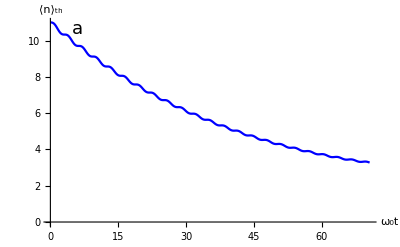

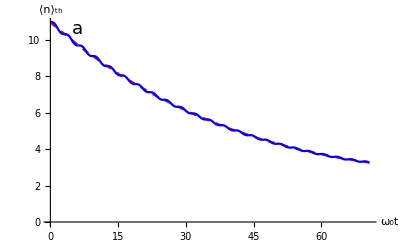

```mathematica
pacc=Show[p11a,pbbb]
```

```mathematica
(*=============================================================================================================================================*)
```

```mathematica
NTm=.;nta=8;SolTh=.;gamma=0;w0=1;dt=0.001Pi;dw=0.01 w0;
wd=2w0 ;wa[ta_]:=w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi]];phi=Pi/2;For[k=1,k<10001,k++,NTm[k]=RandomVariate[ExponentialDistribution[(1/(1+nta))],1][[1]];nj=1;SolTh[k]=NDSolve[{xa'[ta]==pa[ta]-gamma/2xa[ta],pa'[ta]==-wa[ta]^2xa[ta]-gamma/2 pa[ta],sxxa'[ta]==2sxpa[ta]- gamma sxxa[ta]+gamma (2nt+1)/(2wa[ta]),sxpa'[ta]==sppa[ta]-sxxa[ta]wa[ta]^2-gamma sxpa[ta],sppa'[ta]==-gamma sppa[ta] +gamma (2nt+1)wa[ta]/2-2sxpa[ta]wa[ta]^2,sxxa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==(1)/(2w0),sppa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==w0(1)/2,sxpa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0,xa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==Sqrt[2*NTm[k]/w0],pa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0},{xa,pa,sxxa,sppa,sxpa},{ta,dt IntegerPart[50Pi/(wd dt)(nj-1)],IntegerPart[50Pi/(wd dt)(nj)]dt}];plot[k]=Plot[Evaluate[(wa[ta]^2((sxxa[ta]/.SolTh[k])+(xa[ta]/.SolTh[k])^2)+((sppa[ta]/.SolTh[k])+(pa[ta]/.SolTh[k])^2))/(2wa[ta])-1/2],{ta,dt IntegerPart[50Pi(0)/(wd dt)],dt IntegerPart[50Pi/(wd dt)]},PlotRange->All,PlotStyle->Blue];
finalN0[k]=Evaluate[(wa[dt IntegerPart[0Pi/(wd dt)]]^2((sxxa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[0Pi/(wd dt)]])-1/2][[1]];finalN5[k]=Evaluate[(wa[dt IntegerPart[5Pi/(wd dt)]]^2((sxxa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[5Pi/(wd dt)]])-1/2][[1]];finalN10[k]=Evaluate[(wa[dt IntegerPart[10Pi/(wd dt)]]^2((sxxa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[10Pi/(wd dt)]])-1/2][[1]];finalN15[k]=Evaluate[(wa[dt IntegerPart[15Pi/(wd dt)]]^2((sxxa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[15Pi/(wd dt)]])-1/2][[1]];finalN20[k]=Evaluate[(wa[dt IntegerPart[20Pi/(wd dt)]]^2((sxxa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[20Pi/(wd dt)]])-1/2][[1]];finalN25[k]=Evaluate[(wa[dt IntegerPart[25Pi/(wd dt)]]^2((sxxa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[25Pi/(wd dt)]])-1/2][[1]];finalN30[k]=Evaluate[(wa[dt IntegerPart[30Pi/(wd dt)]]^2((sxxa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[30Pi/(wd dt)]])-1/2][[1]];finalN35[k]=Evaluate[(wa[dt IntegerPart[35Pi/(wd dt)]]^2((sxxa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[35Pi/(wd dt)]])-1/2][[1]];finalN40[k]=Evaluate[(wa[dt IntegerPart[40Pi/(wd dt)]]^2((sxxa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[40Pi/(wd dt)]])-1/2][[1]];finalN45[k]=Evaluate[(wa[dt IntegerPart[45Pi/(wd dt)]]^2((sxxa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[45Pi/(wd dt)]])-1/2][[1]];];tabth={{dt IntegerPart[0Pi/(wd dt)],Mean[Table[finalN0[k],{k,1,10000}]]},{dt IntegerPart[5Pi/(wd dt)],Mean[Table[finalN5[k],{k,1,10000}]]},{dt IntegerPart[10Pi/(wd dt)],Mean[Table[finalN10[k],{k,1,10000}]]},{dt IntegerPart[15Pi/(wd dt)],Mean[Table[finalN15[k],{k,1,10000}]]},{dt IntegerPart[20Pi/(wd dt)],Mean[Table[finalN20[k],{k,1,10000}]]},{dt IntegerPart[25Pi/(wd dt)],Mean[Table[finalN25[k],{k,1,10000}]]},{dt IntegerPart[30Pi/(wd dt)],Mean[Table[finalN30[k],{k,1,10000}]]},{dt IntegerPart[35Pi/(wd dt)],Mean[Table[finalN35[k],{k,1,10000}]]},{dt IntegerPart[40Pi/(wd dt)],Mean[Table[finalN40[k],{k,1,10000}]]},{dt IntegerPart[45Pi/(wd dt)],Mean[Table[finalN45[k],{k,1,10000}]]}}
```

```mathematica
tabth8={{0.,9.114055165915852},{7.850840041320893,7.7946193069351954},{15.704821675295376,6.68331333262008},{23.55880330926986,5.74613607360598},{31.412784943244343,4.96636620703139},{39.266766577218824,4.319340819171751},{47.12074821119331,3.7935181394785933},{54.97472984516779,3.3722652771598542},{62.82871147914228,3.0480693211034424},{70.68269311311676,2.8106739649833843}};
```

## Average cooling starting from a thermal state of mean quanta n̄=8, numerical simulations.

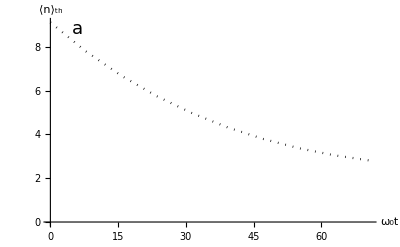

```mathematica
p11a8=ListPlot[tabth8,Joined->True,PlotRange->All,PlotStyle->{Black,Dotted},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩_th",Black,18]},TicksStyle->Directive[Black],Epilog->{Inset[Style["a",18,Black],Scaled[{0.1,0.95}]]}]
```

## Here we generate the data using corresponding theory prediction.

```mathematica
myd2 = 0.01 w0;nta=8;
myϕd = π/2;
myμ = .;D2[t_] = d2 Cos[ωd t + ϕd] /.ωd-> 2;P11[t_] = Exp[- d2 t]((Exp[ 2 d2 t]- 1)(Sin[t + ϕd] - d2 Sin[t]) + d2( Exp[2 d2 t ] + 1) Cos[t + ϕd]- (Exp[2 d2 t] + 1)Cos[t])/(2 (d2 Cos[ϕd]  - 1));
IP22[t_] = Exp[- d2 t]( (Exp[2 d2 t] - 1)Cos[t + ϕd]- (Exp[2d2 t] + 1)Sin[t])/(2 (d2 Cos[ϕd]- 1));α[t_] =(P11[t]- I IP22[t] + I D[P11[tp]- I IP22[tp],tp] /.tp-> t)/2;
β[t_] = (P11[t]+ I IP22[t] + I D[P11[tp]+ I IP22[tp],tp] /.tp-> t)/2;b[t_] = α[t] μ + β[t]Conjugate[μ];
bdb[t_] = (Abs[α[t]]^2 + Abs[β[t]]^2)Abs[μ]^2   + Conjugate[α[t]] β[t]Conjugate[μ]^2 + α[t]Conjugate[β[t]]μ^2 + Abs[β[t]]^2;
b2[t_] = α[t]^2 μ^2 + α[t]β[t](2 Abs[μ]^2 + 1) + β[t]^2 Conjugate[μ]^2;
params = {d2-> myd2,ϕd-> myϕd,μ->Sqrt[nmjh]};data = Table[{t,Integrate[Exp[-nmjh/(nta+1)]/((nta+1))(bdb[t]/.params),{nmjh,0,Infinity}]},{t,0,dt IntegerPart[45Pi/(wd dt)],0.1}]
```

```mathematica
data8={{0.,9.},{0.1,8.999854562203373},{0.2,8.998948319940846},{0.30000000000000004,8.996606526161626},{0.4,8.992215753495337},{0.5,8.985248054592397},{0.6000000000000001,8.975281624884632},{0.7000000000000001,8.96201715958511},{0.8,8.945289271289898},{0.9,8.925072533602158},{1.,8.901481931753025},{1.1,8.874767724602231},{1.2000000000000002,8.84530494474396},{1.3,8.813577975877926},{1.4000000000000001,8.780160840719855},{1.5,8.745694000868728},{1.6,8.710858605634611},{1.7000000000000002,8.676349224595269},{1.8,8.642846154853924},{1.9000000000000001,8.610988406543285},{2.,8.581348438736395},{2.1,8.55440964400706},{2.2,8.53054746654174},{2.3000000000000003,8.510014890607787},{2.4000000000000004,8.49293285936047},{2.5,8.479285985572847},{2.6,8.468923703878344},{2.7,8.46156679701418},{2.8000000000000003,8.456819015002647},{2.9000000000000004,8.454183304689597},{3.,8.453081985544378},{3.1,8.452880053256024},{3.2,8.452910671469406},{3.3000000000000003,8.45250182868343},{3.4000000000000004,8.45100309504394},{3.5,8.447811414027706},{3.6,8.44239490664925},{3.7,8.434313748965868},{3.8000000000000003,8.423237303837865},{3.9000000000000004,8.408956840192008},{4.,8.391393351250207},{4.1000000000000005,8.370600180127955},{4.2,8.346760368968603},{4.3,8.320178858050964},{4.4,8.291269865712543},{4.5,8.260539970360261},{4.6000000000000005,8.228567584773646},{4.7,8.195979653706138},{4.800000000000001,8.16342651296831},{4.9,8.131555917602068},{5.,8.1009872758142},{5.1000000000000005,8.072287113036465},{5.2,8.045946737469514},{5.300000000000001,8.022362987022548},{5.4,8.001822811467452},{5.5,7.984492288042884},{5.6000000000000005,7.970410489974504},{5.7,7.9594884326289295},{5.800000000000001,7.951513119101811},{5.9,7.946156504060346},{6.,7.94298899969421},{6.1000000000000005,7.941496968400805},{6.2,7.94110349040989},{6.300000000000001,7.941191567071633},{6.4,7.9411288269483205},{6.5,7.940292745752515},{6.6000000000000005,7.938095374646515},{6.7,7.934006594960444},{6.800000000000001,7.927574979903814},{6.9,7.918445442696373},{7.,7.906372981651359},{7.1000000000000005,7.891231990764438},{7.2,7.873020782900781},{7.300000000000001,7.851861164546409},{7.4,7.8279930986115875},{7.5,7.8017646870624455},{7.6000000000000005,7.773617890451894},{7.7,7.744070569388663},{7.800000000000001,7.713695577010919},{7.9,7.683097745981633},{8.,7.65288969396114},{8.1,7.623667414871439},{8.200000000000001,7.595986627968756},{8.3,7.5703408227511115},{8.4,7.547141866551477},{8.5,7.5267039362829555},{8.6,7.509231400538631},{8.700000000000001,7.494811118604195},{8.8,7.483409445364735},{8.9,7.474874042713327},{9.,7.468940406435785},{9.1,7.465242830290214},{9.200000000000001,7.4633293535544905},{9.3,7.462680081613351},{9.4,7.4627281373596475},{9.5,7.4628823994370626},{9.600000000000001,7.462551115583978},{9.700000000000001,7.461165448112037},{9.8,7.458202014967021},{9.9,7.453203533470129},{10.,7.445796752841711},{10.100000000000001,7.43570697268385},{10.200000000000001,7.422768583198272},{10.3,7.406931223418587},{10.4,7.388261329669529},{10.5,7.3669390307697995},{10.600000000000001,7.343250531804445},{10.700000000000001,7.317576307230287},{10.8,7.290375589550282},{10.9,7.262167785268988},{11.,7.233511569612504},{11.100000000000001,7.204982500898846},{11.200000000000001,7.177150051039686},{11.3,7.15055496836489},{11.4,7.125687872141723},{11.5,7.102969925625693},{11.600000000000001,7.082736348458826},{11.700000000000001,7.065223413277858},{11.8,7.050559430240356},{11.9,7.038760062535705},{12.,7.029728142287314},{12.100000000000001,7.023257976533467},{12.200000000000001,7.0190439543696925},{12.3,7.0166930959475176},{12.4,7.015741028599434},{12.5,7.015670741022514},{12.600000000000001,7.015933358465704},{12.700000000000001,7.015970104421043},{12.8,7.015234570378913},{12.9,7.013214406387878},{13.,7.0094515716756565},{13.100000000000001,7.003560345244161},{13.200000000000001,6.995242388603362},{13.3,6.984298272860627},{13.4,6.970635025350475},{13.5,6.95426941109578},{13.600000000000001,6.935326835199287},{13.700000000000001,6.914035926936339},{13.8,6.890719037891385},{13.9,6.865779048138819},{14.,6.839683019819809},{14.100000000000001,6.812943360792294},{14.200000000000001,6.786097257510693},{14.3,6.759685202191502},{14.4,6.734229472138461},{14.5,6.710213417659798},{14.600000000000001,6.688062379501108},{14.700000000000001,6.668126988686453},{14.8,6.650669503940099},{14.9,6.635853718456347},{15.,6.6237388237035075},{15.100000000000001,6.6142774590042634},{15.200000000000001,6.607318008208717},{15.3,6.602611035562865},{15.4,6.5998195886128554},{15.5,6.5985329431896815},{15.600000000000001,6.598283230224899},{15.700000000000001,6.598564271668659},{15.8,6.598851867504633},{15.9,6.598624721067575},{16.,6.597385167630758},{16.1,6.594678882299742},{16.2,6.590112787056429},{16.3,6.583370451473569},{16.400000000000002,6.574224384073082},{16.5,6.562544737348881},{16.6,6.5483040940096755},{16.7,6.531578159197722},{16.8,6.512542347002565},{16.900000000000002,6.491464412982675},{17.,6.4686934411328085},{17.1,6.444645637581532},{17.2,6.419787508599164},{17.3,6.394617102328106},{17.400000000000002,6.369644068055007},{17.5,6.345369330973715},{17.6,6.322265192600243},{17.7,6.300756646934653},{17.8,6.281204651042231},{17.900000000000002,6.263892008114925},{18.,6.249012414593488},{18.1,6.236663094917311},{18.2,6.2268413030983325},{18.3,6.2194448153945245},{18.400000000000002,6.214276379091358},{18.5,6.21105192513868},{18.6,6.209412203385395},{18.7,6.208937364299643},{18.8,6.209163895669587},{18.900000000000002,6.209603231364465},{19.,6.209761285341436},{19.1,6.209158130147335},{19.200000000000003,6.2073470364199155},{19.3,6.2039321183302425},{19.400000000000002,6.198583888274341},{19.5,6.191052109981834},{19.6,6.181175449039977},{19.700000000000003,6.168887549171967},{19.8,6.154219306237872},{19.900000000000002,6.137297264076373},{20.,6.118338210890253},{20.1,6.097640205738221},{20.200000000000003,6.0755704058440125},{20.3,6.052550191292067},{20.400000000000002,6.029038189299355},{20.5,6.005511881510992},{20.6,5.982448531523686},{20.700000000000003,5.96030619406283},{20.8,5.939505561075948},{20.900000000000002,5.920413363817994},{21.,5.903327985348528},{21.1,5.888467847416866},{21.200000000000003,5.875963023176703},{21.3,5.8658503971071765},{21.400000000000002,5.8580725511644065},{21.5,5.852480407256352},{21.6,5.848839506574213},{21.700000000000003,5.8468396620776675},{21.8,5.846107587236986},{21.900000000000002,5.846221987238741},{22.,5.846730502851778},{22.1,5.847167825766118},{22.200000000000003,5.847074260205636},{22.3,5.846013990621482},{22.400000000000002,5.843592329784428},{22.5,5.8394712649197125},{22.6,5.833382689835149},{22.700000000000003,5.825138805382136},{22.8,5.8146392852134285},{22.900000000000002,5.801874934023858},{23.,5.7869277060415625},{23.1,5.769967096844686},{23.200000000000003,5.751243065814616},{23.3,5.731075783966891},{23.400000000000002,5.709842627083818},{23.5,5.687962942075483},{23.6,5.6658812010864645},{23.700000000000003,5.644049219680326},{23.8,5.622908150109041},{23.900000000000002,5.6028709669314605},{24.,5.584306139944047},{24.1,5.567523139522682},{24.200000000000003,5.552760344134824},{24.3,5.540175822060074},{24.400000000000002,5.529841343225955},{24.5,5.52173984721488},{24.6,5.5157664551436545},{24.700000000000003,5.511732971796486},{24.8,5.509375685737529},{24.900000000000002,5.508366144646466},{25.,5.508324465969961},{25.1,5.508834643773213},{25.200000000000003,5.509461235287978},{25.3,5.5097667580834395},{25.400000000000002,5.5093291030308915},{25.5,5.507758270217181},{25.6,5.50471176450092},{25.700000000000003,5.4999080432217164},{25.8,5.493137488346426},{25.900000000000002,5.484270475804193},{26.,5.473262231850148},{26.1,5.46015429528447},{26.200000000000003,5.445072540065154},{26.3,5.42822184986329},{26.400000000000002,5.409877668965699},{26.5,5.390374777360281},{26.6,5.370093746970868},{26.700000000000003,5.349445626551989},{26.8,5.328855471178253},{26.900000000000002,5.308745375928211},{27.,5.289517690624793},{27.1,5.271539082764718},{27.200000000000003,5.255126079537038},{27.3,5.240532658634481},{27.400000000000002,5.227940373930228},{27.5,5.2174513994358},{27.6,5.2090847574288555},{27.700000000000003,5.202775868972608},{27.8,5.198379432358421},{27.900000000000002,5.19567550258609},{28.,5.19437851811981},{28.1,5.194148904847724},{28.200000000000003,5.194606786016989},{28.3,5.195347244882168},{28.400000000000002,5.195956527084551},{28.5,5.19602853466672},{28.6,5.195180954425795},{28.700000000000003,5.193070380289966},{28.8,5.189405831793949},{28.900000000000002,5.183960136749321},{29.,5.17657873314142},{29.1,5.167185549600283},{29.200000000000003,5.155785741274743},{29.3,5.142465183864426},{29.400000000000002,5.127386757893809},{29.5,5.11078358288788},{29.6,5.092949481862849},{29.700000000000003,5.074227065698415},{29.8,5.054993920212142},{29.900000000000002,5.035647452459644},{30.,5.016589004077531},{30.1,4.998207866410507},{30.200000000000003,4.980865833739847},{30.3,4.964882907186197},{30.400000000000002,4.950524713834837},{30.5,4.937992135324391},{30.6,4.927413550429505},{30.700000000000003,4.918839990694272},{30.8,4.912243391188674},{30.900000000000002,4.9075179946621805},{31.,4.904484841704384},{31.1,4.902899156999933},{31.200000000000003,4.902460327244272},{31.3,4.902824064295429},{31.400000000000002,4.903616261686009},{31.5,4.904447987047144},{31.6,4.904931009838597},{31.700000000000003,4.904693244671402},{31.8,4.903393496123245},{31.900000000000002,4.900734920969766},{32.,4.896476676902881},{32.1,4.890443300882609},{32.2,4.882531452248672},{32.300000000000004,4.87271376187843},{32.4,4.861039644744455},{32.5,4.847633054544844},{32.6,4.832687280808083},{32.7,4.816457006167471},{32.800000000000004,4.799247949708954},{32.9,4.78140451714896},{33.,4.763295956370458},{33.1,4.745301574505386},{33.2,4.7277956080773285},{33.300000000000004,4.71113234938676},{33.4,4.695632119953084},{33.5,4.681568646001312},{33.6,4.669158333207496},{33.7,4.658551860571502},{33.800000000000004,4.6498284195169735},{33.9,4.642992817914383},{34.,4.637975553962096},{34.1,4.634635846337546},{34.2,4.63276748947341},{34.300000000000004,4.6321072908951715},{34.4,4.632345745708014},{34.5,4.633139515557509},{34.6,4.634125209151096},{34.7,4.634933911446301},{34.800000000000004,4.635205880803148},{34.9,4.634604828788835},{35.,4.6328312160130265},{35.1,4.629634038535464},{35.2,4.624820641306388},{35.300000000000004,4.618264175237624},{35.4,4.60990840960577},{35.5,4.599769717722227},{35.6,4.587936166902596},{35.7,4.574563759208804},{35.800000000000004,4.559869982617168},{35.9,4.544124938696112},{36.,4.527640408343887},{36.1,4.510757297883965},{36.2,4.493831970683647},{36.300000000000004,4.47722201201098},{36.4,4.461271995458498},{36.5,4.446299817194105},{36.6,4.4325841397145735},{36.7,4.420353440731611},{36.800000000000004,4.409777097221508},{36.9,4.40095885219604},{37.,4.393932915743269},{37.1,4.38866284620971},{37.2,4.385043246286308},{37.300000000000004,4.382904196659577},{37.4,4.382018241256938},{37.5,4.382109637262023},{37.6,4.38286549398452},{37.7,4.3839483508428625},{37.800000000000004,4.385009689040261},{37.9,4.385703836135096},{38.,4.3857017089634365},{38.1,4.384703848734038},{38.2,4.38245223217572},{38.300000000000004,4.3787403931022295},{38.400000000000006,4.373421457590787},{38.5,4.366413780346491},{38.6,4.357703966335452},{38.7,4.347347166533349},{38.800000000000004,4.335464645458722},{38.900000000000006,4.322238726697948},{39.,4.30790532656634},{39.1,4.292744381268631},{39.2,4.27706855566513},{39.300000000000004,4.2612106887694},{39.400000000000006,4.245510479787643},{39.5,4.2303009469865005},{39.6,4.215895198881033},{39.7,4.2025740429561385},{39.800000000000004,4.190574922012574},{39.900000000000006,4.180082613734248},{40.,4.171222057437935},{40.1,4.164053586100271},{40.2,4.158570745122696},{40.300000000000004,4.154700775773585},{40.400000000000006,4.152307734979679},{40.5,4.151198118361205},{40.6,4.151128754280229},{40.7,4.151816647121915},{40.800000000000004,4.152950371583672},{40.900000000000006,4.154202559402225},{41.,4.155242978050183},{41.1,4.155751679083831},{41.2,4.1554316928248936},{41.300000000000004,4.154020765878959},{41.400000000000006,4.151301677773395},{41.5,4.147110731088329},{41.6,4.141344083482603},{41.7,4.133961676984876},{41.800000000000004,4.1249886163249485},{41.900000000000006,4.114513950056098},{42.,4.102686911690857},{42.1,4.089710778919959},{42.2,4.075834603204745},{42.300000000000004,4.061343145902325},{42.400000000000006,4.046545427298995},{42.5,4.03176234874433},{42.6,4.017313883410069},{42.7,4.003506346701627},{42.800000000000004,3.990620252475167},{42.900000000000006,3.9788992362219515},{43.,3.968540482334818},{43.1,3.9596870312856978},{43.2,3.9524222665112667},{43.300000000000004,3.9467667931011974},{43.400000000000006,3.942677824535341},{43.5,3.9400510935627384},{43.6,3.938725202853763},{43.7,3.9384882342837404},{43.800000000000004,3.9390863464585055},{43.900000000000006,3.9402340118945895},{44.,3.941625481192032},{44.1,3.9429470140886766},{44.2,3.9438893882927633},{44.300000000000004,3.944160187548358},{44.400000000000006,3.943495380807015},{44.5,3.9416697341786526},{44.6,3.938505645266859},{44.7,3.93388005359246},{44.800000000000004,3.9277291584721343},{44.900000000000006,3.92005076381249},{45.,3.910904164267436},{45.1,3.9004075852867413},{45.2,3.888733286846045},{45.300000000000004,3.8761005332273926},{45.400000000000006,3.862766715448126},{45.5,3.8490169854919496},{45.6,3.8351528195307156},{45.7,3.821479968579847},{45.800000000000004,3.80829627791518},{45.900000000000006,3.79587986024667},{46.,3.7844780920086905},{46.1,3.774297867873273},{46.2,3.7654974971430697},{46.300000000000004,3.7581805591373056},{46.400000000000006,3.7523919557407863},{46.5,3.7481163111235896},{46.6,3.745278774792151},{46.7,3.743748188352693},{46.800000000000004,3.7433424824699024},{46.900000000000006,3.7438360822162275},{47.,3.7449690198232934},{47.1,3.746457386886985},{47.2,3.748004705965395},{47.300000000000004,3.7493137662698826},{47.400000000000006,3.750098451131551},{47.5,3.7500950867469687},{47.6,3.7490728622369525},{47.7,3.746842909413602},{47.800000000000004,3.743265685262611},{47.900000000000006,3.7382563687863923},{48.,3.731788063744709},{48.1,3.7238926867613147},{48.2,3.714659512713941},{48.300000000000004,3.7042314426016945},{48.400000000000006,3.69279914947456},{48.5,3.6805933419303005},{48.6,3.6678754588155744},{48.7,3.654927170194596},{48.800000000000004,3.6420391059659276},{48.900000000000006,3.62949926292103},{49.,3.6175815524310924},{49.1,3.6065349439223735},{49.2,3.596573634193424},{49.300000000000004,3.587868630493225},{49.400000000000006,3.58054107784655},{49.5,3.5746575907127225},{49.6,3.5702277685362387},{49.7,3.5672039873265002},{49.800000000000004,3.5654834685862706},{49.900000000000006,3.5649125363173333},{50.,3.5652928860687094},{50.1,3.5663896104967487},{50.2,3.5679406568159697},{50.300000000000004,3.569667335551801},{50.400000000000006,3.571285459345197},{50.5,3.5725166667770796},{50.6,3.573099480169898},{50.7,3.5727996582710846},{50.800000000000004,3.5714194340982583},{50.900000000000006,3.5688052738078873},{51.,3.564853852376203},{51.1,3.559516013727006},{51.2,3.552798563811949},{51.300000000000004,3.5447638318025936},{51.400000000000006,3.5355270235257583},{51.5,3.525251479019731},{51.6,3.5141420291225605},{51.7,3.502436721037809},{51.800000000000004,3.490397246896404},{51.900000000000006,3.478298459931546},{52.,3.4664173980343724},{52.1,3.455022252809163},{52.2,3.4443617231189614},{52.300000000000004,3.4346551755219594},{52.400000000000006,3.426084000658327},{52.5,3.4187845059302986},{52.6,3.4128426227096322},{52.7,3.4082906333137504},{52.800000000000004,3.4051060420508166},{52.900000000000006,3.4032126289865077},{53.,3.402483638150367},{53.1,3.4027469671396684},{53.2,3.4037921458565936},{53.300000000000004,3.4053788215650775},{53.400000000000006,3.407246408357628},{53.5,3.4091245137956436},{53.6,3.4107437256924142},{53.7,3.4118463288857472},{53.800000000000004,3.4121965258708586},{53.900000000000006,3.411589756123626},{54.,3.409860745958308},{54.1,3.406889972313249},{54.2,3.402608287851974},{54.300000000000004,3.3969995286246837},{54.400000000000006,3.390101006291029},{54.5,3.382001871328649},{54.6,3.3728394183750785},{54.7,3.3627934865036933},{54.800000000000004,3.3520791825786835},{54.900000000000006,3.340938221892064},{55.,3.3296292344557075},{55.1,3.318417425484252},{55.2,3.3075640032014078},{55.300000000000004,3.297315795199471},{55.400000000000006,3.2878954659035684},{55.5,3.2794927226304886},{55.6,3.272256857329595},{55.7,3.26629091699925},{55.800000000000004,3.2616477301763527},{55.900000000000006,3.2583279424388496},{56.,3.25628013352707},{56.1,3.2554030056905767},{56.2,3.255549550510279},{56.300000000000004,3.256533023004316},{56.400000000000006,3.258134480409148},{56.5,3.260111581454805},{56.6,3.2622082926469362},{56.7,3.264165112955098},{56.800000000000004,3.265729408744298},{56.900000000000006,3.2666654475104187},{57.,3.266763732075745},{57.1,3.2658492658036216},{57.2,3.2637884229081227},{57.300000000000004,3.2604941542968073},{57.400000000000006,3.2559293263150164},{57.5,3.2501080645695746},{57.6,3.2430950547020934},{57.7,3.2350028333748755},{57.800000000000004,3.2259871825850834},{57.900000000000006,3.216240815564073},{58.,3.2059856099726995},{58.1,3.195463701208995},{58.2,3.1849277931580144},{58.300000000000004,3.1746310738981025},{58.400000000000006,3.164817138571475},{58.5,3.1557103202861714},{58.6,3.1475068126360433},{58.7,3.1403669349358405},{58.800000000000004,3.134408844899997},{58.900000000000006,3.129703945127406},{59.,3.1262741617424266},{59.1,3.1240911986131943},{59.2,3.1230777917214243},{59.300000000000004,3.1231109086360074},{59.400000000000006,3.1240267608168146},{59.5,3.1256274247073383},{59.6,3.1276888041064748},{59.7,3.1299696136428548},{59.800000000000004,3.1322210233755596},{59.900000000000006,3.134196579163977},{60.,3.135662003457603},{60.1,3.1364044869140013},{60.2,3.1362411024887464},{60.300000000000004,3.135026009473779},{60.400000000000006,3.132656163926274},{60.5,3.129075312050648},{60.6,3.1242761119514917},{60.7,3.118300304006541},{60.800000000000004,3.1112369279245216},{60.900000000000006,3.10321866225256},{61.,3.09441643659102},{61.1,3.0850325351072767},{61.2,3.075292469411354},{61.300000000000004,3.065435947122911},{61.400000000000006,3.0557072976291293},{61.5,3.046345737240285},{61.6,3.037575861406329},{61.7,3.0295987416837655},{61.800000000000004,3.0225839801718672},{61.900000000000006,3.0166630352003256},{62.,3.011924080728473},{62.1,3.008408600280237},{62.2,3.0061098467646925},{62.300000000000004,3.0049732250008487},{62.400000000000006,3.004898577152395},{62.5,3.005744275635487},{62.6,3.007332956395848},{62.7,3.009458660599182},{62.800000000000004,3.0118950973064242},{62.900000000000006,3.0144046957928534},{63.,3.016748085539919},{63.1,3.018693625764018},{63.2,3.0200266052589972},{63.300000000000004,3.02055774732522},{63.400000000000006,3.020130683046151},{63.5,3.0186280979877242},{63.6,3.015976310841689},{63.7,3.012148105460838},{63.800000000000004,3.007163707616083},{63.900000000000006,3.001089871849452},{64.,2.994037119048763},{64.10000000000001,2.9861552388338457},{64.2,2.9776272396044114},{64.3,2.96866199043215},{64.4,2.959485850462559},{64.5,2.950333621100405},{64.60000000000001,2.941439182439022},{64.7,2.9330261871459924},{64.8,2.9252991819015812},{64.9,2.918435508658935},{65.,2.912578306197395},{65.10000000000001,2.907830887968407},{65.2,2.904252716883355},{65.3,2.9018571336891035},{65.4,2.900610925483876},{65.5,2.9004357475443405},{65.60000000000001,2.9012113378884488},{65.7,2.902780392821631},{65.8,2.9049549059305315},{65.9,2.9075237152025655},{66.,2.9102609554420438},{66.10000000000001,2.9129350777906504},{66.2,2.9153180763224538},{66.3,2.917194554210757},{66.4,2.918370269121553},{66.5,2.9186798189621705},{66.60000000000001,2.917993164018468},{66.7,2.916220728433872},{66.8,2.9133168810280696},{66.9,2.9092816603327565},{67.,2.90416067884011},{67.10000000000001,2.89804321401822},{67.2,2.891058565756192},{67.3,2.883370828693553},{67.4,2.875172290636078},{67.5,2.866675722480039},{67.60000000000001,2.8581058686209095},{67.7,2.8496904780008054},{67.8,2.8416512335363624},{67.9,2.8341949409939455},{68.,2.8275053273379678},{68.10000000000001,2.8217357736391486},{68.2,2.8170032698113445},{68.3,2.8133838292779876},{68.4,2.810909543129867},{68.5,2.8095673877698824},{68.60000000000001,2.80929983007033},{68.7,2.810007202482896},{68.8,2.8115517501917555},{68.9,2.813763186080576},{69.,2.816445529623432},{69.10000000000001,2.819384955167514},{69.2,2.8223583354486825},{69.3,2.8251421391227196},{69.4,2.8275213276593587},{69.5,2.8292978976389276},{69.60000000000001,2.830298729260909},{69.7,2.83038243010406},{69.8,2.8294449037226244},{69.9,2.827423423886531},{70.,2.824299055119636},{70.10000000000001,2.820097326262632},{70.2,2.8148871334479533},{70.3,2.808777919346492},{70.4,2.801915244026736},{70.5,2.7944749265357447},{70.60000000000001,2.786655992843066}};
```

## Average cooling starting from a thermal state of mean quanta n̄=8, theoretical prediction.

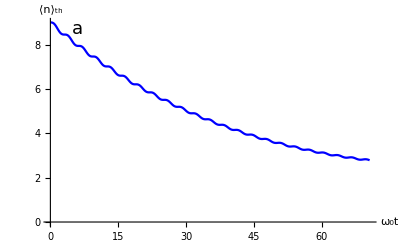

```mathematica
pbbb8=ListPlot[data8, Joined->True,PlotStyle->{Blue},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩_th",Black,18]},TicksStyle->Directive[Black],Epilog->{Inset[Style["a",18,Black],Scaled[{0.1,0.95}]]}]
```

```mathematica
(*=============================================================================================================================================*)
```

```mathematica
NTm=.;nta=6;SolTh=.;gamma=0;w0=1;dt=0.001Pi;dw=0.01 w0;
wd=2w0 ;wa[ta_]:=w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi]];phi=Pi/2;For[k=1,k<10001,k++,NTm[k]=RandomVariate[ExponentialDistribution[(1/(1+nta))],1][[1]];nj=1;SolTh[k]=NDSolve[{xa'[ta]==pa[ta]-gamma/2xa[ta],pa'[ta]==-wa[ta]^2xa[ta]-gamma/2 pa[ta],sxxa'[ta]==2sxpa[ta]- gamma sxxa[ta]+gamma (2nt+1)/(2wa[ta]),sxpa'[ta]==sppa[ta]-sxxa[ta]wa[ta]^2-gamma sxpa[ta],sppa'[ta]==-gamma sppa[ta] +gamma (2nt+1)wa[ta]/2-2sxpa[ta]wa[ta]^2,sxxa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==(1)/(2w0),sppa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==w0(1)/2,sxpa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0,xa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==Sqrt[2*NTm[k]/w0],pa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0},{xa,pa,sxxa,sppa,sxpa},{ta,dt IntegerPart[50Pi/(wd dt)(nj-1)],IntegerPart[50Pi/(wd dt)(nj)]dt}];plot[k]=Plot[Evaluate[(wa[ta]^2((sxxa[ta]/.SolTh[k])+(xa[ta]/.SolTh[k])^2)+((sppa[ta]/.SolTh[k])+(pa[ta]/.SolTh[k])^2))/(2wa[ta])-1/2],{ta,dt IntegerPart[50Pi(0)/(wd dt)],dt IntegerPart[50Pi/(wd dt)]},PlotRange->All,PlotStyle->Blue];
finalN0[k]=Evaluate[(wa[dt IntegerPart[0Pi/(wd dt)]]^2((sxxa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[0Pi/(wd dt)]])-1/2][[1]];finalN5[k]=Evaluate[(wa[dt IntegerPart[5Pi/(wd dt)]]^2((sxxa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[5Pi/(wd dt)]])-1/2][[1]];finalN10[k]=Evaluate[(wa[dt IntegerPart[10Pi/(wd dt)]]^2((sxxa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[10Pi/(wd dt)]])-1/2][[1]];finalN15[k]=Evaluate[(wa[dt IntegerPart[15Pi/(wd dt)]]^2((sxxa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[15Pi/(wd dt)]])-1/2][[1]];finalN20[k]=Evaluate[(wa[dt IntegerPart[20Pi/(wd dt)]]^2((sxxa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[20Pi/(wd dt)]])-1/2][[1]];finalN25[k]=Evaluate[(wa[dt IntegerPart[25Pi/(wd dt)]]^2((sxxa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[25Pi/(wd dt)]])-1/2][[1]];finalN30[k]=Evaluate[(wa[dt IntegerPart[30Pi/(wd dt)]]^2((sxxa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[30Pi/(wd dt)]])-1/2][[1]];finalN35[k]=Evaluate[(wa[dt IntegerPart[35Pi/(wd dt)]]^2((sxxa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[35Pi/(wd dt)]])-1/2][[1]];finalN40[k]=Evaluate[(wa[dt IntegerPart[40Pi/(wd dt)]]^2((sxxa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[40Pi/(wd dt)]])-1/2][[1]];finalN45[k]=Evaluate[(wa[dt IntegerPart[45Pi/(wd dt)]]^2((sxxa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2))/(2wa[dt IntegerPart[45Pi/(wd dt)]])-1/2][[1]];];tabth={{dt IntegerPart[0Pi/(wd dt)],Mean[Table[finalN0[k],{k,1,10000}]]},{dt IntegerPart[5Pi/(wd dt)],Mean[Table[finalN5[k],{k,1,10000}]]},{dt IntegerPart[10Pi/(wd dt)],Mean[Table[finalN10[k],{k,1,10000}]]},{dt IntegerPart[15Pi/(wd dt)],Mean[Table[finalN15[k],{k,1,10000}]]},{dt IntegerPart[20Pi/(wd dt)],Mean[Table[finalN20[k],{k,1,10000}]]},{dt IntegerPart[25Pi/(wd dt)],Mean[Table[finalN25[k],{k,1,10000}]]},{dt IntegerPart[30Pi/(wd dt)],Mean[Table[finalN30[k],{k,1,10000}]]},{dt IntegerPart[35Pi/(wd dt)],Mean[Table[finalN35[k],{k,1,10000}]]},{dt IntegerPart[40Pi/(wd dt)],Mean[Table[finalN40[k],{k,1,10000}]]},{dt IntegerPart[45Pi/(wd dt)],Mean[Table[finalN45[k],{k,1,10000}]]}}
```

```mathematica
tabth6={{0.,6.975595166593703},{7.850840041320893,5.967195385282571},{15.704821675295376,5.121018135708003},{23.55880330926986,4.411178055993695},{31.412784943244343,3.825010146637053},{39.266766577218824,3.3439747786695313},{47.12074821119331,2.9594912541620557},{54.97472984516779,2.659397373424154},{62.82871147914228,2.4383412841875938},{70.68269311311676,2.2893292727390975}};
```

## Average cooling starting from a thermal state of mean quanta n̄=6, numerical simulations.

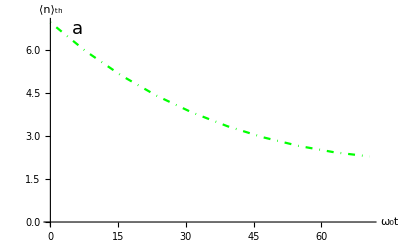

```mathematica
p11a6=ListPlot[tabth6,Joined->True,PlotRange->All,PlotStyle->{Green,DotDashed},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩_th",Black,18]},TicksStyle->Directive[Black],Epilog->{Inset[Style["a",18,Black],Scaled[{0.1,0.95}]]}]
```

## Here we generate the data using corresponding theory prediction.

```mathematica
myd2 = 0.01 w0;nta=6;
myϕd = π/2;
myμ = .;D2[t_] = d2 Cos[ωd t + ϕd] /.ωd-> 2;P11[t_] = Exp[- d2 t]((Exp[ 2 d2 t]- 1)(Sin[t + ϕd] - d2 Sin[t]) + d2( Exp[2 d2 t ] + 1) Cos[t + ϕd]- (Exp[2 d2 t] + 1)Cos[t])/(2 (d2 Cos[ϕd]  - 1));
IP22[t_] = Exp[- d2 t]( (Exp[2 d2 t] - 1)Cos[t + ϕd]- (Exp[2d2 t] + 1)Sin[t])/(2 (d2 Cos[ϕd]- 1));α[t_] =(P11[t]- I IP22[t] + I D[P11[tp]- I IP22[tp],tp] /.tp-> t)/2;
β[t_] = (P11[t]+ I IP22[t] + I D[P11[tp]+ I IP22[tp],tp] /.tp-> t)/2;b[t_] = α[t] μ + β[t]Conjugate[μ];
bdb[t_] = (Abs[α[t]]^2 + Abs[β[t]]^2)Abs[μ]^2   + Conjugate[α[t]] β[t]Conjugate[μ]^2 + α[t]Conjugate[β[t]]μ^2 + Abs[β[t]]^2;
b2[t_] = α[t]^2 μ^2 + α[t]β[t](2 Abs[μ]^2 + 1) + β[t]^2 Conjugate[μ]^2;
params = {d2-> myd2,ϕd-> myϕd,μ->Sqrt[nmjh]};data = Table[{t,Integrate[Exp[-nmjh/(nta+1)]/((nta+1))(bdb[t]/.params),{nmjh,0,Infinity}]},{t,0,dt IntegerPart[45Pi/(wd dt)],0.1}]
```

```mathematica
data06={{0.,7.},{0.1,6.9998871046488675},{0.2,6.999182920924053},{0.30000000000000004,6.997362649017698},{0.4,6.99394918137301},{0.5,6.988531893727157},{0.6000000000000001,6.980782715907391},{0.7000000000000001,6.970468853816234},{0.8,6.957461669790211},{0.9,6.941741383330511},{1.,6.9233974218479695},{1.1,6.902624424817935},{1.2000000000000002,6.879714077665101},{1.3,6.85504311691806},{1.4000000000000001,6.829057999145372},{1.5,6.802256856959447},{1.6,6.775169470829346},{1.7000000000000002,6.748336061483856},{1.8,6.722285751404133},{1.9000000000000001,6.6975155536900495},{2.,6.674470722182196},{2.1,6.653527239239563},{2.2,6.63497712942971},{2.3000000000000003,6.619017172213085},{2.4000000000000004,6.60574144918583},{2.5,6.595138007146048},{2.6,6.58708975337333},{2.7,6.581379530661458},{2.8000000000000003,6.577699153553647},{2.9000000000000004,6.575662030495475},{3.,6.574818855440999},{3.1,6.574675732377957},{3.2,6.574714001970807},{3.3000000000000003,6.574410974704285},{3.4000000000000004,6.573260742005842},{3.5,6.570794237015938},{3.6,6.566597749820626},{3.7,6.560329166612176},{3.8000000000000003,6.551731295702985},{3.9000000000000004,6.540641761752527},{4.,6.526999088166367},{4.1000000000000005,6.510844740794855},{4.2,6.492321067646176},{4.3,6.4716652328713895},{4.4,6.449199402263529},{4.5,6.425317585631748},{4.6000000000000005,6.400469672815169},{4.7,6.375143309627677},{4.800000000000001,6.349844343403838},{4.9,6.325076621834031},{5.,6.301321951400655},{5.1000000000000005,6.279021012182042},{5.2,6.258555984582728},{5.300000000000001,6.240235572444463},{5.4,6.224283008937194},{5.5,6.210827510633367},{5.6000000000000005,6.19989950613485},{5.7,6.191429814154102},{5.800000000000001,6.18525278812437},{5.9,6.181113286532212},{6.,6.178677176511191},{6.1000000000000005,6.177544938816758},{6.2,6.177267820617788},{6.300000000000001,6.17736588336072},{6.4,6.177347220144641},{6.5,6.176727573382915},{6.6000000000000005,6.175049570640628},{6.7,6.17190081481837},{6.800000000000001,6.166930113451203},{6.9,6.159861208753776},{7.,6.150503471998817},{7.1000000000000005,6.138759148711271},{7.2,6.124626880022247},{7.300000000000001,6.108201374767895},{7.4,6.089669260560128},{7.5,6.069301293968516},{7.6000000000000005,6.047441254099358},{7.7,6.024491974533823},{7.800000000000001,6.000899080647468},{7.9,5.9771330883926055},{8.,5.953670583231174},{8.1,5.930975231671948},{8.200000000000001,5.9094793815627495},{8.3,5.889566980886964},{8.4,5.8715584894832675},{8.5,5.855698376162899},{8.6,5.84214568850542},{8.700000000000001,5.830968058447663},{8.8,5.822139368656569},{8.9,5.815541158144487},{9.,5.810967696508091},{9.1,5.8081345104904125},{9.200000000000001,5.8066900100617875},{9.3,5.806229739284581},{9.4,5.806312674661835},{9.5,5.806478914475839},{9.600000000000001,5.806268049858094},{9.700000000000001,5.805237483992261},{9.8,5.802979970793491},{9.9,5.7991396783192055},{10.,5.793426143585591},{10.100000000000001,5.785625571838521},{10.200000000000001,5.775609041124256},{10.3,5.763337297850424},{10.4,5.748861965888824},{10.5,5.732323135155658},{10.600000000000001,5.713943439782891},{10.700000000000001,5.694018875226736},{10.8,5.672906732426673},{10.9,5.651011140348513},{11.,5.628766801474674},{11.100000000000001,5.606621574413646},{11.200000000000001,5.585018601110538},{11.3,5.564378691533332},{11.4,5.545083665679725},{11.5,5.527461311928502},{11.600000000000001,5.511772553878843},{11.700000000000001,5.498201327643464},{11.8,5.486847561766068},{11.9,5.477723526964481},{12.,5.470753687788783},{12.100000000000001,5.465778048444233},{12.200000000000001,5.462558846042622},{12.3,5.4607903119394585},{12.4,5.460111100838558},{12.5,5.4601188827673575},{12.600000000000001,5.460386508942474},{12.700000000000001,5.460479102220613},{12.8,5.459971388572642},{12.9,5.458464579088997},{13.,5.4556021325931665},{13.100000000000001,5.451083776079933},{13.200000000000001,5.444677231929109},{13.3,5.436227194222874},{13.4,5.425661207717815},{13.5,5.412992227596036},{13.600000000000001,5.398317771036488},{13.700000000000001,5.381815707587218},{13.8,5.363736868861938},{13.9,5.344394783926829},{14.,5.32415295990938},{14.100000000000001,5.303410223397455},{14.200000000000001,5.2825847133495785},{14.3,5.262097167597955},{14.4,5.2423541706427965},{14.5,5.223732029391081},{14.600000000000001,5.206561915929494},{14.700000000000001,5.191116863539596},{14.8,5.177601126164576},{14.9,5.166142315534793},{15.,5.156786618049499},{15.100000000000001,5.1494972698177115},{15.200000000000001,5.144156337947199},{15.3,5.14056972444709},{15.4,5.138475181222194},{15.5,5.137553005658522},{15.600000000000001,5.137438980928859},{15.700000000000001,5.13773903752307},{15.8,5.138045046048597},{15.9,5.1379511086134535},{16.,5.137069698706222},{16.1,5.135047008019044},{16.2,5.131576892681232},{16.3,5.1264128694313795},{16.400000000000002,5.119377691952047},{16.5,5.110370135669744},{16.6,5.099368731811508},{16.7,5.086432313877419},{16.8,5.07169736702986},{16.900000000000002,5.055372298130395},{17.,5.037728866212721},{17.1,5.019091125229487},{17.2,4.999822328533033},{17.3,4.980310323916801},{17.400000000000002,4.96095202606827},{17.5,4.9421375877395715},{17.6,4.924234900547565},{17.7,4.907575040785024},{17.8,4.892439235672229},{17.900000000000002,4.879047862786902},{18.,4.867551912560958},{18.1,4.858027244098117},{18.2,4.850471852174639},{18.3,4.844806242656294},{18.400000000000002,4.840876889528451},{18.5,4.838462624239784},{18.6,4.837283691971564},{18.7,4.83701310435609},{18.8,4.837289828219453},{18.900000000000002,4.837733278634957},{19.,4.8379585347092515},{19.1,4.837591669985541},{19.200000000000003,4.836284587103622},{19.3,4.833728768402217},{19.400000000000002,4.8296673995147765},{19.5,4.823905389803054},{19.6,4.816316898954072},{19.700000000000003,4.806850079764372},{19.8,4.795528858986655},{19.900000000000002,4.782451696626554},{20.,4.767787384511473},{20.1,4.751768062510653},{20.200000000000003,4.734679740800754},{20.3,4.716850714696368},{20.400000000000002,4.698638340941449},{20.5,4.6804147077687555},{20.6,4.662551773029101},{20.700000000000003,4.645406563681321},{20.8,4.629307025249157},{20.900000000000002,4.614539081768186},{21.,4.601335416471014},{21.1,4.589866413075169},{21.200000000000003,4.580233609921975},{21.3,4.5724659179163165},{21.400000000000002,4.566518742317938},{21.5,4.562276032382656},{21.6,4.5595551662824985},{21.700000000000003,4.558114466286239},{21.8,4.557663035313905},{21.900000000000002,4.557872514789875},{22.,4.55839028878885},{22.1,4.558853603716944},{22.200000000000003,4.558904038341949},{22.3,4.558201747171453},{22.400000000000002,4.5564389113606945},{22.5,4.5533518649817735},{22.6,4.548731419179623},{22.700000000000003,4.5424309802231875},{22.8,4.534372146739},{22.900000000000002,4.524547572877848},{23.,4.513020993732443},{23.1,4.499924422604897},{23.200000000000003,4.485452642198645},{23.3,4.469855219007929},{23.400000000000002,4.4534263678551795},{23.5,4.436493077832667},{23.6,4.419401978535959},{23.700000000000003,4.402505473804577},{23.8,4.386147697360599},{23.900000000000002,4.37065084975524},{24.,4.356302458780913},{24.1,4.343344066750419},{24.200000000000003,4.331961789407924},{24.3,4.322279115124662},{24.400000000000002,4.314352222538258},{24.5,4.308167993572099},{24.6,4.303644790885526},{24.700000000000003,4.300635958574337},{24.8,4.298935896756631},{24.900000000000002,4.298288458837737},{25.,4.298397328777263},{25.1,4.2989379581812655},{25.200000000000003,4.299570582543972},{25.3,4.299953794810493},{25.400000000000002,4.299758134189101},{25.5,4.29867914953766},{25.6,4.2964494195472955},{25.700000000000003,4.292849055357775},{25.8,4.287714273360273},{25.900000000000002,4.280943704234208},{26.,4.272502195552183},{26.1,4.262421965890689},{26.200000000000003,4.250801074269339},{26.3,4.23779927567524},{26.400000000000002,4.223631437155603},{26.5,4.208558785365594},{26.6,4.192878341732721},{26.700000000000003,4.176910972192113},{26.8,4.160988531996537},{26.900000000000002,4.145440620343659},{27.,4.130581473200501},{27.1,4.116697515273312},{27.200000000000003,4.104036063944317},{27.3,4.092795630368018},{27.400000000000002,4.083118197756407},{27.5,4.075083776839334},{27.6,4.068707446802605},{27.700000000000003,4.0639389903708825},{27.8,4.060665128107986},{27.900000000000002,4.058714253588079},{28.,4.0578634719612205},{28.1,4.057847653522883},{28.200000000000003,4.0583701347857},{28.3,4.059114635346872},{28.400000000000002,4.059757912045735},{28.5,4.0599826443115},{28.6,4.059490037238816},{28.700000000000003,4.05801164201793},{28.8,4.055319926292242},{28.900000000000002,4.051237178436364},{29.,4.0456423975301945},{29.1,4.038475902193768},{29.200000000000003,4.02974148315699},{29.3,4.019506022782821},{29.400000000000002,4.007896605806325},{29.5,3.9950952452662056},{29.6,3.9813314420288495},{29.700000000000003,3.9668728817004713},{29.8,3.9520146457269427},{29.900000000000002,3.937067371233652},{30.,3.9223448344175105},{30.1,3.9081514535307824},{30.200000000000003,3.894770208916969},{30.3,3.8824514591855643},{30.400000000000002,3.8714030952485063},{30.5,3.8617824191397148},{30.6,3.853690064542875},{30.700000000000003,3.847166193600294},{30.8,3.842189113186321},{30.900000000000002,3.8386763570709834},{31.,3.836488182139326},{31.1,3.8354333309848583},{31.200000000000003,3.835276823563613},{31.3,3.835749460722759},{31.400000000000002,3.8365586554461064},{31.5,3.8374001562060616},{31.6,3.8379701928691894},{31.700000000000003,3.837977560458344},{31.8,3.837155160263599},{31.900000000000002,3.835270541082383},{32.,3.832135024761542},{32.1,3.827611058000701},{32.2,3.821617504200342},{32.300000000000004,3.8141326720933484},{32.4,3.8051949686463553},{32.5,3.794901158620175},{32.6,3.783402308447672},{32.7,3.7708975839318266},{32.800000000000004,3.757626156045755},{32.9,3.7438575434828354},{33.,3.72988078163729},{33.1,3.7159928530138133},{33.2,3.7024868419206616},{33.300000000000004,3.6896402856482715},{33.4,3.6777041848677694},{33.5,3.666893108142659},{33.6,3.657376780405285},{33.7,3.6492734848575825},{33.800000000000004,3.6426455344700446},{33.9,3.6374969860328585},{34.,3.633773679903515},{34.1,3.631365595791239},{34.2,3.630111422821316},{34.300000000000004,3.629805154392889},{34.4,3.6302044384558805},{34.5,3.6310403449365163},{34.6,3.632028156838847},{34.7,3.6328787521893773},{34.800000000000004,3.6333101219844046},{34.9,3.633058565459902},{35.,3.6318891184218005},{35.1,3.6296048024138754},{35.2,3.626054330825776},{35.300000000000004,3.6211379706771276},{35.4,3.6148113332145537},{35.5,3.6070869496273197},{35.6,3.5980335767856033},{35.7,3.587773268392725},{35.800000000000004,3.5764763357094274},{35.9,3.564354405535512},{36.,3.5516518581125984},{36.1,3.5386359910917315},{36.2,3.5255863052048024},{36.300000000000004,3.5127833408675673},{36.4,3.5004975113448094},{36.5,3.4889783767288045},{36.6,3.478444783938101},{36.7,3.469076262051192},{36.800000000000004,3.4610060110337493},{36.9,3.4543157573901535},{37.,3.4490326750805527},{37.1,3.445128487221034},{37.2,3.442520776945819},{37.300000000000004,3.4410764478378035},{37.4,3.4406171890278454},{37.5,3.4409267208087746},{37.6,3.4417595265380085},{37.7,3.4428507184690904},{37.800000000000004,3.4439266412296905},{37.9,3.444715788649812},{38.,3.4449595986009602},{38.1,3.444422696816064},{38.2,3.4429021840126084},{38.300000000000004,3.4402356000517345},{38.400000000000006,3.4363072527126977},{38.5,3.431052664755477},{38.6,3.4244609686152696},{38.7,3.416575160278813},{38.800000000000004,3.407490209344049},{38.900000000000006,3.3973491075510514},{39.,3.386337019802947},{39.1,3.374673776631635},{39.2,3.362605012246813},{39.300000000000004,3.350392305178215},{39.400000000000006,3.338302717017807},{39.5,3.3265981474077795},{39.6,3.3155249293529594},{39.7,3.3053040779828944},{39.800000000000004,3.2961225785388737},{39.900000000000006,3.288126056758443},{40.,3.2814131187166033},{40.1,3.27603157983679},{40.2,3.2719767269198674},{40.300000000000004,3.269191675701229},{40.400000000000006,3.2675698028874804},{40.5,3.2669591491749865},{40.6,3.2671686116888052},{40.7,3.2679756736917676},{40.800000000000004,3.2691353590834},{40.900000000000006,3.2703900515020963},{41.,3.2714797846187342},{41.1,3.2721525927390456},{41.2,3.2721745097602506},{41.300000000000004,3.2713388198437157},{41.400000000000006,3.2694741942077434},{41.5,3.266451393928053},{41.6,3.2621882767021346},{41.7,3.2566529138382507},{41.800000000000004,3.2498646995205145},{41.900000000000006,3.24189341464046},{42.,3.2328562889673225},{42.1,3.2229131849096073},{42.2,3.21226010044483},{42.300000000000004,3.201121255023461},{42.400000000000006,3.189740077778939},{42.5,3.178369460024159},{42.6,3.1672616621308967},{42.7,3.1566582774003265},{42.800000000000004,3.146780651992171},{42.900000000000006,3.1378211405786045},{43.,3.1299355429485014},{43.1,3.1232370187258582},{43.2,3.1177917176362175},{43.300000000000004,3.113616293770421},{43.400000000000006,3.110677396827145},{43.5,3.108893154386903},{43.6,3.108136580029826},{43.7,3.1082407657098643},{43.800000000000004,3.1090056462683835},{43.900000000000006,3.110206062097076},{44.,3.111600795176821},{44.1,3.1129422160111035},{44.2,3.113986155798085},{44.300000000000004,3.11450161042119},{44.400000000000006,3.114279890745153},{44.5,3.1131428569192856},{44.6,3.110949911942301},{44.7,3.1076034800953334},{44.800000000000004,3.1030527569601336},{44.900000000000006,3.097295587144075},{45.,3.0903784007477237},{45.1,3.0823942170375207},{45.2,3.0734788006393856},{45.300000000000004,3.063805128793985},{45.400000000000006,3.053576394910479},{45.5,3.0430178311903364},{45.6,3.0323676792057577},{45.7,3.02186767021078},{45.800000000000004,3.011753395367291},{45.900000000000006,3.002244949297349},{46.,2.9935382183431396},{46.1,2.985797158152304},{46.2,2.979147364817456},{46.300000000000004,2.9736711914321905},{46.400000000000006,2.9694045996996197},{46.5,2.966335866648439},{46.6,2.9644061923638647},{46.7,2.963512178889608},{46.800000000000004,2.963510076118828},{46.900000000000006,2.964221620518959},{47.,2.96544122969692},{47.1,2.966944262585042},{47.2,2.9684960135019067},{47.300000000000004,2.969861080133078},{47.400000000000006,2.9708127316666295},{47.5,2.9711419044135132},{47.6,2.97066546815658},{47.7,2.969233436526811},{47.800000000000004,2.9667348376651907},{47.900000000000006,2.9631020155469128},{48.,2.958313195436504},{48.1,2.9523932164733337},{48.2,2.945412407572154},{48.300000000000004,2.93748365674315},{48.400000000000006,2.928757795647584},{48.5,2.9194174878646377},{48.6,2.9096698683150737},{48.7,2.899738230246452},{48.800000000000004,2.889853093214202},{48.900000000000006,2.880243009154766},{49.,2.8711254730398794},{49.1,2.8626982993908383},{49.2,2.855131806369012},{49.300000000000004,2.8485621160618515},{49.400000000000006,2.843085834307543},{49.5,2.838756317781248},{49.6,2.8355816723427165},{49.7,2.833524557376265},{49.800000000000004,2.832503798809205},{49.900000000000006,2.832397741547141},{50.,2.8330492030743275},{50.1,2.8342718266698506},{50.2,2.8358575775860655},{50.300000000000004,2.8375850807936907},{50.400000000000006,2.8392284662667264},{50.5,2.840566368525344},{50.6,2.8413907220025423},{50.7,2.8415150029176117},{50.800000000000004,2.8407815913232395},{50.900000000000006,2.839067962891091},{51.,2.836291467349819},{51.1,2.832412507375192},{51.2,2.82743599586564},{51.300000000000004,2.8214110383486215},{51.400000000000006,2.814428858003898},{51.5,2.80661905064154},{51.6,2.798144323159551},{51.7,2.7891939289075327},{51.800000000000004,2.779976064632813},{51.900000000000006,2.77070953427079},{52.,2.761615013176541},{52.1,2.7529062613864235},{52.2,2.7447816355869366},{52.300000000000004,2.737416236647094},{52.400000000000006,2.7309550033881864},{52.5,2.725507024796906},{52.6,2.7211412936982513},{52.7,2.717884066976818},{52.800000000000004,2.7157179330965775},{52.900000000000006,2.7145826194951805},{53.,2.714377503139629},{53.1,2.714965719885072},{53.2,2.7161797049616645},{53.300000000000004,2.717827940432731},{53.400000000000006,2.7197026380488944},{53.5,2.7215880494284277},{53.6,2.723269071346739},{53.7,2.7245398030452943},{53.800000000000004,2.725211715270287},{53.900000000000006,2.7251211070764323},{54.,2.7241355555980014},{54.1,2.7221591048037355},{54.2,2.719135990062174},{54.300000000000004,2.7150527541028784},{54.400000000000006,2.7099386743100053},{54.5,2.7038644886550904},{54.6,2.6969394752786924},{54.7,2.6893070060732955},{54.800000000000004,2.68113875501004},{54.900000000000006,2.6726277950014783},{55.,2.6639808607099025},{55.1,2.6554100871866764},{55.2,2.647124554298046},{55.300000000000004,2.6393219737912372},{55.400000000000006,2.632180849339603},{55.5,2.6258534202699044},{55.6,2.6204596677321965},{55.7,2.616082619123606},{55.800000000000004,2.612765134357198},{55.900000000000006,2.6105082981749548},{56.,2.6092714785190347},{56.1,2.608974044562089},{56.2,2.609498672001253},{56.300000000000004,2.610696100264805},{56.400000000000006,2.612391148861149},{56.5,2.6143897504861586},{56.6,2.6164867186508},{56.7,2.618473939057212},{56.800000000000004,2.620148657845324},{56.900000000000006,2.6213215367638334},{57.,2.6218241553796027},{57.1,2.6215156631970618},{57.2,2.6202883190780217},{57.300000000000004,2.6180717002328033},{57.400000000000006,2.6148354164856973},{57.5,2.6105902253572593},{57.6,2.6053875073583033},{57.7,2.59931712620706},{57.800000000000004,2.5925037628617473},{57.900000000000006,2.5851018727564377},{58.,2.5772894700415394},{58.1,2.5692609888127245},{58.2,2.561219507446184},{58.300000000000004,2.5533686468302728},{58.400000000000006,2.545904465539763},{58.5,2.5390076743802954},{58.6,2.5328364792908022},{58.7,2.52752033589559},{58.800000000000004,2.5231548620939166},{58.900000000000006,2.5197981084568695},{59.,2.517468331744672},{59.1,2.516143356744494},{59.2,2.515761548263772},{59.300000000000004,2.5162243510216236},{59.400000000000006,2.517400292913345},{59.5,2.519130289150018},{59.6,2.5212340333935663},{59.7,2.523517219245183},{59.800000000000004,2.525779302982515},{59.900000000000006,2.52782149754745},{60.,2.529454679265681},{60.1,2.5305068929446097},{60.2,2.530830157652587},{60.300000000000004,2.5303063039422375},{60.400000000000006,2.528851612384872},{60.5,2.5264200714553153},{60.6,2.523005128110852},{60.7,2.518639864631146},{60.800000000000004,2.513395598021989},{60.900000000000006,2.507378961035888},{61.,2.5007275841306784},{61.1,2.493604553083563},{61.2,2.4861918653093658},{61.300000000000004,2.4786831472917656},{61.400000000000006,2.471275924378703},{61.5,2.4641637513932464},{61.6,2.457528517409339},{61.7,2.451533230468706},{61.800000000000004,2.4463155682977775},{61.900000000000006,2.4419824500308454},{62.,2.4386058428154493},{62.1,2.4362199676243113},{62.2,2.4348200126123687},{62.300000000000004,2.4343624021766312},{62.400000000000006,2.4347666079016155},{62.5,2.435918426272197},{62.6,2.43767458984493},{62.7,2.43986852579444},{62.800000000000004,2.442317030483089},{62.900000000000006,2.4448275927220506},{63.,2.4472060731152077},{63.1,2.449264433285169},{63.2,2.4508282073928354},{63.300000000000004,2.4517434192084973},{63.400000000000006,2.451882670618542},{63.5,2.4511501609355264},{63.6,2.4494854393676597},{63.7,2.446865743770047},{63.800000000000004,2.4433068353099845},{63.900000000000006,2.4388622986754305},{64.,2.4336213385468524},{64.10000000000001,2.4277051628068214},{64.2,2.4212620990061784},{64.3,2.4144616407186765},{64.4,2.407487662616291},{64.5,2.400531075721618},{64.60000000000001,2.393782216063029},{64.7,2.387423270026303},{64.8,2.3816210376848663},{64.9,2.3765203214016877},{65.,2.3722382016068},{65.10000000000001,2.3688594258959528},{65.2,2.3664330929082364},{65.3,2.364970760616457},{65.4,2.364446051776717},{65.5,2.364795769604432},{65.60000000000001,2.3659224766498452},{65.7,2.3676984317277876},{65.8,2.3699707259209086},{65.9,2.3725674112559023},{66.,2.3753043765229336},{66.10000000000001,2.377992695410455},{66.2,2.3804461538093875},{66.3,2.382488656511722},{66.4,2.383961218831842},{66.5,2.3847282656845454},{66.60000000000001,2.3846829886647978},{66.7,2.3837515495589447},{66.8,2.381895964952714},{66.9,2.379115559335612},{67.,2.375446931226535},{67.10000000000001,2.3709624360833903},{67.2,2.365767248751387},{67.3,2.359995124604983},{67.4,2.3538030301095243},{67.5,2.347364858227201},{67.60000000000001,2.340864480152026},{67.7,2.3344884108603043},{67.8,2.3284183808882415},{67.9,2.3228241100214273},{68.,2.3178565700895772},{68.10000000000001,2.3136420041606565},{68.2,2.3102769389296762},{68.3,2.3078243872284037},{68.4,2.306311389942764},{68.5,2.305727993119935},{68.60000000000001,2.3060276988148125},{68.7,2.307129369545329},{68.8,2.308920508434371},{68.9,2.3112617825091846},{69.,2.3139926073731347},{69.10000000000001,2.3169375695105106},{69.2,2.3199134294904242},{69.3,2.3227364265985666},{69.4,2.325229593836426},{69.5,2.3272297922293856},{69.60000000000001,2.3285941849632694},{69.7,2.3292058945448395},{69.8,2.3289786190393738},{69.9,2.327860025156153},{70.,2.3258337848601887},{70.10000000000001,2.3229201763304737},{70.2,2.3191752273018413},{70.3,2.3146884368399663},{70.4,2.309579168099481},{70.5,2.3039918573583993},{70.60000000000001,2.2980902315173037}};
```

## Average cooling starting from a thermal state of mean quanta n̄=6, theoretical prediction.

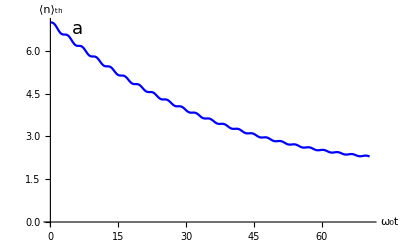

```mathematica
pbbb6=ListPlot[data06, Joined->True,PlotStyle->{Blue},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩_th",Black,18]},TicksStyle->Directive[Black],Epilog->{Inset[Style["a",18,Black],Scaled[{0.1,0.95}]]}]
```

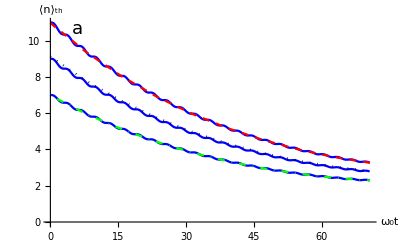

```mathematica
plta=Show[pbbb,pbbb8,pbbb6,p11a,p11a8,p11a6]
```

## 4. Simulations for cooling with phase errors.

We model the phase of feedback control as a Gaussian random variable around the true phase. Below we show multiple realizations of the cooling protocol with different degree of phase error in the feedback loop. Numerical simulations are compared with theoretical predictions.

```mathematica
NTm=.;nta=10;SolTh=.;gamma=0;phi=.;w0=1;dt=0.001Pi;dw=0.01 w0;
wd=2w0 ;For[k=1,k<10001,k++,phi[k]=RandomVariate[NormalDistribution[Pi/2,0.5Pi/2],1][[1]];nj=1;SolTh[k]=NDSolve[{xa'[ta]==pa[ta]-gamma/2xa[ta],pa'[ta]==-(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2xa[ta]-gamma/2 pa[ta],sxxa'[ta]==2sxpa[ta]- gamma sxxa[ta]+gamma (2nt+1)/(2(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])),sxpa'[ta]==sppa[ta]-sxxa[ta](w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2-gamma sxpa[ta],sppa'[ta]==-gamma sppa[ta] +gamma (2nt+1)(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])/2-2sxpa[ta](w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2,sxxa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==(1)/(2w0),sppa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==w0(1)/2,sxpa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0,xa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==Sqrt[2*nta/w0],pa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0},{xa,pa,sxxa,sppa,sxpa},{ta,dt IntegerPart[50Pi/(wd dt)(nj-1)],IntegerPart[50Pi/(wd dt)(nj)]dt}];plot[k]=Plot[Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2((sxxa[ta]/.SolTh[k])+(xa[ta]/.SolTh[k])^2)+((sppa[ta]/.SolTh[k])+(pa[ta]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]]))-1/2],{ta,dt IntegerPart[50Pi(0)/(wd dt)],dt IntegerPart[50Pi/(wd dt)]},PlotRange->All,PlotStyle->Blue];
finalN0[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[0Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[0Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN5[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[5Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[5Pi/(wd dt)])+phi[k]]]))-1/2][[1]];

finalN10[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[10Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[10Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN15[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[15Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[15Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN20[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[20Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[20Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN25[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[25Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[25Pi/(wd dt)])+phi[k]]]))-1/2][[1]];

finalN30[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[30Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[30Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN35[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[35Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[35Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN40[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[40Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[40Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN45[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[45Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[45Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
]
```

```mathematica
Mean[Table[finalN0[k],{k,1,10000}]]
```

10.1981

```mathematica
tab0p5={{dt IntegerPart[0Pi/(wd dt)],Mean[Table[finalN0[k],{k,1,10000}]]},{dt IntegerPart[5Pi/(wd dt)],Mean[Table[finalN5[k],{k,1,10000}]]},{dt IntegerPart[10Pi/(wd dt)],Mean[Table[finalN10[k],{k,1,10000}]]},{dt IntegerPart[15Pi/(wd dt)],Mean[Table[finalN15[k],{k,1,10000}]]},{dt IntegerPart[20Pi/(wd dt)],Mean[Table[finalN20[k],{k,1,10000}]]},{dt IntegerPart[25Pi/(wd dt)],Mean[Table[finalN25[k],{k,1,10000}]]},{dt IntegerPart[30Pi/(wd dt)],Mean[Table[finalN30[k],{k,1,10000}]]},{dt IntegerPart[35Pi/(wd dt)],Mean[Table[finalN35[k],{k,1,10000}]]},{dt IntegerPart[40Pi/(wd dt)],Mean[Table[finalN40[k],{k,1,10000}]]},{dt IntegerPart[45Pi/(wd dt)],Mean[Table[finalN45[k],{k,1,10000}]]}}
```

```mathematica
tab0p5={{0.,9.99970322502204},{7.850840041320893,8.972752674227078},{15.704821675295376,8.174520928924647},{23.55880330926986,7.595763451540642},{31.412784943244343,7.21182011668317},{39.266766577218824,7.024246263649566},{47.12074821119331,7.016730966913639},{54.97472984516779,7.201334629591445},{62.82871147914228,7.569841976877516},{70.68269311311676,8.14464885535609}};
```

## Average cooling starting from a coherent state of mean quanta n̄=10, with Δϕ=0.5ϕ_p, numerical simulations.

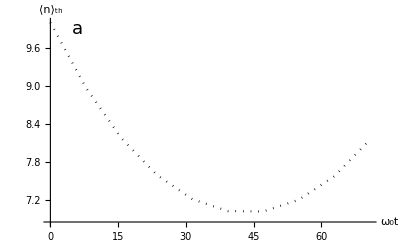

```mathematica
psafa0p5=ListPlot[tab0p5,Joined->True,PlotRange->All,PlotStyle->{Black,Dotted},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩_th",Black,18]},TicksStyle->Directive[Black],Epilog->{Inset[Style["a",18,Black],Scaled[{0.1,0.95}]]}]
```

## Here we generate the data using corresponding theory prediction, when phase errors are accounted for.

```mathematica
D2[t_] = d2 Cos[ωd t + ϕd] /.ωd-> 2;P11[t_] = Exp[- d2 t]((Exp[ 2 d2 t]- 1)(Sin[t + ϕd] - d2 Sin[t]) + d2( Exp[2 d2 t ] + 1) Cos[t + ϕd]- (Exp[2 d2 t] + 1)Cos[t])/(2 (d2 Cos[ϕd]  - 1));
IP22[t_] = Exp[- d2 t]( (Exp[2 d2 t] - 1)Cos[t + ϕd]- (Exp[2d2 t] + 1)Sin[t])/(2 (d2 Cos[ϕd]- 1));α[t_] =(P11[t]- I IP22[t] + I D[P11[tp]- I IP22[tp],tp] /.tp-> t)/2;
β[t_] = (P11[t]+ I IP22[t] + I D[P11[tp]+ I IP22[tp],tp] /.tp-> t)/2;b[t_] = α[t] μ + β[t]Conjugate[μ];
bdb[t_] = (Abs[α[t]]^2 + Abs[β[t]]^2)Abs[μ]^2   + Conjugate[α[t]] β[t]Conjugate[μ]^2 + α[t]Conjugate[β[t]]μ^2 + Abs[β[t]]^2;
b2[t_] = α[t]^2 μ^2 + α[t]β[t](2 Abs[μ]^2 + 1) + β[t]^2 Conjugate[μ]^2;myd2 = 0.01 w0;
myϕd = π/2;
myμ = Sqrt[10];
params = {d2-> myd2,ϕd-> pha,μ->myμ };data0p5 = Table[{t,NIntegrate[PDF[NormalDistribution[Pi/2,0.5Pi/2],pha](bdb[t]/.params),{pha,-Infinity,Infinity}]},{t,0,dt IntegerPart[45Pi/(wd dt)],0.1}];
```

```mathematica
(*====================================================================================================================================================================================*)
```

```mathematica
NTm=.;nta=10;SolTh=.;gamma=0;phi=.;w0=1;dt=0.001Pi;dw=0.01 w0;
wd=2w0 ;For[k=1,k<10001,k++,phi[k]=RandomVariate[NormalDistribution[Pi/2,0.4Pi/2],1][[1]];nj=1;SolTh[k]=NDSolve[{xa'[ta]==pa[ta]-gamma/2xa[ta],pa'[ta]==-(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2xa[ta]-gamma/2 pa[ta],sxxa'[ta]==2sxpa[ta]- gamma sxxa[ta]+gamma (2nt+1)/(2(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])),sxpa'[ta]==sppa[ta]-sxxa[ta](w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2-gamma sxpa[ta],sppa'[ta]==-gamma sppa[ta] +gamma (2nt+1)(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])/2-2sxpa[ta](w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2,sxxa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==(1)/(2w0),sppa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==w0(1)/2,sxpa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0,xa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==Sqrt[2*nta/w0],pa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0},{xa,pa,sxxa,sppa,sxpa},{ta,dt IntegerPart[50Pi/(wd dt)(nj-1)],IntegerPart[50Pi/(wd dt)(nj)]dt}];plot[k]=Plot[Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2((sxxa[ta]/.SolTh[k])+(xa[ta]/.SolTh[k])^2)+((sppa[ta]/.SolTh[k])+(pa[ta]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]]))-1/2],{ta,dt IntegerPart[50Pi(0)/(wd dt)],dt IntegerPart[50Pi/(wd dt)]},PlotRange->All,PlotStyle->Blue];
finalN0[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[0Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[0Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN5[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[5Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[5Pi/(wd dt)])+phi[k]]]))-1/2][[1]];

finalN10[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[10Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[10Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN15[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[15Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[15Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN20[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[20Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[20Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN25[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[25Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[25Pi/(wd dt)])+phi[k]]]))-1/2][[1]];

finalN30[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[30Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[30Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN35[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[35Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[35Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN40[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[40Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[40Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN45[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[45Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[45Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
];tab0p4={{dt IntegerPart[0Pi/(wd dt)],Mean[Table[finalN0[k],{k,1,10000}]]},{dt IntegerPart[5Pi/(wd dt)],Mean[Table[finalN5[k],{k,1,10000}]]},{dt IntegerPart[10Pi/(wd dt)],Mean[Table[finalN10[k],{k,1,10000}]]},{dt IntegerPart[15Pi/(wd dt)],Mean[Table[finalN15[k],{k,1,10000}]]},{dt IntegerPart[20Pi/(wd dt)],Mean[Table[finalN20[k],{k,1,10000}]]},{dt IntegerPart[25Pi/(wd dt)],Mean[Table[finalN25[k],{k,1,10000}]]},{dt IntegerPart[30Pi/(wd dt)],Mean[Table[finalN30[k],{k,1,10000}]]},{dt IntegerPart[35Pi/(wd dt)],Mean[Table[finalN35[k],{k,1,10000}]]},{dt IntegerPart[40Pi/(wd dt)],Mean[Table[finalN40[k],{k,1,10000}]]},{dt IntegerPart[45Pi/(wd dt)],Mean[Table[finalN45[k],{k,1,10000}]]}}
```

```mathematica
tab0p4={{0.,10.001108695994867},{7.850840041320893,8.837003420354822},{15.704821675295376,7.9002339271525575},{23.55880330926986,7.174110494472975},{31.412784943244343,6.634335068556},{39.266766577218824,6.274713868004694},{47.12074821119331,6.078481786932942},{54.97472984516779,6.0493227497273825},{62.82871147914228,6.17736612894036},{70.68269311311676,6.475510243799148}};
```

## Average cooling starting from a coherent state of mean quanta n̄=10, with Δϕ=0.4ϕ_p, numerical simulations.

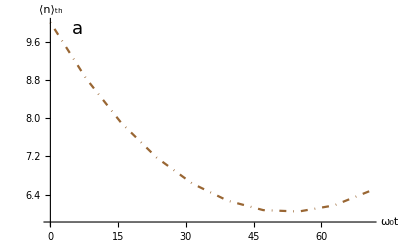

```mathematica
psafa0p4=ListPlot[tab0p4,Joined->True,PlotRange->All,PlotStyle->{Brown,DotDashed},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩_th",Black,18]},TicksStyle->Directive[Black],Epilog->{Inset[Style["a",18,Black],Scaled[{0.1,0.95}]]}]
```

## Here we generate the data using corresponding theory prediction, when phase errors are accounted for.

```mathematica
D2[t_] = d2 Cos[ωd t + ϕd] /.ωd-> 2;P11[t_] = Exp[- d2 t]((Exp[ 2 d2 t]- 1)(Sin[t + ϕd] - d2 Sin[t]) + d2( Exp[2 d2 t ] + 1) Cos[t + ϕd]- (Exp[2 d2 t] + 1)Cos[t])/(2 (d2 Cos[ϕd]  - 1));
IP22[t_] = Exp[- d2 t]( (Exp[2 d2 t] - 1)Cos[t + ϕd]- (Exp[2d2 t] + 1)Sin[t])/(2 (d2 Cos[ϕd]- 1));α[t_] =(P11[t]- I IP22[t] + I D[P11[tp]- I IP22[tp],tp] /.tp-> t)/2;
β[t_] = (P11[t]+ I IP22[t] + I D[P11[tp]+ I IP22[tp],tp] /.tp-> t)/2;b[t_] = α[t] μ + β[t]Conjugate[μ];
bdb[t_] = (Abs[α[t]]^2 + Abs[β[t]]^2)Abs[μ]^2   + Conjugate[α[t]] β[t]Conjugate[μ]^2 + α[t]Conjugate[β[t]]μ^2 + Abs[β[t]]^2;
b2[t_] = α[t]^2 μ^2 + α[t]β[t](2 Abs[μ]^2 + 1) + β[t]^2 Conjugate[μ]^2;myd2 = 0.01 w0;
myϕd = π/2;
myμ = Sqrt[10];
params = {d2-> myd2,ϕd-> pha,μ->myμ };data0p4= Table[{t,NIntegrate[PDF[NormalDistribution[Pi/2,0.4Pi/2],pha](bdb[t]/.params),{pha,-Infinity,Infinity}]},{t,0,dt IntegerPart[45Pi/(wd dt)],0.1}];
```

```mathematica
(*=====================================================================================================================================================================================================*)
```

```mathematica
NTm=.;nta=10;SolTh=.;gamma=0;phi=.;w0=1;dt=0.001Pi;dw=0.01 w0;
wd=2w0 ;For[k=1,k<10001,k++,phi[k]=RandomVariate[NormalDistribution[Pi/2,0.3Pi/2],1][[1]];nj=1;SolTh[k]=NDSolve[{xa'[ta]==pa[ta]-gamma/2xa[ta],pa'[ta]==-(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2xa[ta]-gamma/2 pa[ta],sxxa'[ta]==2sxpa[ta]- gamma sxxa[ta]+gamma (2nt+1)/(2(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])),sxpa'[ta]==sppa[ta]-sxxa[ta](w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2-gamma sxpa[ta],sppa'[ta]==-gamma sppa[ta] +gamma (2nt+1)(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])/2-2sxpa[ta](w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2,sxxa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==(1)/(2w0),sppa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==w0(1)/2,sxpa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0,xa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==Sqrt[2*nta/w0],pa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0},{xa,pa,sxxa,sppa,sxpa},{ta,dt IntegerPart[50Pi/(wd dt)(nj-1)],IntegerPart[50Pi/(wd dt)(nj)]dt}];plot[k]=Plot[Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2((sxxa[ta]/.SolTh[k])+(xa[ta]/.SolTh[k])^2)+((sppa[ta]/.SolTh[k])+(pa[ta]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]]))-1/2],{ta,dt IntegerPart[50Pi(0)/(wd dt)],dt IntegerPart[50Pi/(wd dt)]},PlotRange->All,PlotStyle->Blue];
finalN0[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[0Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[0Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN5[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[5Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[5Pi/(wd dt)])+phi[k]]]))-1/2][[1]];

finalN10[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[10Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[10Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN15[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[15Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[15Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN20[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[20Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[20Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN25[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[25Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[25Pi/(wd dt)])+phi[k]]]))-1/2][[1]];

finalN30[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[30Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[30Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN35[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[35Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[35Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN40[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[40Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[40Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN45[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[45Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[45Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
];tab0p3={{dt IntegerPart[0Pi/(wd dt)],Mean[Table[finalN0[k],{k,1,10000}]]},{dt IntegerPart[5Pi/(wd dt)],Mean[Table[finalN5[k],{k,1,10000}]]},{dt IntegerPart[10Pi/(wd dt)],Mean[Table[finalN10[k],{k,1,10000}]]},{dt IntegerPart[15Pi/(wd dt)],Mean[Table[finalN15[k],{k,1,10000}]]},{dt IntegerPart[20Pi/(wd dt)],Mean[Table[finalN20[k],{k,1,10000}]]},{dt IntegerPart[25Pi/(wd dt)],Mean[Table[finalN25[k],{k,1,10000}]]},{dt IntegerPart[30Pi/(wd dt)],Mean[Table[finalN30[k],{k,1,10000}]]},{dt IntegerPart[35Pi/(wd dt)],Mean[Table[finalN35[k],{k,1,10000}]]},{dt IntegerPart[40Pi/(wd dt)],Mean[Table[finalN40[k],{k,1,10000}]]},{dt IntegerPart[45Pi/(wd dt)],Mean[Table[finalN45[k],{k,1,10000}]]}}
```

```mathematica
tab0p3={{0.,9.999903565356364},{7.850840041320893,8.71558411797954},{15.704821675295376,7.658062118686098},{23.55880330926986,6.802780162205291},{31.412784943244343,6.127080628742535},{39.266766577218824,5.616699020327351},{47.12074821119331,5.255747962145626},{54.97472984516779,5.039324449903847},{62.82871147914228,4.957365595446103},{70.68269311311676,5.013206755686425}};
```

## Average cooling starting from a coherent state of mean quanta n̄=10, with Δϕ=0.3ϕ_p, numerical simulations.

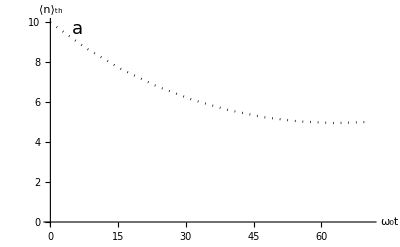

```mathematica
psafa0p3=ListPlot[tab0p3,Joined->True,PlotRange->All,PlotStyle->{Black,Dotted},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩_th",Black,18]},TicksStyle->Directive[Black],Epilog->{Inset[Style["a",18,Black],Scaled[{0.1,0.95}]]}]
```

## Here we generate the data using corresponding theory prediction, when phase errors are accounted for.

```mathematica
D2[t_] = d2 Cos[ωd t + ϕd] /.ωd-> 2;P11[t_] = Exp[- d2 t]((Exp[ 2 d2 t]- 1)(Sin[t + ϕd] - d2 Sin[t]) + d2( Exp[2 d2 t ] + 1) Cos[t + ϕd]- (Exp[2 d2 t] + 1)Cos[t])/(2 (d2 Cos[ϕd]  - 1));
IP22[t_] = Exp[- d2 t]( (Exp[2 d2 t] - 1)Cos[t + ϕd]- (Exp[2d2 t] + 1)Sin[t])/(2 (d2 Cos[ϕd]- 1));α[t_] =(P11[t]- I IP22[t] + I D[P11[tp]- I IP22[tp],tp] /.tp-> t)/2;
β[t_] = (P11[t]+ I IP22[t] + I D[P11[tp]+ I IP22[tp],tp] /.tp-> t)/2;b[t_] = α[t] μ + β[t]Conjugate[μ];
bdb[t_] = (Abs[α[t]]^2 + Abs[β[t]]^2)Abs[μ]^2   + Conjugate[α[t]] β[t]Conjugate[μ]^2 + α[t]Conjugate[β[t]]μ^2 + Abs[β[t]]^2;
b2[t_] = α[t]^2 μ^2 + α[t]β[t](2 Abs[μ]^2 + 1) + β[t]^2 Conjugate[μ]^2;myd2 = 0.01 w0;
myϕd = π/2;
myμ = Sqrt[10];
params = {d2-> myd2,ϕd-> pha,μ->myμ };data0p3 = Table[{t,NIntegrate[PDF[NormalDistribution[Pi/2,0.3Pi/2],pha](bdb[t]/.params),{pha,-Infinity,Infinity}]},{t,0,dt IntegerPart[45Pi/(wd dt)],0.1}];
```

```mathematica
(*=========================================================================================================================================================*)
```

```mathematica
NTm=.;nta=10;SolTh=.;gamma=0;phi=.;w0=1;dt=0.001Pi;dw=0.01 w0;
wd=2w0 ;For[k=1,k<10001,k++,phi[k]=RandomVariate[NormalDistribution[Pi/2,0.2Pi/2],1][[1]];nj=1;SolTh[k]=NDSolve[{xa'[ta]==pa[ta]-gamma/2xa[ta],pa'[ta]==-(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2xa[ta]-gamma/2 pa[ta],sxxa'[ta]==2sxpa[ta]- gamma sxxa[ta]+gamma (2nt+1)/(2(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])),sxpa'[ta]==sppa[ta]-sxxa[ta](w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2-gamma sxpa[ta],sppa'[ta]==-gamma sppa[ta] +gamma (2nt+1)(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])/2-2sxpa[ta](w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2,sxxa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==(1)/(2w0),sppa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==w0(1)/2,sxpa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0,xa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==Sqrt[2*nta/w0],pa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0},{xa,pa,sxxa,sppa,sxpa},{ta,dt IntegerPart[50Pi/(wd dt)(nj-1)],IntegerPart[50Pi/(wd dt)(nj)]dt}];plot[k]=Plot[Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2((sxxa[ta]/.SolTh[k])+(xa[ta]/.SolTh[k])^2)+((sppa[ta]/.SolTh[k])+(pa[ta]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]]))-1/2],{ta,dt IntegerPart[50Pi(0)/(wd dt)],dt IntegerPart[50Pi/(wd dt)]},PlotRange->All,PlotStyle->Blue];
finalN0[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[0Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[0Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN5[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[5Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[5Pi/(wd dt)])+phi[k]]]))-1/2][[1]];

finalN10[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[10Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[10Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN15[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[15Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[15Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN20[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[20Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[20Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN25[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[25Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[25Pi/(wd dt)])+phi[k]]]))-1/2][[1]];

finalN30[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[30Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[30Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN35[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[35Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[35Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN40[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[40Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[40Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN45[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[45Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[45Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
];tab0p2={{dt IntegerPart[0Pi/(wd dt)],Mean[Table[finalN0[k],{k,1,10000}]]},{dt IntegerPart[5Pi/(wd dt)],Mean[Table[finalN5[k],{k,1,10000}]]},{dt IntegerPart[10Pi/(wd dt)],Mean[Table[finalN10[k],{k,1,10000}]]},{dt IntegerPart[15Pi/(wd dt)],Mean[Table[finalN15[k],{k,1,10000}]]},{dt IntegerPart[20Pi/(wd dt)],Mean[Table[finalN20[k],{k,1,10000}]]},{dt IntegerPart[25Pi/(wd dt)],Mean[Table[finalN25[k],{k,1,10000}]]},{dt IntegerPart[30Pi/(wd dt)],Mean[Table[finalN30[k],{k,1,10000}]]},{dt IntegerPart[35Pi/(wd dt)],Mean[Table[finalN35[k],{k,1,10000}]]},{dt IntegerPart[40Pi/(wd dt)],Mean[Table[finalN40[k],{k,1,10000}]]},{dt IntegerPart[45Pi/(wd dt)],Mean[Table[finalN45[k],{k,1,10000}]]}}
```

```mathematica
tab0p2={{0.,10.000059419926322},{7.850840041320893,8.629108229417453},{15.704821675295376,7.484964673990915},{23.55880330926986,6.536645767249793},{31.412784943244343,5.763412395315745},{39.266766577218824,5.144481241813938},{47.12074821119331,4.665297668435928},{54.97472984516779,4.314092879347155},{62.82871147914228,4.0813568557003865},{70.68269311311676,3.9628558137700653}};
```

## Average cooling starting from a coherent state of mean quanta n̄=10, with Δϕ=0.2ϕ_p, numerical simulations.

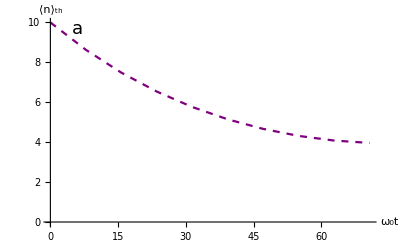

```mathematica
psafa0p2=ListPlot[tab0p2,Joined->True,PlotRange->All,PlotStyle->{Purple,Dashed},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩_th",Black,18]},TicksStyle->Directive[Black],Epilog->{Inset[Style["a",18,Black],Scaled[{0.1,0.95}]]}]
```

## Here we generate the data using corresponding theory prediction, when phase errors are accounted for.

```mathematica
D2[t_] = d2 Cos[ωd t + ϕd] /.ωd-> 2;P11[t_] = Exp[- d2 t]((Exp[ 2 d2 t]- 1)(Sin[t + ϕd] - d2 Sin[t]) + d2( Exp[2 d2 t ] + 1) Cos[t + ϕd]- (Exp[2 d2 t] + 1)Cos[t])/(2 (d2 Cos[ϕd]  - 1));
IP22[t_] = Exp[- d2 t]( (Exp[2 d2 t] - 1)Cos[t + ϕd]- (Exp[2d2 t] + 1)Sin[t])/(2 (d2 Cos[ϕd]- 1));α[t_] =(P11[t]- I IP22[t] + I D[P11[tp]- I IP22[tp],tp] /.tp-> t)/2;
β[t_] = (P11[t]+ I IP22[t] + I D[P11[tp]+ I IP22[tp],tp] /.tp-> t)/2;b[t_] = α[t] μ + β[t]Conjugate[μ];
bdb[t_] = (Abs[α[t]]^2 + Abs[β[t]]^2)Abs[μ]^2   + Conjugate[α[t]] β[t]Conjugate[μ]^2 + α[t]Conjugate[β[t]]μ^2 + Abs[β[t]]^2;
b2[t_] = α[t]^2 μ^2 + α[t]β[t](2 Abs[μ]^2 + 1) + β[t]^2 Conjugate[μ]^2;myd2 = 0.01 w0;
myϕd = π/2;
myμ = Sqrt[10];
params = {d2-> myd2,ϕd-> pha,μ->myμ };data0p2 = Table[{t,NIntegrate[PDF[NormalDistribution[Pi/2,0.2Pi/2],pha](bdb[t]/.params),{pha,-Infinity,Infinity}]},{t,0,dt IntegerPart[45Pi/(wd dt)],0.1}];
```

```mathematica
(*=============================================================================================================================================================================*)
```

```mathematica
NTm=.;nta=10;SolTh=.;gamma=0;phi=.;w0=1;dt=0.001Pi;dw=0.01 w0;
wd=2w0 ;For[k=1,k<10001,k++,phi[k]=RandomVariate[NormalDistribution[Pi/2,0.1Pi/2],1][[1]];nj=1;SolTh[k]=NDSolve[{xa'[ta]==pa[ta]-gamma/2xa[ta],pa'[ta]==-(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2xa[ta]-gamma/2 pa[ta],sxxa'[ta]==2sxpa[ta]- gamma sxxa[ta]+gamma (2nt+1)/(2(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])),sxpa'[ta]==sppa[ta]-sxxa[ta](w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2-gamma sxpa[ta],sppa'[ta]==-gamma sppa[ta] +gamma (2nt+1)(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])/2-2sxpa[ta](w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2,sxxa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==(1)/(2w0),sppa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==w0(1)/2,sxpa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0,xa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==Sqrt[2*nta/w0],pa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0},{xa,pa,sxxa,sppa,sxpa},{ta,dt IntegerPart[50Pi/(wd dt)(nj-1)],IntegerPart[50Pi/(wd dt)(nj)]dt}];plot[k]=Plot[Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2((sxxa[ta]/.SolTh[k])+(xa[ta]/.SolTh[k])^2)+((sppa[ta]/.SolTh[k])+(pa[ta]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]]))-1/2],{ta,dt IntegerPart[50Pi(0)/(wd dt)],dt IntegerPart[50Pi/(wd dt)]},PlotRange->All,PlotStyle->Blue];
finalN0[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[0Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[0Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN5[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[5Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[5Pi/(wd dt)])+phi[k]]]))-1/2][[1]];

finalN10[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[10Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[10Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN15[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[15Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[15Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN20[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[20Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[20Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN25[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[25Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[25Pi/(wd dt)])+phi[k]]]))-1/2][[1]];

finalN30[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[30Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[30Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN35[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[35Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[35Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN40[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[40Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[40Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN45[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[45Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[45Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
];tab0p1={{dt IntegerPart[0Pi/(wd dt)],Mean[Table[finalN0[k],{k,1,10000}]]},{dt IntegerPart[5Pi/(wd dt)],Mean[Table[finalN5[k],{k,1,10000}]]},{dt IntegerPart[10Pi/(wd dt)],Mean[Table[finalN10[k],{k,1,10000}]]},{dt IntegerPart[15Pi/(wd dt)],Mean[Table[finalN15[k],{k,1,10000}]]},{dt IntegerPart[20Pi/(wd dt)],Mean[Table[finalN20[k],{k,1,10000}]]},{dt IntegerPart[25Pi/(wd dt)],Mean[Table[finalN25[k],{k,1,10000}]]},{dt IntegerPart[30Pi/(wd dt)],Mean[Table[finalN30[k],{k,1,10000}]]},{dt IntegerPart[35Pi/(wd dt)],Mean[Table[finalN35[k],{k,1,10000}]]},{dt IntegerPart[40Pi/(wd dt)],Mean[Table[finalN40[k],{k,1,10000}]]},{dt IntegerPart[45Pi/(wd dt)],Mean[Table[finalN45[k],{k,1,10000}]]}}
```

```mathematica
tab0p1={{0.,10.000179290042428},{7.850840041320893,8.571579908227982},{15.704821675295376,7.370012973301107},{23.55880330926986,6.35980361299852},{31.412784943244343,5.521891591246605},{39.266766577218824,4.830772282018845},{47.12074821119331,4.273161309864666},{54.97472984516779,3.8323454760538946},{62.82871147914228,3.499572068211231},{70.68269311311676,3.265178450399112}};
```

## Average cooling starting from a coherent state of mean quanta n̄=10, with Δϕ=0.1ϕ_p, numerical simulations.

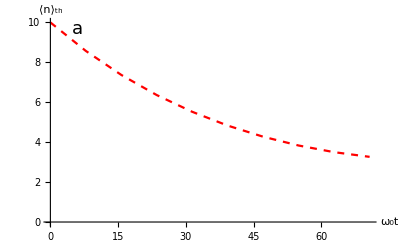

```mathematica
psafa0p1=ListPlot[tab0p1,Joined->True,PlotRange->All,PlotStyle->{Red,Dashed},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩_th",Black,18]},TicksStyle->Directive[Black],Epilog->{Inset[Style["a",18,Black],Scaled[{0.1,0.95}]]}]
```

## Here we generate the data using corresponding theory prediction, when phase errors are accounted for.

```mathematica
D2[t_] = d2 Cos[ωd t + ϕd] /.ωd-> 2;P11[t_] = Exp[- d2 t]((Exp[ 2 d2 t]- 1)(Sin[t + ϕd] - d2 Sin[t]) + d2( Exp[2 d2 t ] + 1) Cos[t + ϕd]- (Exp[2 d2 t] + 1)Cos[t])/(2 (d2 Cos[ϕd]  - 1));
IP22[t_] = Exp[- d2 t]( (Exp[2 d2 t] - 1)Cos[t + ϕd]- (Exp[2d2 t] + 1)Sin[t])/(2 (d2 Cos[ϕd]- 1));α[t_] =(P11[t]- I IP22[t] + I D[P11[tp]- I IP22[tp],tp] /.tp-> t)/2;
β[t_] = (P11[t]+ I IP22[t] + I D[P11[tp]+ I IP22[tp],tp] /.tp-> t)/2;b[t_] = α[t] μ + β[t]Conjugate[μ];
bdb[t_] = (Abs[α[t]]^2 + Abs[β[t]]^2)Abs[μ]^2   + Conjugate[α[t]] β[t]Conjugate[μ]^2 + α[t]Conjugate[β[t]]μ^2 + Abs[β[t]]^2;
b2[t_] = α[t]^2 μ^2 + α[t]β[t](2 Abs[μ]^2 + 1) + β[t]^2 Conjugate[μ]^2;myd2 = 0.01 w0;
myϕd = π/2;
myμ = Sqrt[10];
params = {d2-> myd2,ϕd-> pha,μ->myμ };data0p1 = Table[{t,NIntegrate[PDF[NormalDistribution[Pi/2,0.1Pi/2],pha](bdb[t]/.params),{pha,-Infinity,Infinity}]},{t,0,dt IntegerPart[45Pi/(wd dt)],0.1}];
```

```mathematica
(*================================================================================================================================================================================================*)
```

```mathematica
NTm=.;nta=10;SolTh=.;gamma=0;phi=.;w0=1;dt=0.001Pi;dw=0.01 w0;
wd=2w0 ;For[k=1,k<10001,k++,phi[k]=Pi/2;RandomVariate[NormalDistribution[Pi/2,0.2Pi/2],1][[1]];nj=1;SolTh[k]=NDSolve[{xa'[ta]==pa[ta]-gamma/2xa[ta],pa'[ta]==-(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2xa[ta]-gamma/2 pa[ta],sxxa'[ta]==2sxpa[ta]- gamma sxxa[ta]+gamma (2nt+1)/(2(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])),sxpa'[ta]==sppa[ta]-sxxa[ta](w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2-gamma sxpa[ta],sppa'[ta]==-gamma sppa[ta] +gamma (2nt+1)(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])/2-2sxpa[ta](w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2,sxxa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==(1)/(2w0),sppa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==w0(1)/2,sxpa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0,xa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==Sqrt[2*nta/w0],pa[dt IntegerPart[50Pi/(wd dt)(nj-1)]]==0},{xa,pa,sxxa,sppa,sxpa},{ta,dt IntegerPart[50Pi/(wd dt)(nj-1)],IntegerPart[50Pi/(wd dt)(nj)]dt}];plot[k]=Plot[Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]])^2((sxxa[ta]/.SolTh[k])+(xa[ta]/.SolTh[k])^2)+((sppa[ta]/.SolTh[k])+(pa[ta]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd ta+phi[k]]]))-1/2],{ta,dt IntegerPart[50Pi(0)/(wd dt)],dt IntegerPart[50Pi/(wd dt)]},PlotRange->All,PlotStyle->Blue];
finalN0[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[0Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[0Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[0Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN5[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[5Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[5Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[5Pi/(wd dt)])+phi[k]]]))-1/2][[1]];

finalN10[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[10Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[10Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[10Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN15[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[15Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[15Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[15Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN20[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[20Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[20Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[20Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN25[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[25Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[25Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[25Pi/(wd dt)])+phi[k]]]))-1/2][[1]];

finalN30[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[30Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[30Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[30Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN35[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[35Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[35Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[35Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN40[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[40Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[40Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[40Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
finalN45[k]=Evaluate[((w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[45Pi/(wd dt)])+phi[k]]])^2((sxxa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(xa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2)+((sppa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])+(pa[dt IntegerPart[45Pi/(wd dt)]]/.SolTh[k])^2))/(2(w0 Sqrt[1+4 dw/w0 Cos[wd (dt IntegerPart[45Pi/(wd dt)])+phi[k]]]))-1/2][[1]];
];tab0={{dt IntegerPart[0Pi/(wd dt)],Mean[Table[finalN0[k],{k,1,10000}]]},{dt IntegerPart[5Pi/(wd dt)],Mean[Table[finalN5[k],{k,1,10000}]]},{dt IntegerPart[10Pi/(wd dt)],Mean[Table[finalN10[k],{k,1,10000}]]},{dt IntegerPart[15Pi/(wd dt)],Mean[Table[finalN15[k],{k,1,10000}]]},{dt IntegerPart[20Pi/(wd dt)],Mean[Table[finalN20[k],{k,1,10000}]]},{dt IntegerPart[25Pi/(wd dt)],Mean[Table[finalN25[k],{k,1,10000}]]},{dt IntegerPart[30Pi/(wd dt)],Mean[Table[finalN30[k],{k,1,10000}]]},{dt IntegerPart[35Pi/(wd dt)],Mean[Table[finalN35[k],{k,1,10000}]]},{dt IntegerPart[40Pi/(wd dt)],Mean[Table[finalN40[k],{k,1,10000}]]},{dt IntegerPart[45Pi/(wd dt)],Mean[Table[finalN45[k],{k,1,10000}]]}}
```

```mathematica
tab0={{0.,10.000000000000002},{7.850840041320893,8.551704057567807},{15.704821675295376,7.330556951653625},{23.55880330926986,6.299199276208311},{31.412784943244343,5.439219509819021},{39.266766577218824,4.723427211144628},{47.12074821119331,4.139049001629452},{54.97472984516779,3.6676010696943324},{62.82871147914228,3.30067517462924},{70.68269311311676,3.0266632884985922}};
```

## Average cooling starting from a coherent state of mean quanta n̄=10, with Δϕ=0, numerical simulations.

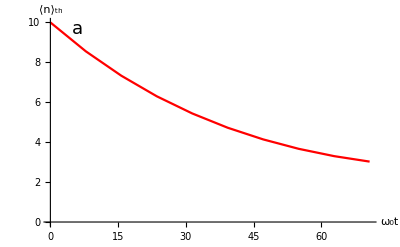

```mathematica
psafa0=ListPlot[tab0,Joined->True,PlotRange->All,PlotStyle->{Red,Joined},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩_th",Black,18]},TicksStyle->Directive[Black],Epilog->{Inset[Style["a",18,Black],Scaled[{0.1,0.95}]]}]
```

## Here we generate the data using corresponding theory prediction, when phase errors are accounted for.

```mathematica
D2[t_] = d2 Cos[ωd t + ϕd] /.ωd-> 2;P11[t_] = Exp[- d2 t]((Exp[ 2 d2 t]- 1)(Sin[t + ϕd] - d2 Sin[t]) + d2( Exp[2 d2 t ] + 1) Cos[t + ϕd]- (Exp[2 d2 t] + 1)Cos[t])/(2 (d2 Cos[ϕd]  - 1));
IP22[t_] = Exp[- d2 t]( (Exp[2 d2 t] - 1)Cos[t + ϕd]- (Exp[2d2 t] + 1)Sin[t])/(2 (d2 Cos[ϕd]- 1));α[t_] =(P11[t]- I IP22[t] + I D[P11[tp]- I IP22[tp],tp] /.tp-> t)/2;
β[t_] = (P11[t]+ I IP22[t] + I D[P11[tp]+ I IP22[tp],tp] /.tp-> t)/2;b[t_] = α[t] μ + β[t]Conjugate[μ];
bdb[t_] = (Abs[α[t]]^2 + Abs[β[t]]^2)Abs[μ]^2   + Conjugate[α[t]] β[t]Conjugate[μ]^2 + α[t]Conjugate[β[t]]μ^2 + Abs[β[t]]^2;
b2[t_] = α[t]^2 μ^2 + α[t]β[t](2 Abs[μ]^2 + 1) + β[t]^2 Conjugate[μ]^2;myd2 = 0.01 w0;
myϕd = π/2;
myμ = Sqrt[10];
params = {d2-> myd2,ϕd-> myϕd ,μ->myμ };data0 = Table[{t,(bdb[t]/.params)},{t,0,dt IntegerPart[45Pi/(wd dt)],0.1}];
```

## Here we save the data from simulating theory predictions, for different degree of phase errors. They are then compared to corresponding numerical results.

```mathematica
data0={{0.,10.+0. ⅈ},{0.1,9.999838290980627+0. ⅈ},{0.2,9.998831019449241+0. ⅈ},{0.30000000000000004,9.99622846473359+0. ⅈ},{0.4,9.991349039556502+0. ⅈ},{0.5,9.983606135025017+0. ⅈ},{0.6000000000000001,9.972531079373255+0. ⅈ},{0.7000000000000001,9.957791312469553+0. ⅈ},{0.8,9.939203072039742+0. ⅈ},{0.9,9.916738108737983+0. ⅈ},{1.,9.890524186705552+0. ⅈ},{1.1,9.860839374494379+0. ⅈ},{1.2000000000000002,9.828100378283388+0. ⅈ},{1.3,9.79284540535786+0. ⅈ},{1.4000000000000001,9.755712261507096+0. ⅈ},{1.5,9.717412572823367+0. ⅈ},{1.6,9.678703173037244+0. ⅈ},{1.7000000000000002,9.640355806150973+0. ⅈ},{1.8,9.60312635657882+0. ⅈ},{1.9000000000000001,9.567724832969905+0. ⅈ},{2.,9.534787297013496+0. ⅈ},{2.1,9.50485084639081+0. ⅈ},{2.2,9.478332635097756+0. ⅈ},{2.3000000000000003,9.455513749805139+0. ⅈ},{2.4000000000000004,9.43652856444779+0. ⅈ},{2.5,9.421359974786247+0. ⅈ},{2.6,9.40984067913085+0. ⅈ},{2.7,9.401660430190542+0. ⅈ},{2.8000000000000003,9.396378945727148+0. ⅈ},{2.9000000000000004,9.393443941786657+0. ⅈ},{3.,9.392213550596066+0. ⅈ},{3.1,9.391982213695057+0. ⅈ},{3.2,9.392009006218705+0. ⅈ},{3.3000000000000003,9.391547255673+0. ⅈ},{3.4000000000000004,9.389874271562991+0. ⅈ},{3.5,9.386320002533589+0. ⅈ},{3.6,9.380293485063563+0. ⅈ},{3.7,9.371306040142715+0. ⅈ},{3.8000000000000003,9.358990307905305+0. ⅈ},{3.9000000000000004,9.343114379411748+0. ⅈ},{4.,9.323590482792127+0. ⅈ},{4.1000000000000005,9.300477899794506+0. ⅈ},{4.2,9.273980019629816+0. ⅈ},{4.3,9.244435670640753+0. ⅈ},{4.4,9.21230509743705+0. ⅈ},{4.5,9.178151162724516+0. ⅈ},{4.6000000000000005,9.142616540752886+0. ⅈ},{4.7,9.106397825745368+0. ⅈ},{4.800000000000001,9.070217597750547+0. ⅈ},{4.9,9.034795565486087+0. ⅈ},{5.,9.000819938020973+0. ⅈ},{5.1000000000000005,8.968920163463675+0. ⅈ},{5.2,8.939642113912907+0. ⅈ},{5.300000000000001,8.913426694311589+0. ⅈ},{5.4,8.890592712732582+0. ⅈ},{5.5,8.871324676747644+0. ⅈ},{5.6000000000000005,8.85566598189433+0. ⅈ},{5.7,8.843517741866341+0. ⅈ},{5.800000000000001,8.834643284590532+0. ⅈ},{5.9,8.82867811282441+0. ⅈ},{6.,8.825144911285719+0. ⅈ},{6.1000000000000005,8.823472983192827+0. ⅈ},{6.2,8.82302132530594+0. ⅈ},{6.300000000000001,8.82310440892709+0. ⅈ},{6.4,8.82301963035016+0. ⅈ},{6.5,8.822075331937315+0. ⅈ},{6.6000000000000005,8.819618276649457+0. ⅈ},{6.7,8.81505948503148+0. ⅈ},{6.800000000000001,8.807897413130119+0. ⅈ},{6.9,8.797737559667674+0. ⅈ},{7.,8.784307736477631+0. ⅈ},{7.1000000000000005,8.767468411791022+0. ⅈ},{7.2,8.747217734340047+0. ⅈ},{7.300000000000001,8.723691059435664+0. ⅈ},{7.4,8.697155017637318+0. ⅈ},{7.5,8.667996383609411+0. ⅈ},{7.6000000000000005,8.636706208628162+0. ⅈ},{7.7,8.603859866816084+0. ⅈ},{7.800000000000001,8.570093825192643+0. ⅈ},{7.9,8.536080074776144+0. ⅈ},{8.,8.502499249326124+0. ⅈ},{8.1,8.470013506471187+0. ⅈ},{8.200000000000001,8.43924025117176+0. ⅈ},{8.3,8.410727743683186+0. ⅈ},{8.4,8.384933555085581+0. ⅈ},{8.5,8.362206716342985+0. ⅈ},{8.6,8.342774256555236+0. ⅈ},{8.700000000000001,8.32673264868246+0. ⅈ},{8.8,8.314044483718817+0. ⅈ},{8.9,8.304540484997746+0. ⅈ},{9.,8.297926761399633+0. ⅈ},{9.1,8.293796990190117+0. ⅈ},{9.200000000000001,8.291649025300842+0. ⅈ},{9.3,8.290905252777737+0. ⅈ},{9.4,8.290935868708555+0. ⅈ},{9.5,8.291084141917674+0. ⅈ},{9.600000000000001,8.290692648446921+0. ⅈ},{9.700000000000001,8.289129430171926+0. ⅈ},{9.8,8.285813037053787+0. ⅈ},{9.9,8.280235461045592+0. ⅈ},{10.,8.27198205746977+0. ⅈ},{10.100000000000001,8.260747673106513+0. ⅈ},{10.200000000000001,8.24634835423528+0. ⅈ},{10.3,8.228728186202668+0. ⅈ},{10.4,8.207961011559881+0. ⅈ},{10.5,8.184246978576871+0. ⅈ},{10.600000000000001,8.157904077815221+0. ⅈ},{10.700000000000001,8.129355023232062+0. ⅈ},{10.8,8.099110018112086+0. ⅈ},{10.9,8.067746107729226+0. ⅈ},{11.,8.035883953681418+0. ⅈ},{11.100000000000001,8.004162964141447+0. ⅈ},{11.200000000000001,7.9732157760042615+0. ⅈ},{11.3,7.9436431067806685+0. ⅈ},{11.4,7.915989975372722+0. ⅈ},{11.5,7.890724232474288+0. ⅈ},{11.600000000000001,7.8682182457488175+0. ⅈ},{11.700000000000001,7.848734456095055+0. ⅈ},{11.8,7.8324153644775+0. ⅈ},{11.9,7.819278330321318+0. ⅈ},{12.,7.809215369536578+0. ⅈ},{12.100000000000001,7.801997940578084+0. ⅈ},{12.200000000000001,7.797286508533228+0. ⅈ},{12.3,7.794644487951548+0. ⅈ},{12.4,7.793555992479874+0. ⅈ},{12.5,7.793446670150091+0. ⅈ},{12.600000000000001,7.793706783227318+0. ⅈ},{12.700000000000001,7.793715605521257+0. ⅈ},{12.8,7.79286616128205+0. ⅈ},{12.9,7.790589320037318+0. ⅈ},{13.,7.786376291216902+0. ⅈ},{13.100000000000001,7.779798629826273+0. ⅈ},{13.200000000000001,7.77052496694049+0. ⅈ},{13.3,7.758333812179503+0. ⅈ},{13.4,7.743121934166805+0. ⅈ},{13.5,7.724908002845651+0. ⅈ},{13.600000000000001,7.703831367280689+0. ⅈ},{13.700000000000001,7.6801460366109+0. ⅈ},{13.8,7.654210122406111+0. ⅈ},{13.9,7.626471180244814+0. ⅈ},{14.,7.597448049775021+0. ⅈ},{14.100000000000001,7.567709929489713+0. ⅈ},{14.200000000000001,7.537853529591248+0. ⅈ},{14.3,7.508479219488274+0. ⅈ},{14.4,7.480167122886293+0. ⅈ},{14.5,7.453454111794156+0. ⅈ},{14.600000000000001,7.428812611286917+0. ⅈ},{14.700000000000001,7.40663205125988+0. ⅈ},{14.8,7.387203692827862+0. ⅈ},{14.9,7.370709419917125+0. ⅈ},{15.,7.35721492653051+0. ⅈ},{15.100000000000001,7.346667553597541+0. ⅈ},{15.200000000000001,7.338898843339475+0. ⅈ},{15.3,7.333631691120754+0. ⅈ},{15.4,7.3304917923081865+0. ⅈ},{15.5,7.329022911955261+0. ⅈ},{15.600000000000001,7.328705354872918+0. ⅈ},{15.700000000000001,7.328976888741453+0. ⅈ},{15.8,7.3292552782326545+0. ⅈ},{15.9,7.328961527294635+0. ⅈ},{16.,7.327542902093026+0. ⅈ},{16.1,7.324494819440091+0. ⅈ},{16.2,7.319380734244029+0. ⅈ},{16.3,7.311849242494665+0. ⅈ},{16.400000000000002,7.3016477301336+0. ⅈ},{16.5,7.2886320381884495+0. ⅈ},{16.6,7.272771775108758+0. ⅈ},{16.7,7.254151081857874+0. ⅈ},{16.8,7.232964836988916+0. ⅈ},{16.900000000000002,7.209510470408815+0. ⅈ},{17.,7.1841757285928525+0. ⅈ},{17.1,7.157422893757555+0. ⅈ},{17.2,7.129770098632228+0. ⅈ},{17.3,7.1017704915337605+0. ⅈ},{17.400000000000002,7.073990089048377+0. ⅈ},{17.5,7.046985202590788+0. ⅈ},{17.6,7.021280338626582+0. ⅈ},{17.7,6.9973474500094675+0. ⅈ},{17.8,6.975587358727231+0. ⅈ},{17.900000000000002,6.9563140807789345+0. ⅈ},{18.,6.939742665609751+0. ⅈ},{18.1,6.925981020326908+0. ⅈ},{18.2,6.915026028560179+0. ⅈ},{18.3,6.90676410176364+0. ⅈ},{18.400000000000002,6.9009761238728125+0. ⅈ},{18.5,6.897346575588126+0. ⅈ},{18.6,6.895476459092313+0. ⅈ},{18.7,6.894899494271419+0. ⅈ},{18.8,6.895100929394655+0. ⅈ},{18.900000000000002,6.895538207729219+0. ⅈ},{19.,6.895662660657528+0. ⅈ},{19.1,6.89494136022823+0. ⅈ},{19.200000000000003,6.892878261078061+0. ⅈ},{19.3,6.889033793294255+0. ⅈ},{19.400000000000002,6.883042132654124+0. ⅈ},{19.5,6.8746254700712255+0. ⅈ},{19.6,6.863604724082931+0. ⅈ},{19.700000000000003,6.849906283875765+0. ⅈ},{19.8,6.83356452986348+0. ⅈ},{19.900000000000002,6.814720047801282+0. ⅈ},{20.,6.793613624079642+0. ⅈ},{20.1,6.7705762773520055+0. ⅈ},{20.200000000000003,6.746015738365642+0. ⅈ},{20.3,6.7203999295899175+0. ⅈ},{20.400000000000002,6.694238113478306+0. ⅈ},{20.5,6.6680604683821105+0. ⅈ},{20.6,6.64239691077098+0. ⅈ},{20.700000000000003,6.617756009253584+0. ⅈ},{20.8,6.594604828989344+0. ⅈ},{20.900000000000002,6.573350504842898+0. ⅈ},{21.,6.554324269787285+0. ⅈ},{21.1,6.537768564587713+0. ⅈ},{21.200000000000003,6.523827729804067+0. ⅈ},{21.3,6.512542636702609+0. ⅈ},{21.400000000000002,6.503849455587641+0. ⅈ},{21.5,6.497582594693201+0. ⅈ},{21.6,6.493481676720068+0. ⅈ},{21.700000000000003,6.491202259973381+0. ⅈ},{21.8,6.490329863198527+0. ⅈ},{21.900000000000002,6.490396723463175+0. ⅈ},{22.,6.490900609883245+0. ⅈ},{22.1,6.491324936790704+0. ⅈ},{22.200000000000003,6.491159371137479+0. ⅈ},{22.3,6.489920112346497+0. ⅈ},{22.400000000000002,6.487169038996296+0. ⅈ},{22.5,6.4825309648886815+0. ⅈ},{22.6,6.475708325162914+0. ⅈ},{22.700000000000003,6.4664927179616125+0. ⅈ},{22.8,6.454772854450644+0. ⅈ},{22.900000000000002,6.440538614596862+0. ⅈ},{23.,6.4238810621961235+0. ⅈ},{23.1,6.404988433964582+0. ⅈ},{23.200000000000003,6.384138277622602+0. ⅈ},{23.3,6.361686066446372+0. ⅈ},{23.400000000000002,6.338050756698137+0. ⅈ},{23.5,6.313697874196891+0. ⅈ},{23.6,6.289120812361718+0. ⅈ},{23.700000000000003,6.264821092618201+0. ⅈ},{23.8,6.241288376483264+0. ⅈ},{23.900000000000002,6.21898102551957+0. ⅈ},{24.,6.198307980525614+0. ⅈ},{24.1,6.179612675908814+0. ⅈ},{24.200000000000003,6.1631596214982745+0. ⅈ},{24.3,6.14912417552778+0. ⅈ},{24.400000000000002,6.1375859035698035+0. ⅈ},{24.5,6.1285257740362695+0. ⅈ},{24.6,6.121827287272717+0. ⅈ},{24.700000000000003,6.11728147840756+0. ⅈ},{24.8,6.114595580227979+0. ⅈ},{24.900000000000002,6.113404987550831+0. ⅈ},{25.,6.113288034566311+0. ⅈ},{25.1,6.113782986569185+0. ⅈ},{25.200000000000003,6.114406561659982+0. ⅈ},{25.3,6.114673239719913+0. ⅈ},{25.400000000000002,6.114114587451787+0. ⅈ},{25.5,6.112297830556943+0. ⅈ},{25.6,6.108842936977733+0. ⅈ},{25.700000000000003,6.103437537153686+0. ⅈ},{25.8,6.095849095839503+0. ⅈ},{25.900000000000002,6.085933861589188+0. ⅈ},{26.,6.073642249999129+0. ⅈ},{26.1,6.059020459981361+0. ⅈ},{26.200000000000003,6.042208272963062+0. ⅈ},{26.3,6.023433136957314+0. ⅈ},{26.400000000000002,6.003000784870747+0. ⅈ},{26.5,5.981282773357625+0. ⅈ},{26.6,5.958701449589943+0. ⅈ},{26.700000000000003,5.935712953731928+0. ⅈ},{26.8,5.9127889407691105+0. ⅈ},{26.900000000000002,5.890397753720486+0. ⅈ},{27.,5.868985799336938+0. ⅈ},{27.1,5.848959866510421+0. ⅈ},{27.200000000000003,5.830671087333399+0. ⅈ},{27.3,5.814401172767713+0. ⅈ},{27.400000000000002,5.80035146201714+0. ⅈ},{27.5,5.788635210734034+0. ⅈ},{27.6,5.779273412741979+0. ⅈ},{27.700000000000003,5.772194308273471+0. ⅈ},{27.8,5.767236584483638+0. ⅈ},{27.900000000000002,5.764156127085095+0. ⅈ},{28.,5.762636041199104+0. ⅈ},{28.1,5.762299530510145+0. ⅈ},{28.200000000000003,5.762725111632632+0. ⅈ},{28.3,5.763463549649817+0. ⅈ},{28.400000000000002,5.764055834603958+0. ⅈ},{28.5,5.764051479844328+0. ⅈ},{28.6,5.7630264130192845+0. ⅈ},{28.700000000000003,5.7605997494259835+0. ⅈ},{28.8,5.756448784544804+0. ⅈ},{28.900000000000002,5.750321615905799+0. ⅈ},{29.,5.742046900947031+0. ⅈ},{29.1,5.731540373303542+0. ⅈ},{29.200000000000003,5.71880787033362+0. ⅈ},{29.3,5.703944764405228+0. ⅈ},{29.400000000000002,5.68713183393755+0. ⅈ},{29.5,5.668627751698716+0. ⅈ},{29.6,5.64875850177985+0. ⅈ},{29.700000000000003,5.627904157697387+0. ⅈ},{29.8,5.60648355745474+0. ⅈ},{29.900000000000002,5.5849374930726405+0. ⅈ},{30.,5.5637110889075405+0. ⅈ},{30.1,5.54323607285037+0. ⅈ},{30.200000000000003,5.523913646151285+0. ⅈ},{30.3,5.506098631186514+0. ⅈ},{30.400000000000002,5.490085523128004+0. ⅈ},{30.5,5.47609699341673+0. ⅈ},{30.6,5.464275293372822+0. ⅈ},{30.700000000000003,5.45467688924126+0. ⅈ},{30.8,5.44727053018985+0. ⅈ},{30.900000000000002,5.4419388134577815+0. ⅈ},{31.,5.438483171486912+0. ⅈ},{31.1,5.43663207000747+0. ⅈ},{31.200000000000003,5.436052079084602+0. ⅈ},{31.3,5.436361366081766+0. ⅈ},{31.400000000000002,5.43714506480596+0. ⅈ},{31.5,5.437971902467686+0. ⅈ},{31.6,5.438411418323302+0. ⅈ},{31.700000000000003,5.438051086777933+0. ⅈ},{31.8,5.436512664053067+0. ⅈ},{31.900000000000002,5.433467110913458+0. ⅈ},{32.,5.428647502973548+0. ⅈ},{32.1,5.421859422323563+0. ⅈ},{32.2,5.412988426272837+0. ⅈ},{32.300000000000004,5.402004306770972+0. ⅈ},{32.4,5.388961982793505+0. ⅈ},{32.5,5.37399900250718+0. ⅈ},{32.6,5.357329766988287+0. ⅈ},{32.7,5.339236717285292+0. ⅈ},{32.800000000000004,5.3200588465405545+0. ⅈ},{32.9,5.3001780039820225+0. ⅈ},{33.,5.280003543737044+0. ⅈ},{33.1,5.259955935251173+0. ⅈ},{33.2,5.240449991155662+0. ⅈ},{33.300000000000004,5.221878381256005+0. ⅈ},{33.4,5.204596087495741+0. ⅈ},{33.5,5.188906414930639+0. ⅈ},{33.6,5.175049109608602+0. ⅈ},{33.7,5.163191048428464+0. ⅈ},{33.800000000000004,5.153419862040437+0. ⅈ},{33.9,5.1457407338551455+0. ⅈ},{34.,5.140076490991387+0. ⅈ},{34.1,5.1362709716107+0. ⅈ},{34.2,5.134095522799459+0. ⅈ},{34.300000000000004,5.133258359146316+0. ⅈ},{34.4,5.133416399334084+0. ⅈ},{34.5,5.134189100868005+0. ⅈ},{34.6,5.1351737353072195+0. ⅈ},{34.7,5.135961491074765+0. ⅈ},{34.800000000000004,5.136153760212519+0. ⅈ},{34.9,5.135377960453301+0. ⅈ},{35.,5.1333022648086395+0. ⅈ},{35.1,5.12964865659626+0. ⅈ},{35.2,5.124203796546695+0. ⅈ},{35.300000000000004,5.116827277517872+0. ⅈ},{35.4,5.1074569478014+0. ⅈ},{35.5,5.096111101769679+0. ⅈ},{35.6,5.082887461961093+0. ⅈ},{35.7,5.067959004616845+0. ⅈ},{35.800000000000004,5.051566806071037+0. ⅈ},{35.9,5.034010205276413+0. ⅈ},{36.,5.015634683459531+0. ⅈ},{36.1,4.996817951280081+0. ⅈ},{36.2,4.977954803423071+0. ⅈ},{36.300000000000004,4.959441347582685+0. ⅈ},{36.4,4.941659237515345+0. ⅈ},{36.5,4.924960537426755+0. ⅈ},{36.6,4.909653817602809+0. ⅈ},{36.7,4.89599203007182+0. ⅈ},{36.800000000000004,4.884162640315386+0. ⅈ},{36.9,4.874280399598982+0. ⅈ},{37.,4.866383036074627+0. ⅈ},{37.1,4.860430025704048+0. ⅈ},{37.2,4.8563044809565525+0. ⅈ},{37.300000000000004,4.8538180710704655+0. ⅈ},{37.4,4.852718767371485+0. ⅈ},{37.5,4.852701095488648+0. ⅈ},{37.6,4.853418477707775+0. ⅈ},{37.7,4.8544971670297485+0. ⅈ},{37.800000000000004,4.855551212945544+0. ⅈ},{37.9,4.856197859877735+0. ⅈ},{38.,4.856072764144674+0. ⅈ},{38.1,4.854844424693022+0. ⅈ},{38.2,4.852227256257278+0. ⅈ},{38.300000000000004,4.847992789627476+0. ⅈ},{38.400000000000006,4.8419785600298315+0. ⅈ},{38.5,4.834094338141998+0. ⅈ},{38.6,4.824325465195544+0. ⅈ},{38.7,4.812733169660616+0. ⅈ},{38.800000000000004,4.799451863516056+0. ⅈ},{38.900000000000006,4.784683536271395+0. ⅈ},{39.,4.768689479948039+0. ⅈ},{39.1,4.751779683587129+0. ⅈ},{39.2,4.734300327374289+0. ⅈ},{39.300000000000004,4.716619880564991+0. ⅈ},{39.400000000000006,4.699114361172558+0. ⅈ},{39.5,4.6821523467758634+0. ⅈ},{39.6,4.666080333645073+0. ⅈ},{39.7,4.651209025442759+0. ⅈ},{39.800000000000004,4.637801093749422+0. ⅈ},{39.900000000000006,4.626060892222149+0. ⅈ},{40.,4.616126526798601+0. ⅈ},{40.1,4.608064589232015+0. ⅈ},{40.2,4.601867754224113+0. ⅈ},{40.300000000000004,4.597455325809763+0. ⅈ},{40.400000000000006,4.594676701025778+0. ⅈ},{40.5,4.593317602954313+0. ⅈ},{40.6,4.593108825575941+0. ⅈ},{40.7,4.59373713383699+0. ⅈ},{40.800000000000004,4.5948578778338085+0. ⅈ},{40.900000000000006,4.596108813352291+0. ⅈ},{41.,4.597124574765907+0. ⅈ},{41.1,4.597551222256225+0. ⅈ},{41.2,4.597060284357214+0. ⅈ},{41.300000000000004,4.595361738896582+0. ⅈ},{41.400000000000006,4.592215419556222+0. ⅈ},{41.5,4.587440399668466+0. ⅈ},{41.6,4.580921986872838+0. ⅈ},{41.7,4.572616058558188+0. ⅈ},{41.800000000000004,4.562550574727167+0. ⅈ},{41.900000000000006,4.5508242177639175+0. ⅈ},{42.,4.537602223052625+0. ⅈ},{42.1,4.523109575925135+0. ⅈ},{42.2,4.507621854584704+0. ⅈ},{42.300000000000004,4.491454091341756+0. ⅈ},{42.400000000000006,4.474948102059022+0. ⅈ},{42.5,4.458458793104418+0. ⅈ},{42.6,4.442339994049657+0. ⅈ},{42.7,4.426930381352278+0. ⅈ},{42.800000000000004,4.4125400527166665+0. ⅈ},{42.900000000000006,4.399438284043622+0. ⅈ},{43.,4.387842952027977+0. ⅈ},{43.1,4.377912037565615+0. ⅈ},{43.2,4.369737540948792+0. ⅈ},{43.300000000000004,4.363342042766584+0. ⅈ},{43.400000000000006,4.358678038389439+0. ⅈ},{43.5,4.355630063150658+0. ⅈ},{43.6,4.354019514265731+0. ⅈ},{43.7,4.353611968570679+0. ⅈ},{43.800000000000004,4.354126696553566+0. ⅈ},{43.900000000000006,4.355247986793346+0. ⅈ},{44.,4.356637824199636+0. ⅈ},{44.1,4.3579494131274625+0. ⅈ},{44.2,4.358841004540103+0. ⅈ},{44.300000000000004,4.358989476111942+0. ⅈ},{44.400000000000006,4.358103125837946+0. ⅈ},{44.5,4.355933172808335+0. ⅈ},{44.6,4.352283511929139+0. ⅈ},{44.7,4.347018340341025+0. ⅈ},{44.800000000000004,4.3400673592281365+0. ⅈ},{44.900000000000006,4.3314283521466965+0. ⅈ},{45.,4.321167046027291+0. ⅈ},{45.1,4.309414269411354+0. ⅈ},{45.2,4.296360529949375+0. ⅈ},{45.300000000000004,4.282248235444095+0. ⅈ},{45.400000000000006,4.2673618757169525+0. ⅈ},{45.5,4.252016562642753+0. ⅈ},{45.6,4.236545389693195+0. ⅈ},{45.7,4.221286117764381+0. ⅈ},{45.800000000000004,4.206567719189126+0. ⅈ},{45.900000000000006,4.192697315721331+0. ⅈ},{46.,4.179948028841467+0. ⅈ},{46.1,4.168548222733756+0. ⅈ},{46.2,4.158672563305876+0. ⅈ},{46.300000000000004,4.1504352429898645+0. ⅈ},{46.400000000000006,4.143885633761368+0. ⅈ},{46.5,4.139006533361165+0. ⅈ},{46.6,4.135715066006295+0. ⅈ},{46.7,4.133866193084236+0. ⅈ},{46.800000000000004,4.133258685645439+0. ⅈ},{46.900000000000006,4.133643313064862+0. ⅈ},{47.,4.134732914886479+0. ⅈ},{47.1,4.1362139490379555+0. ⅈ},{47.2,4.137759052197138+0. ⅈ},{47.300000000000004,4.139040109338286+0. ⅈ},{47.400000000000006,4.139741310864014+0. ⅈ},{47.5,4.139571677913695+0. ⅈ},{47.6,4.138276559277138+0. ⅈ},{47.7,4.135647645856995+0. ⅈ},{47.800000000000004,4.1315311090613225+0. ⅈ},{47.900000000000006,4.125833545406131+0. ⅈ},{48.,4.11852549789881+0. ⅈ},{48.1,4.1096424219053045+0. ⅈ},{48.2,4.099283065284833+0. ⅈ},{48.300000000000004,4.087605335530965+0. ⅈ},{48.400000000000006,4.074819826388049+0. ⅈ},{48.5,4.06118126896313+0. ⅈ},{48.6,4.046978254065824+0. ⅈ},{48.7,4.032521640168671+0. ⅈ},{48.800000000000004,4.018132112341789+0. ⅈ},{48.900000000000006,4.004127389804163+0. ⅈ},{49.,3.9908095921266966+0. ⅈ},{49.1,3.9784532661881418+0. ⅈ},{49.2,3.9672945481056274+0. ⅈ},{49.300000000000004,3.9575218877089124+0. ⅈ},{49.400000000000006,3.949268699616054+0. ⅈ},{49.5,3.9426082271784573+0. ⅈ},{49.6,3.9375508166329993+0. ⅈ},{49.7,3.9340437023016186+0. ⅈ},{49.800000000000004,3.9319733034748054+0. ⅈ},{49.900000000000006,3.931169933702428+0. ⅈ},{50.,3.931414727565901+0. ⅈ},{50.1,3.932448502410196+0. ⅈ},{50.2,3.9339821964309216+0. ⅈ},{50.300000000000004,3.9357084629308563+0. ⅈ},{50.400000000000006,3.9373139558844326+0. ⅈ},{50.5,3.938491815902946+0. ⅈ},{50.6,3.9389538592535747+0. ⅈ},{50.7,3.938441985947822+0. ⅈ},{50.800000000000004,3.936738355485769+0. ⅈ},{50.900000000000006,3.933673929266286+0. ⅈ},{51.,3.929135044889394+0. ⅈ},{51.1,3.9230677669029106+0. ⅈ},{51.2,3.915479847785102+0. ⅈ},{51.300000000000004,3.9064402285295774+0. ⅈ},{51.400000000000006,3.8960761062866904+0. ⅈ},{51.5,3.8845676932088296+0. ⅈ},{51.6,3.872140882104068+0. ⅈ},{51.7,3.859058117102945+0. ⅈ},{51.800000000000004,3.845607838028201+0. ⅈ},{51.900000000000006,3.832092922761925+0. ⅈ},{52.,3.8188185904632856+0. ⅈ},{52.1,3.8060802485205336+0. ⅈ},{52.2,3.7941517668849727+0. ⅈ},{52.300000000000004,3.7832746449593913+0. ⅈ},{52.400000000000006,3.7736484992933974+0. ⅈ},{52.5,3.7654232464969937+0. ⅈ},{52.6,3.7586932872153227+0. ⅈ},{52.7,3.753493916482217+0. ⅈ},{52.800000000000004,3.74980009652794+0. ⅈ},{52.900000000000006,3.747527633732176+0. ⅈ},{53.,3.7465367056557355+0. ⅈ},{53.1,3.7466375907669676+0. ⅈ},{53.2,3.7475983663040555+0. ⅈ},{53.300000000000004,3.749154262131249+0. ⅈ},{53.400000000000006,3.7510182935119936+0. ⅈ},{53.5,3.752892745979249+0. ⅈ},{53.6,3.75448105286525+0. ⅈ},{53.7,3.7554995918059717+0. ⅈ},{53.800000000000004,3.755688931171143+0. ⅈ},{53.900000000000006,3.754824080647225+0. ⅈ},{54.,3.752723341138463+0. ⅈ},{54.1,3.7492554060680057+0. ⅈ},{54.2,3.7443444367468697+0. ⅈ},{54.300000000000004,3.737972915885587+0. ⅈ},{54.400000000000006,3.730182172281541+0. ⅈ},{54.5,3.7210705626654246+0. ⅈ},{54.6,3.710789389923269+0. ⅈ},{54.7,3.699536726718895+0. ⅈ},{54.800000000000004,3.687549396363007+0. ⅈ},{54.900000000000006,3.675093435337354+0. ⅈ},{55.,3.6624534213286104+0. ⅈ},{55.1,3.649921094633042+0. ⅈ},{55.2,3.6377837276530904+0. ⅈ},{55.300000000000004,3.6263127059035867+0. ⅈ},{55.400000000000006,3.61575277418555+0. ⅈ},{55.5,3.606312373810784+0. ⅈ},{55.6,3.5981554521282924+0. ⅈ},{55.7,3.5913950659370695+0. ⅈ},{55.800000000000004,3.5860890280859294+0. ⅈ},{55.900000000000006,3.5822377645707952+0. ⅈ},{56.,3.579784461031089+0. ⅈ},{56.1,3.578617486254821+0. ⅈ},{56.2,3.578574989764789+0. ⅈ},{56.300000000000004,3.579451484374072+0. ⅈ},{56.400000000000006,3.581006146183146+0. ⅈ},{56.5,3.5829724969391297+0. ⅈ},{56.6,3.5850690796450024+0. ⅈ},{56.7,3.5870106999040434+0. ⅈ},{56.800000000000004,3.5885197841937835+0. ⅈ},{56.900000000000006,3.589337402883709+0. ⅈ},{57.,3.589233520423816+0. ⅈ},{57.1,3.5880160671068992+0. ⅈ},{57.2,3.5855384748231725+0. ⅈ},{57.300000000000004,3.5817053813288116+0. ⅈ},{57.400000000000006,3.5764762812296773+0. ⅈ},{57.5,3.569866984175736+0. ⅈ},{57.6,3.5619488283739873+0. ⅈ},{57.7,3.552845686958783+0. ⅈ},{57.800000000000004,3.5427288924467533+0. ⅈ},{57.900000000000006,3.5318102869678913+0. ⅈ},{58.,3.5203336799382754+0. ⅈ},{58.1,3.508565057407127+0. ⅈ},{58.2,3.496781936013928+0. ⅈ},{58.300000000000004,3.48526228743202+0. ⅈ},{58.400000000000006,3.474273475087326+0. ⅈ},{58.5,3.464061643239109+0. ⅈ},{58.6,3.4548419793086644+0. ⅈ},{58.7,3.446790234455971+0. ⅈ},{58.800000000000004,3.440035836303032+0. ⅈ},{58.900000000000006,3.434656863462674+0. ⅈ},{59.,3.4306770767413006+0. ⅈ},{59.1,3.428065119547547+0. ⅈ},{59.2,3.4267359134502513+0. ⅈ},{59.300000000000004,3.4265541874432017+0. ⅈ},{59.400000000000006,3.4273399947685466+0. ⅈ},{59.5,3.4288759924859953+0. ⅈ},{59.6,3.4309161894629288+0. ⅈ},{59.7,3.433195810841692+0. ⅈ},{59.800000000000004,3.4354418835720857+0. ⅈ},{59.900000000000006,3.43738411997224+0. ⅈ},{60.,3.4387656655535643+0. ⅈ},{60.1,3.439353283898697+0. ⅈ},{60.2,3.4389465749068258+0. ⅈ},{60.300000000000004,3.43738586223955+0. ⅈ},{60.400000000000006,3.434558439696973+0. ⅈ},{60.5,3.430402932348313+0. ⅈ},{60.6,3.4249116038718093+0. ⅈ},{60.7,3.418130523694238+0. ⅈ},{60.800000000000004,3.4101575928757875+0. ⅈ},{60.900000000000006,3.401138512860893+0. ⅈ},{61.,3.3912608628211878+0. ⅈ},{61.1,3.380746526119136+0. ⅈ},{61.2,3.3698427714623467+0. ⅈ},{61.300000000000004,3.358812347038487+0. ⅈ},{61.400000000000006,3.3479229842543425+0. ⅈ},{61.5,3.3374367301638053+0. ⅈ},{61.6,3.3275995334048254+0. ⅈ},{61.7,3.318631497291298+0. ⅈ},{61.800000000000004,3.310718186108911+0. ⅈ},{61.900000000000006,3.304003327785061+0. ⅈ},{62.,3.2985831996849857+0. ⅈ},{62.1,3.2945029166082005+0. ⅈ},{62.2,3.2917547638408564+0. ⅈ},{62.300000000000004,3.290278636412957+0. ⅈ},{62.400000000000006,3.289964561777783+0. ⅈ},{62.5,3.2906572003171313+0. ⅈ},{62.6,3.2921621396713068+0. ⅈ},{62.7,3.2942537280015536+0. ⅈ},{62.800000000000004,3.2966841307180914+0. ⅈ},{62.900000000000006,3.2991932473282546+0. ⅈ},{63.,3.3015190917522723+0. ⅈ},{63.1,3.303408222003444+0. ⅈ},{63.2,3.304625804192078+0. ⅈ},{63.300000000000004,3.304964911383582+0. ⅈ},{63.400000000000006,3.3042546892599596+0. ⅈ},{63.5,3.3023670665138205+0. ⅈ},{63.6,3.2992217465787057+0. ⅈ},{63.7,3.2947892863062336+0. ⅈ},{63.800000000000004,3.289092143769132+0. ⅈ},{63.900000000000006,3.282203658436462+0. ⅈ},{64.,3.2742450092997224+0. ⅈ},{64.10000000000001,3.2653802768473597+0. ⅈ},{64.2,3.255809809903525+0. ⅈ},{64.3,3.2457621652888875+0. ⅈ},{64.4,3.2354849443856963+0. ⅈ},{64.5,3.2252348937897963+0. ⅈ},{64.60000000000001,3.215267665627021+0. ⅈ},{64.7,3.205827645705835+0. ⅈ},{64.8,3.197138254009939+0. ⅈ},{64.9,3.189393102287557+0. ⅈ},{65.,3.1827483584926917+0. ⅈ},{65.10000000000001,3.1773166190046283+0. ⅈ},{65.2,3.173162528870918+0. ⅈ},{65.3,3.170300320225426+0. ⅈ},{65.4,3.168693362337457+0. ⅈ},{65.5,3.1682557365142934+0. ⅈ},{65.60000000000001,3.168855768507747+0. ⅈ},{65.7,3.1703213733685516+0. ⅈ},{65.8,3.172446995935342+0. ⅈ},{65.9,3.1750018671758973+0. ⅈ},{66.,3.1777392449015984+0. ⅈ},{66.10000000000001,3.1804062689807466+0. ⅈ},{66.2,3.182754037578981+0. ⅈ},{66.3,3.1845475030602763+0. ⅈ},{66.4,3.185574794266408+0. ⅈ},{66.5,3.1856555956009807+0. ⅈ},{66.60000000000001,3.184648251695304+0. ⅈ},{66.7,3.1824553178713337+0. ⅈ},{66.8,3.1790273390657475+0. ⅈ},{66.9,3.1743647108313304+0. ⅈ},{67.,3.1685175526468967+0. ⅈ},{67.10000000000001,3.161583602985637+0. ⅈ},{67.2,3.153704224258597+0. ⅈ},{67.3,3.14505868073784+0. ⅈ},{67.4,3.13585692089935+0. ⅈ},{67.5,3.1263311546064614+0. ⅈ},{67.60000000000001,3.1167265628553515+0. ⅈ},{67.7,3.107291511571052+0. ⅈ},{67.8,3.098267659860422+0. ⅈ},{67.9,3.0898803564802044+0. ⅈ},{68.,3.082329705962163+0. ⅈ},{68.10000000000001,3.075782658378394+0. ⅈ},{68.2,3.0703664352521756+0. ⅈ},{68.3,3.0661635503027753+0. ⅈ},{68.4,3.0632086197234187+0. ⅈ},{68.5,3.061487085094857+0. ⅈ},{68.60000000000001,3.0609358956980905+0. ⅈ},{68.7,3.061446118951679+0. ⅈ},{68.8,3.0628673710704497+0. ⅈ},{68.9,3.0650138878662716+0. ⅈ},{69.,3.0676719907485825+0. ⅈ},{69.10000000000001,3.070608647996014+0. ⅈ},{69.2,3.073580788427808+0. ⅈ},{69.3,3.076344995384794+0. ⅈ},{69.4,3.0786671945708264+0. ⅈ},{69.5,3.080331950343698+0. ⅈ},{69.60000000000001,3.0811510014097294+0. ⅈ},{69.7,3.0809706978836715+0. ⅈ},{69.8,3.0796780460642488+0. ⅈ},{69.9,3.0772051232517192+0. ⅈ},{70.,3.073531690249361+0. ⅈ},{70.10000000000001,3.0686859012287115+0. ⅈ},{70.2,3.062743086521003+0. ⅈ},{70.3,3.055822660599759+0. ⅈ},{70.4,3.048083281990362+0. ⅈ},{70.5,3.039716461124417+0. ⅈ},{70.60000000000001,3.0309388735059457+0. ⅈ}};
```

```mathematica
data0p1={{0.,9.999999999999153},{0.1,9.999841355766923},{0.2,9.998849620596754},{0.30000000000000004,9.996284102160033},{0.4,9.991471315454987},{0.5,9.983831512636709},{0.6000000000000001,9.972901378504515},{0.7000000000000001,9.958352003739922},{0.8,9.940001439379508},{0.9,9.91782135435561},{1.,9.891937554450903},{1.1,9.862624366208353},{1.2000000000000002,9.830293133425801},{1.3,9.795475307138297},{1.4000000000000001,9.758800823211335},{1.5,9.720972646431266},{1.6,9.682738509045404},{1.7000000000000002,9.644860979284086},{1.8,9.608087057372963},{1.9000000000000001,9.57311851063028},{2.,9.540584125068087},{2.1,9.511014970029564},{2.2,9.484823648196905},{2.3000000000000003,9.462288340909494},{2.4000000000000004,9.443542264750597},{2.5,9.428568937634267},{2.6,9.417203419910983},{2.7,9.409139457625024},{2.8000000000000003,9.403942220508887},{2.9000000000000004,9.401066105904892},{3.,9.399876880319082},{3.1,9.399677260588483},{3.2,9.399734903314915},{3.3000000000000003,9.399311679449301},{3.4000000000000004,9.397693064186798},{3.5,9.39421647233802},{3.6,9.388297415890722},{3.7,9.379452451535105},{3.8000000000000003,9.367318017696872},{3.9000000000000004,9.351664427702115},{4.,9.332404481302248},{4.1000000000000005,9.309596373019652},{4.2,9.283440803952569},{4.3,9.254272434675595},{4.4,9.222546041487718},{4.5,9.188817947582455},{4.6000000000000005,9.153723486475297},{4.7,9.117951409924562},{4.800000000000001,9.082216270580272},{4.9,9.047229886142594},{5.,9.013673024022339},{5.1000000000000005,8.982168432264473},{5.2,8.953256284524537},{5.300000000000001,8.927373006660508},{5.4,8.904834314169953},{5.5,8.885823118919891},{5.6000000000000005,8.870382767303184},{5.7,8.858415858024099},{5.800000000000001,8.849688664744782},{5.9,8.843840965721867},{6.,8.84040086820428},{6.1000000000000005,8.838804018244463},{6.2,8.838416414470327},{6.300000000000001,8.838559904023974},{6.4,8.838539335756131},{6.5,8.837670283827126},{6.6000000000000005,8.835306236413047},{6.7,8.83086416981008},{6.800000000000001,8.823847496683715},{6.9,8.813865485630043},{7.,8.800648393134633},{7.1000000000000005,8.784057722566375},{7.2,8.764091221008357},{7.300000000000001,8.740882435612665},{7.4,8.714694868323399},{7.5,8.685910982577894},{7.6000000000000005,8.655016519435042},{7.7,8.62258076542381},{7.800000000000001,8.589233572975463},{7.9,8.55564006039178},{8.,8.522474007019989},{8.1,8.490391007267666},{8.200000000000001,8.460002452549386},{8.3,8.431851373157851},{8.4,8.406391094039044},{8.5,8.383967542785049},{8.6,8.364805899588633},{8.700000000000001,8.349002103469136},{8.8,8.3365195338637},{8.9,8.32719097952513},{9.,8.320725795865851},{9.1,8.316721945836997},{9.200000000000001,8.314682426313045},{9.3,8.31403540939715},{9.4,8.314157282857773},{9.5,8.314397661721713},{9.600000000000001,8.314105368220405},{9.700000000000001,8.312654342644594},{9.8,8.309468454432198},{9.9,8.304044230562987},{10.,8.295970605005994},{10.100000000000001,8.284944914958949},{10.200000000000001,8.27078452194608},{10.3,8.253433612321617},{10.4,8.232964925247158},{10.5,8.209576359006697},{10.600000000000001,8.183582610488418},{10.700000000000001,8.155402199679665},{10.8,8.125540413277774},{10.9,8.094568861821337},{11.,8.063102476801767},{11.100000000000001,8.03177487287814},{11.200000000000001,8.001213061793361},{11.3,7.972012526575128},{11.4,7.944713646377659},{11.5,7.919780404761381},{11.600000000000001,7.897582219758522},{11.700000000000001,7.878379606633624},{11.8,7.86231422901613},{11.9,7.849403717341035},{12.,7.839541442397376},{12.100000000000001,7.832501233912815},{12.200000000000001,7.827946837394174},{12.3,7.8254457147199314},{12.4,7.824486622675163},{12.5,7.8245002554846135},{12.600000000000001,7.8248821182393495},{12.700000000000001,7.825016712556579},{12.8,7.8243020671346795},{12.9,7.822173635861313},{13.,7.818126615051067},{13.100000000000001,7.811735797929657},{13.200000000000001,7.802672185853661},{13.3,7.790715707789525},{13.4,7.775763556903957},{13.5,7.757833829382758},{13.600000000000001,7.737064338711155},{13.700000000000001,7.713706671087062},{13.8,7.6881157367256545},{13.9,7.660735250040613},{14.,7.632079732004217},{14.100000000000001,7.602713764086436},{14.200000000000001,7.573229329730818},{14.3,7.544222152214658},{14.4,7.516267974194006},{14.5,7.489899722937624},{14.600000000000001,7.46558646640559},{14.700000000000001,7.443714990616339},{14.8,7.424574721280357},{14.9,7.408346576859959},{15.,7.395096181554804},{15.100000000000001,7.384771691610859},{15.200000000000001,7.37720630383583},{15.3,7.37212532865355},{15.4,7.369157528872105},{15.5,7.3678502567631785},{15.600000000000001,7.367687772711105},{15.700000000000001,7.3681120044574975},{15.8,7.368544911688268},{15.9,7.368411560020051},{16.,7.3671629836298775},{16.1,7.364297927685341},{16.2,7.359382609758702},{16.3,7.352067721499772},{16.400000000000002,7.342102004602339},{16.5,7.329341873926247},{16.6,7.313756719908284},{16.7,7.295429695696722},{16.8,7.274553974828477},{16.900000000000002,7.251424645531053},{17.,7.226426580702964},{17.1,7.200018781452142},{17.2,7.172715830487373},{17.3,7.145067204233634},{17.400000000000002,7.117635274897395},{17.5,7.090972882681579},{17.6,7.065601372119007},{17.7,7.04198996464439},{17.8,7.02053728306166},{17.900000000000002,7.001555754863324},{18.,6.985259504072374},{18.1,6.9717562001791},{18.2,6.961043173538362},{18.3,6.953007935679555},{18.400000000000002,6.947433067205886},{18.5,6.944005262331945},{18.6,6.942328154529228},{18.7,6.941938398730773},{18.8,6.9423243579587375},{18.900000000000002,6.942946641076882},{19.,6.943259667558879},{19.1,6.942733397405759},{19.200000000000003,6.940874361018859},{19.3,6.937245154941528},{19.400000000000002,6.9314816335559915},{19.5,6.923307121384164},{19.6,6.91254309171604},{19.700000000000003,6.899115899960908},{19.8,6.883059318627246},{19.900000000000002,6.864512788821926},{20.,6.843715473899341},{20.1,6.820996367583943},{20.200000000000003,6.796760864918586},{20.3,6.771474343589313},{20.400000000000002,6.745643420070061},{20.5,6.719795635051473},{20.6,6.694458382285997},{20.700000000000003,6.670137922036945},{20.8,6.64729931380762},{20.900000000000002,6.626348063332753},{21.,6.607614207641641},{21.1,6.591339462299551},{21.200000000000003,6.577667930774242},{21.3,6.566640732288517},{21.400000000000002,6.55819474729204},{21.5,6.5521655151229075},{21.6,6.548294153103871},{21.700000000000003,6.546238006811839},{21.8,6.54558459389385},{21.900000000000002,6.545868274397098},{22.,6.546588974214973},{22.1,6.5472322090711},{22.200000000000003,6.5472896075187945},{22.3,6.546279114557084},{22.400000000000002,6.543764073210632},{22.5,6.539370429040066},{22.6,6.532801380030094},{22.700000000000003,6.523848898451058},{22.8,6.512401677863846},{22.900000000000002,6.498449202319258},{23.,6.482081790203806},{23.1,6.463486625878318},{23.200000000000003,6.442939951833473},{23.3,6.420795746200843},{23.400000000000002,6.397471349087937},{23.5,6.37343062088405},{23.6,6.349165311721158},{23.700000000000003,6.325175389936019},{23.8,6.3019491160373144},{23.900000000000002,6.27994365590628},{24.,6.259567002581136},{24.1,6.241161921079508},{24.200000000000003,6.224992547596618},{24.3,6.211234166489794},{24.400000000000002,6.19996656010707},{24.5,6.191171182920799},{24.6,6.184732258353786},{24.700000000000003,6.180441740259647},{24.8,6.178007927489233},{24.900000000000002,6.177067375379693},{25.,6.177199618199589},{25.1,6.177944106473763},{25.200000000000003,6.1788186772116545},{25.3,6.1793388165622645},{25.400000000000002,6.179036945603591},{25.5,6.177480961867894},{25.6,6.174291301619025},{25.700000000000003,6.169155849435243},{25.8,6.161842109753209},{25.900000000000002,6.152206166097227},{26.,6.140198083247723},{26.1,6.125863550375601},{26.200000000000003,6.109341713456184},{26.3,6.090859297071864},{26.400000000000002,6.070721262972842},{26.5,6.049298389648165},{26.6,6.027012278258306},{26.700000000000003,6.004318390834351},{26.8,5.981687802733854},{26.900000000000002,5.9595884000200865},{27.,5.938466271864707},{27.1,5.918728037595066},{27.200000000000003,5.9007248081439245},{27.3,5.884738414101297},{27.400000000000002,5.870970440105633},{27.5,5.859534491711012},{27.6,5.850451990725408},{27.700000000000003,5.843651653568228},{27.8,5.838972660111964},{27.900000000000002,5.8361713736228},{28.,5.834931331640896},{28.1,5.834876098519266},{28.200000000000003,5.835584457966286},{28.3,5.836607332719998},{28.400000000000002,5.83748575197518},{28.5,5.837769147943034},{28.6,5.837033252411793},{28.700000000000003,5.834896882708154},{28.8,5.8310369531940704},{28.900000000000002,5.825201121409695},{29.,5.817217574194139},{29.1,5.80700157467075},{29.200000000000003,5.794558521205932},{29.3,5.779983409108058},{29.400000000000002,5.763456729336471},{29.5,5.745236980117044},{29.6,5.725650101484132},{29.700000000000003,5.7050762640799455},{29.8,5.683934547261364},{29.900000000000002,5.662666123628607},{30.,5.641716624312256},{30.1,5.621518389546975},{30.200000000000003,5.602473311118505},{30.3,5.584936947211496},{30.400000000000002,5.569204537147713},{30.5,5.5554994656924235},{30.6,5.543964627203734},{30.700000000000003,5.534657022937906},{30.8,5.5275457950159845},{30.900000000000002,5.522513763114626},{31.,5.519362390359487},{31.1,5.517819968734076},{31.200000000000003,5.517552686974332},{31.3,5.518178130434216},{31.400000000000002,5.519280667244611},{31.5,5.5204281019691575},{31.6,5.5211889297149535},{31.700000000000003,5.521149502116756},{31.8,5.519930422541738},{31.900000000000002,5.517201520925925},{32.,5.512694817442443},{32.1,5.50621496628663},{32.2,5.497646772896648},{32.300000000000004,5.486959495781997},{32.4,5.474207773062689},{32.5,5.459529148661006},{32.6,5.44313830845219},{32.7,5.425318267182721},{32.800000000000004,5.406408867431774},{32.9,5.386793057566045},{33.,5.36688150236758},{33.1,5.347096144416938},{33.2,5.327853373903208},{33.300000000000004,5.3095474778226075},{33.4,5.292535026079418},{33.5,5.277120812446184},{33.6,5.2635459043381285},{33.7,5.251978269540396},{33.800000000000004,5.242506343885684},{33.9,5.23513578561979},{34.,5.229789534566562},{34.1,5.226311162321382},{34.2,5.224471368823268},{34.300000000000004,5.223977355983497},{34.4,5.22448469552036},{34.5,5.225611210242924},{34.6,5.226952309581673},{34.7,5.228097164234479},{34.800000000000004,5.228645073528879},{34.9,5.228221373655525},{35.,5.226492255430587},{35.1,5.223177905791845},{35.2,5.2180634559268215},{35.300000000000004,5.211007307959813},{35.4,5.201946517876539},{35.5,5.190899030577237},{35.6,5.177962688876398},{35.7,5.163311066874478},{35.800000000000004,5.1471863042892965},{35.9,5.129889237042516},{36.,5.111767225953085},{36.1,5.093200175597813},{36.2,5.074585305726998},{36.300000000000004,5.056321285340261},{36.4,5.038792362813446},{36.5,5.022353123478304},{36.6,5.007314478957513},{36.7,4.993931441511703},{36.800000000000004,4.9823931637734304},{36.9,4.972815632499297},{37.,4.965237298077466},{37.1,4.959617803787748},{37.2,4.955839854944202},{37.300000000000004,4.953714143004073},{37.4,4.952987118479027},{37.5,4.953351293845677},{37.6,4.954457658073146},{37.7,4.955929701782994},{37.800000000000004,4.957378489660126},{37.9,4.958418176955933},{38.,4.958681351273923},{38.1,4.957833589844411},{38.2,4.955586655738359},{38.300000000000004,4.95170981253729},{38.400000000000006,4.946038813560119},{38.5,4.938482215734732},{38.6,4.92902477579539},{38.7,4.9177278033616645},{38.800000000000004,4.904726466931608},{38.900000000000006,4.890224170053515},{39.,4.874484231106105},{39.1,4.857819206612716},{39.2,4.8405782906364605},{39.300000000000004,4.823133297913445},{39.400000000000006,4.805863793049038},{39.5,4.789141960221939},{39.6,4.77331781620855},{39.7,4.758705353901741},{39.800000000000004,4.745570164554072},{39.900000000000006,4.734119026352185},{40.,4.724491867107875},{40.1,4.716756413071245},{40.2,4.710905727993261},{40.300000000000004,4.70685873092015},{40.400000000000006,4.704463662414867},{40.5,4.703504351706914},{40.6,4.703709026326647},{40.7,4.704761305476722},{40.800000000000004,4.7063129326861795},{40.900000000000006,4.707997735543126},{41.,4.709446253147032},{41.1,4.710300447169107},{41.2,4.710227910971746},{41.300000000000004,4.7089350130970775},{41.400000000000006,4.706178455645006},{41.5,4.701774792793035},{41.6,4.695607537321786},{41.7,4.687631580158841},{41.800000000000004,4.677874755727903},{41.900000000000006,4.666436499970124},{42.,4.653483663731505},{42.1,4.63924365717037},{42.2,4.623995206468788},{42.300000000000004,4.608057098170217},{42.400000000000006,4.591775365404534},{42.5,4.575509430716922},{42.6,4.559617760135863},{42.7,4.544443600780026},{42.800000000000004,4.530301369166793},{42.900000000000006,4.517464229701536},{43.,4.5061533537721505},{43.1,4.496529281466395},{43.2,4.488685722952252},{43.300000000000004,4.482646038446176},{43.400000000000006,4.4783625283846815},{43.5,4.475718553207999},{43.6,4.474533389539033},{43.7,4.474569620977309},{43.800000000000004,4.475542761530835},{43.900000000000006,4.477132721838233},{44.,4.478996656244658},{44.1,4.480782675306373},{44.2,4.482143875478756},{44.300000000000004,4.482752126832777},{44.400000000000006,4.482311071010076},{44.5,4.480567814746184},{44.6,4.477322857779473},{44.7,4.472437865630021},{44.800000000000004,4.465840984670515},{44.900000000000006,4.457529495615731},{45.,4.447569708065921},{45.1,4.436094108792042},{45.2,4.423295885659694},{45.300000000000004,4.409421053112505},{45.400000000000006,4.394758499853561},{45.5,4.379628361036691},{45.6,4.364369182699499},{45.7,4.349324392785623},{45.800000000000004,4.33482861911719},{45.900000000000006,4.321194399119869},{46.,4.308699808859631},{46.1,4.297577500776228},{46.2,4.2880055819735885},{46.300000000000004,4.280100690400237},{46.400000000000006,4.2739135377379025},{46.5,4.269427088877078},{46.6,4.2665574424613535},{46.7,4.265157369337924},{46.800000000000004,4.26502236014962},{46.900000000000006,4.265898933936052},{47.,4.267494870412559},{47.1,4.269490953082153},{47.2,4.271553751469384},{47.300000000000004,4.27334893083804},{47.400000000000006,4.274554558297588},{47.5,4.274873875928862},{47.6,4.274047034336375},{47.7,4.271861322893461},{47.800000000000004,4.268159494123653},{47.900000000000006,4.26284585666914},{48.,4.255889901025741},{48.1,4.24732732106677},{48.2,4.237258398377904},{48.300000000000004,4.225843821429936},{48.400000000000006,4.2132981134471965},{48.5,4.199880937445884},{48.6,4.185886630576576},{48.7,4.171632389314171},{48.800000000000004,4.157445579477077},{48.900000000000006,4.143650678490583},{49.,4.130556370461814},{49.1,4.118443307042909},{49.2,4.107553019085557},{49.300000000000004,4.0980784169075},{49.400000000000006,4.090156252530674},{49.5,4.083861838125818},{49.6,4.079206224298803},{49.7,4.076135943415586},{49.800000000000004,4.074535320823522},{49.900000000000006,4.07423125466765},{50.,4.075000267084395},{50.1,4.076577539763065},{50.2,4.0786675687465},{50.300000000000004,4.080956009968407},{50.400000000000006,4.083122240875692},{50.5,4.0848521363450905},{50.6,4.085850550000338},{50.7,4.0858530051937905},{50.800000000000004,4.084636132755791},{50.900000000000006,4.0820264437720954},{51.,4.077907093040579},{51.1,4.0722223697554725},{51.2,4.064979743116243},{51.300000000000004,4.056249388305009},{51.400000000000006,4.046161218714964},{51.5,4.034899549441085},{51.6,4.022695610924378},{51.7,4.0098182165536445},{51.800000000000004,3.9965629606215956},{51.900000000000006,3.9832403804530867},{52.,3.970163556530016},{52.1,3.957635645487846},{52.2,3.945937842167442},{52.300000000000004,3.9353182484755975},{52.400000000000006,3.9259820894258266},{52.5,3.9180836619355217},{52.6,3.911720331974396},{52.7,3.9069288133164584},{52.800000000000004,3.9036838697513874},{52.900000000000006,3.9018994858220792},{53.,3.901432452835426},{53.1,3.9020882209586505},{53.2,3.903628778471947},{53.300000000000004,3.9057822392517823},{53.400000000000006,3.9082537524635437},{53.5,3.910737296880633},{53.6,3.912927888228038},{53.7,3.9145337127784217},{53.800000000000004,3.9152877046600203},{53.900000000000006,3.914958107748396},{54.,3.913357604625836},{54.1,3.9103506532001955},{54.2,3.905858743823665},{54.300000000000004,3.899863373231527},{54.400000000000006,3.892406622981428},{54.5,3.8835893256607195},{54.6,3.8735668981313283},{54.7,3.862543013678539},{54.800000000000004,3.850761370449077},{54.900000000000006,3.8384958886226204},{55.,3.826039730400976},{55.1,3.8136935827052123},{55.2,3.801753670661927},{55.300000000000004,3.790499979460143},{55.400000000000006,3.780185152641227},{55.5,3.7710245067724975},{55.6,3.7631875569175874},{55.7,3.7567913862081403},{55.800000000000004,3.751896118612638},{55.900000000000006,3.7485026696737793},{56.,3.746552858924457},{56.1,3.745931873533602},{56.2,3.7464729792282037},{56.300000000000004,3.747964285404378},{56.400000000000006,3.7501572901116},{56.5,3.752776860480596},{56.6,3.7555322479272006},{56.7,3.758128697303331},{56.800000000000004,3.760279186638902},{56.900000000000006,3.7617158300767306},{57.,3.762200491161046},{57.1,3.7615341861736873},{57.2,3.7595649063820304},{57.300000000000004,3.7561935518727436},{57.400000000000006,3.751377745521747},{57.5,3.7451333805458944},{57.6,3.737533845598144},{57.7,3.728706963891539},{57.800000000000004,3.718829773683686},{57.900000000000006,3.7081213630147145},{58.,3.696834048477241},{58.1,3.6852432529709755},{58.2,3.6736364882933494},{58.300000000000004,3.662301883051496},{58.400000000000006,3.651516713412135},{58.5,3.6415363929987095},{58.6,3.6325843588926015},{58.7,3.6248432540084163},{58.800000000000004,3.618447753594638},{58.900000000000006,3.613479317384809},{59.,3.6099630716579547},{59.1,3.6078669402587042},{59.2,3.6071030538846953},{59.300000000000004,3.6075313762508765},{59.400000000000006,3.608965397696527},{59.5,3.611179664905806},{59.6,3.613918842909167},{59.7,3.6169079452823647},{59.800000000000004,3.6198633228293313},{59.900000000000006,3.622503971806137},{60.,3.624562711039386},{60.1,3.6257967835397134},{60.2,3.625997462119071},{60.300000000000004,3.6249982790983495},{60.400000000000006,3.6226815557881342},{60.5,3.618982975794694},{60.6,3.6138940245975046},{60.7,3.6074622031245305},{60.800000000000004,3.5997890118087925},{60.900000000000006,3.591025790308806},{61.,3.581367583187096},{61.1,3.5710452799905736},{61.2,3.5603163462702785},{61.300000000000004,3.549454517431206},{61.400000000000006,3.538738867742439},{61.5,3.528442690788136},{61.6,3.518822634185585},{61.7,3.510108520314624},{61.800000000000004,3.5024942565733577},{61.900000000000006,3.4961301944576393},{62.,3.49111723834983},{62.1,3.4875029346494126},{62.2,3.4852796926032354},{62.300000000000004,3.484385203068994},{62.400000000000006,3.484705033869013},{62.5,3.4860772938509457},{62.6,3.4882991757066524},{62.7,3.4911351132640784},{62.800000000000004,3.4943262252993526},{62.900000000000006,3.497600667426881},{63.,3.5006844782937607},{63.1,3.5033124875047346},{63.2,3.505238851148095},{63.300000000000004,3.5062467965074124},{63.400000000000006,3.5061571898675767},{63.5,3.5048355889371936},{63.6,3.5021975023870904},{63.7,3.498211650894821},{63.800000000000004,3.4929011040058713},{63.900000000000006,3.486342251879804},{64.,3.478661657202609},{64.10000000000001,3.470030916784332},{64.2,3.4606597412778646},{64.3,3.4507875319219483},{64.4,3.4406737924455646},{64.5,3.4305877599368566},{64.60000000000001,3.420797668790169},{64.7,3.4115600756240467},{64.8,3.4031096697960903},{64.9,3.395649973991057},{65.,3.389345303160751},{65.10000000000001,3.384314299319124},{65.2,3.3806252963913326},{65.3,3.378293696022483},{65.4,3.3772814549052326},{65.5,3.3774986999932772},{65.60000000000001,3.3788074032858733},{65.7,3.381026966065593},{65.8,3.3839414867941198},{65.9,3.387308420318366},{66.,3.3908682812393094},{66.10000000000001,3.39435500340698},{66.2,3.397506542126019},{66.3,3.400075296768414},{66.4,3.40183793941472},{66.5,3.4026042595376707},{66.60000000000001,3.402224674600842},{66.7,3.400596110156734},{66.8,3.3976660184326293},{66.9,3.3934343788657455},{67.,3.387953604613796},{67.10000000000001,3.3813263625085925},{67.2,3.373701396914931},{67.3,3.365267527205094},{67.4,3.35624606091643},{67.5,3.3468819272600654},{67.60000000000001,3.3374338860209862},{67.7,3.3281642030515908},{67.8,3.3193282040996843},{67.9,3.311164122837832},{68.,3.303883646538777},{68.10000000000001,3.2976635343938434},{68.2,3.2926386401568495},{68.3,3.288896614362864},{68.4,3.2864744940862214},{68.5,3.285357312759146},{68.60000000000001,3.2854787819857245},{68.7,3.286724014768771},{68.8,3.288934178404208},{68.9,3.2919128887145734},{69.,3.2954340883274345},{69.10000000000001,3.2992510930867534},{69.2,3.3031064447286553},{69.3,3.306742176465309},{69.4,3.3099100823298055},{69.5,3.3123815816436153},{69.60000000000001,3.3139567867301674},{69.7,3.314472414320077},{69.8,3.3138082276660414},{69.9,3.3118917553326623},{70.,3.3087011015861316},{70.10000000000001,3.304265739520729},{70.2,3.2986652584834166},{70.3,3.2920261187876574},{70.4,3.284516545904733},{70.5,3.2763397701376804},{70.60000000000001,3.2677258832936196}};
```

```mathematica
data0p2={{0.,10.000000000062002},{0.1,9.999850031040967},{0.2,9.99890290957482},{0.30000000000000004,9.996444434516576},{0.4,9.991824935631652},{0.5,9.984484875276122},{0.6000000000000001,9.973976766081321},{0.7000000000000001,9.959982546562989},{0.8,9.942325740628318},{0.9,9.920977937062245},{1.,9.896059352838613},{1.1,9.867833480393033},{1.2000000000000002,9.83669605437896},{1.3,9.803158798545551},{1.4000000000000001,9.767828619307359},{1.5,9.731383091203082},{1.6,9.694543223759123},{1.7000000000000002,9.658044603674124},{1.8,9.62260806672015},{1.9000000000000001,9.588911068076783},{2.,9.557560887580532},{2.1,9.529070729045529},{2.2,9.50383965363746},{2.3000000000000003,9.482137131164503},{2.4000000000000004,9.464092806436192},{2.5,9.449691868078911},{2.6,9.43877618281908},{2.7,9.43105112823254},{2.8000000000000003,9.426097830485432},{2.9000000000000004,9.423390299653796},{3.,9.422316762270274},{3.1,9.42220432640389},{3.2,9.42234598526135},{3.3000000000000003,9.422028876019638},{3.4000000000000004,9.420562664758448},{3.5,9.41730692761744},{3.6,9.41169644251612},{3.7,9.403263393013617},{3.8000000000000003,9.391655612518736},{3.9000000000000004,9.376650157899988},{4.,9.358161690062419},{4.1000000000000005,9.336245347648719},{4.2,9.311094020310744},{4.3,9.28303015117701},{4.4,9.252492415321209},{4.5,9.220017823598226},{4.6000000000000005,9.186219981155208},{4.7,9.151764380170457},{4.800000000000001,9.117341721058665},{4.9,9.083640331077428},{5.,9.051318781156478},{5.1000000000000005,9.020979789740451},{5.2,8.99314644713172},{5.300000000000001,8.968241697606512},{5.4,8.946571883434297},{5.5,8.928314990297004},{5.6000000000000005,8.913514044145195},{5.7,8.902075902877408},{5.800000000000001,8.89377547067002},{5.9,8.88826514692887},{6.,8.885089114268911},{6.1000000000000005,8.883701878881048},{6.2,8.883490309654896},{6.300000000000001,8.883798286045451},{6.4,8.883952964212392},{6.5,8.883291610283681},{6.6000000000000005,8.881187930966924},{6.7,8.877076855734224},{6.800000000000001,8.870476790326261},{6.9,8.861008465595791},{7.,8.848409644446711},{7.1000000000000005,8.832545117173535},{7.2,8.813411605094856},{7.300000000000001,8.791137396376861},{7.4,8.765976748190605},{7.5,8.738299297450924},{7.6000000000000005,8.70857492007454},{7.7,8.677354658144251},{7.800000000000001,8.645248488503785},{7.9,8.612900829095906},{8.,8.5809647660273},{8.1,8.550076031582899},{8.200000000000001,8.520827769488507},{8.3,8.493747088544081},{8.4,8.46927433087486},{8.5,8.447745869599547},{8.6,8.429381107263605},{8.700000000000001,8.41427417675853},{8.8,8.402390657488567},{8.9,8.393569418845914},{9.,8.387529498640541},{9.1,8.383881724148935},{9.200000000000001,8.382144595835651},{9.3,8.381763785981391},{9.4,8.382134463024162},{9.5,8.382625542914422},{9.600000000000001,8.382604895439968},{9.700000000000001,8.381464499074823},{9.8,8.37864454367421},{9.9,8.373655525895206},{10.,8.366097465612818},{10.100000000000001,8.355675489363612},{10.200000000000001,8.342211174174661},{10.3,8.32564921605195},{10.4,8.306059175024568},{10.5,8.283632245441808},{10.600000000000001,8.258673198337188},{10.700000000000001,8.231587834220191},{10.8,8.202866462035885},{10.9,8.173064076241124},{11.,8.142778032846484},{11.100000000000001,8.112624121838566},{11.200000000000001,8.08321199390365},{11.3,8.055120921548143},{11.4,8.028876857810875},{11.5,8.004931700603557},{11.600000000000001,7.983645579633649},{11.700000000000001,7.965272859612994},{11.8,7.949952403057793},{11.9,7.937702464523218},{12.,7.928420402487591},{12.100000000000001,7.921887202743393},{12.200000000000001,7.91777661574253},{12.3,7.915668527492416},{12.4,7.915066016551106},{12.5,7.915415405010925},{12.600000000000001,7.916128494764958},{12.700000000000001,7.916606096354589},{12.8,7.91626190952213},{12.9,7.914545804026244},{13.,7.910965576602511},{13.100000000000001,7.90510632394189},{13.200000000000001,7.896646669537666},{13.3,7.88537121019376},{13.4,7.871178700696694},{13.5,7.854085666463861},{13.600000000000001,7.834225317009547},{13.700000000000001,7.811841820494123},{13.8,7.787280183967599},{13.9,7.760972157865163},{14.,7.733418739976207},{14.100000000000001,7.705169987319968},{14.200000000000001,7.676802948906567},{14.3,7.648898604185194},{14.4,7.622018728344066},{14.5,7.5966836052103055},{14.600000000000001,7.573351471451736},{14.700000000000001,7.552400503713117},{14.8,7.534114056219711},{14.9,7.518669724508368},{15.,7.506132656646875},{15.100000000000001,7.496453362795136},{15.200000000000001,7.489470094088416},{15.3,7.484915679772976},{15.4,7.482428534547702},{15.5,7.481567383184343},{15.600000000000001,7.481829103229408},{15.700000000000001,7.48266896468443},{15.8,7.483522452780807},{15.9,7.483827799896714},{16.,7.483048327579449},{16.1,7.480693710409138},{16.2,7.476339319512289},{16.3,7.469642882947008},{16.400000000000002,7.46035780965698},{16.5,7.448342658766545},{16.6,7.433566391198874},{16.7,7.416109209697285},{16.8,7.3961589695395915},{16.900000000000002,7.374003318521584},{17.,7.350017894135558},{17.1,7.324651061570205},{17.2,7.2984058120649395},{17.3,7.271819551927611},{17.400000000000002,7.245442593852587},{17.5,7.219816210926233},{17.6,7.195451128053883},{17.7,7.172807305039554},{17.8,7.1522758111347},{17.900000000000002,7.134163504830901},{18.,7.118681118538369},{18.1,7.1059352102069635},{18.2,7.095924288465688},{18.3,7.088539250728374},{18.400000000000002,7.083568101628002},{18.5,7.080704748961594},{18.6,7.079561512816982},{18.7,7.0796848371043515},{18.8,7.080573567104109},{18.900000000000002,7.0816990567900255},{19.,7.0825262994756235},{19.1,7.08253523745041},{19.200000000000003,7.0812414021146814},{19.3,7.078215065733563},{19.400000000000002,7.073098148016648},{19.5,7.065618212705338},{19.6,7.055599007451725},{19.700000000000003,7.042967139711338},{19.8,7.02775463652561},{19.900000000000002,7.010097300711108},{20.,6.990228943519246},{20.1,6.968471737606904},{20.200000000000003,6.945223087662931},{20.3,6.920939575914709},{20.400000000000002,6.896118496065283},{20.5,6.871278055869476},{20.6,6.846936591849594},{20.700000000000003,6.823591963589702},{20.8,6.80170181152004},{20.900000000000002,6.781665483396506},{21.,6.763808342802005},{21.1,6.748369075757481},{21.200000000000003,6.73549049011851},{21.3,6.725214161762255},{21.400000000000002,6.717479127301282},{21.5,6.712124661380183},{21.6,6.708897013973528},{21.700000000000003,6.707459825984746},{21.8,6.707407796073776},{21.900000000000002,6.708283043761202},{22.,6.709593508493503},{22.1,6.710832645622041},{22.200000000000003,6.71149963118899},{22.3,6.7111192698736275},{22.400000000000002,6.709260793463765},{22.5,6.705554934096308},{22.6,6.699708279450441},{22.700000000000003,6.691514772952395},{22.8,6.680863592330776},{22.900000000000002,6.667743233349454},{23.,6.6522416277250045},{23.1,6.6345423040455955},{23.200000000000003,6.614916757907468},{23.3,6.593713347734738},{23.400000000000002,6.571343169897564},{23.5,6.548263485380227},{23.6,6.524959365719136},{23.700000000000003,6.501924294511478},{23.8,6.479640499852211},{23.900000000000002,6.4585598011357295},{24.,6.4390857305441935},{24.1,6.421557636260329},{24.200000000000003,6.406237393211935},{24.3,6.393299241303081},{24.400000000000002,6.382823144907261},{24.5,6.374791925978805},{24.6,6.369092272156735},{24.700000000000003,6.365519566729186},{24.8,6.363786335453435},{24.900000000000002,6.36353396201948},{25.,6.364347195071491},{25.1,6.365770860239346},{25.200000000000003,6.367328104870915},{25.3,6.368539444427559},{25.400000000000002,6.36894185005442},{25.5,6.36810711773957},{25.6,6.365658790591158},{25.700000000000003,6.36128696575462},{25.8,6.3547604038762255},{25.900000000000002,6.345935468273584},{26.,6.33476154867393},{26.1,6.321282765387089},{26.200000000000003,6.305635898438543},{26.3,6.288044636559781},{26.400000000000002,6.268810387031579},{26.5,6.248300023402799},{26.6,6.226931068686369},{26.700000000000003,6.205154912018452},{26.8,6.183438733031915},{26.900000000000002,6.162246857385144},{27.,6.142022287136793},{27.1,6.123169140253761},{27.200000000000003,6.106036694957788},{27.3,6.09090566848396},{27.400000000000002,6.077977268865045},{27.5,6.067365446267571},{27.6,6.059092641717353},{27.700000000000003,6.053089190936802},{27.8,6.04919639508521},{27.900000000000002,6.047173124269321},{28.,6.0467056795802065},{28.1,6.047420510667522},{28.200000000000003,6.048899273567844},{28.3,6.050695622073562},{28.400000000000002,6.052353058930773},{28.5,6.0534231331757935},{28.6,6.053483258461123},{28.700000000000003,6.052153444647607},{28.8,6.049111280462774},{28.900000000000002,6.044104576743891},{29.,6.036961174761292},{29.1,6.027595538499434},{29.200000000000003,6.016011878947734},{29.3,6.002303697234426},{29.400000000000002,5.986649776273728},{29.5,5.969306791793818},{29.6,5.950598847560639},{29.700000000000003,5.9309043610044085},{29.8,5.910640829504368},{29.900000000000002,5.890248090209146},{30.,5.870170744247488},{30.1,5.850840447289438},{30.200000000000003,5.83265877149981},{30.3,5.815981318951194},{30.400000000000002,5.8011037146147295},{30.5,5.788250030276743},{30.6,5.777564092269266},{30.700000000000003,5.769104009739341},{30.8,5.762840130990804},{30.900000000000002,5.7586564983946396},{31.,5.756355732954404},{31.1,5.755667143385246},{31.200000000000003,5.756257726926801},{31.3,5.7577456151121424},{31.400000000000002,5.759715421847626},{31.5,5.761734877179619},{31.6,5.7633720809058175},{31.700000000000003,5.764212687612391},{31.8,5.763876339598367},{31.900000000000002,5.7620316962035165},{32.,5.758409465928093},{32.1,5.752812929037618},{32.2,5.745125539777437},{32.300000000000004,5.735315314782221},{32.4,5.723435843033576},{32.5,5.709623887636572},{32.6,5.694093685368691},{32.7,5.677128181002401},{32.800000000000004,5.659067554617312},{32.9,5.640295506709075},{33.,5.6212238536740635},{33.1,5.602276051769982},{33.2,5.583870308383352},{33.300000000000004,5.566402953833},{33.4,5.550232734511587},{33.5,5.535666649491523},{33.6,5.522947889416578},{33.7,5.512246351158645},{33.800000000000004,5.503652097803171},{33.9,5.49717201522609},{34.,5.492729788589328},{34.1,5.490169189629057},{34.2,5.489260533922826},{34.300000000000004,5.489710041634415},{34.4,5.491171720529236},{34.5,5.493261290860174},{34.6,5.495571591933103},{34.7,5.4976888529093175},{34.800000000000004,5.499209177866723},{34.9,5.499754588573175},{35.,5.498987987987566},{35.1,5.496626452347888},{35.2,5.492452327970158},{35.300000000000004,5.486321697782012},{35.4,5.478169888552686},{35.5,5.468013808491702},{35.6,5.455951031613423},{35.7,5.442155674937818},{35.800000000000004,5.426871242053954},{35.9,5.410400726748624},{36.,5.3930943785390415},{36.1,5.375335623781565},{36.2,5.357525707951962},{36.300000000000004,5.340067673905841},{36.4,5.3233503155397885},{36.5,5.307732745377332},{36.6,5.293530188310588},{36.7,5.2810015631579645},{36.800000000000004,5.270339340933079},{36.9,5.261662076719887},{37.,5.255009904528294},{37.1,5.250343165786158},{37.2,5.247544216961086},{37.300000000000004,5.2464223351968045},{37.4,5.24672151783308},{37.5,5.248130857138799},{37.6,5.25029707005487},{37.7,5.252838678219163},{37.800000000000004,5.255361269341691},{37.9,5.257473229609896},{38.,5.258801319813413},{38.1,5.259005475887683},{38.2,5.257792247199647},{38.300000000000004,5.25492634176593},{38.400000000000006,5.250239824417067},{38.5,5.2436386085850915},{38.6,5.23510599107991},{38.7,5.224703097569893},{38.800000000000004,5.212566229759055},{38.900000000000006,5.198901228540185},{39.,5.183975085796437},{39.1,5.168105146328215},{39.2,5.151646336296925},{39.300000000000004,5.134976931866722},{39.400000000000006,5.118483438364241},{39.5,5.102545184070789},{39.6,5.087519242430118},{39.7,5.073726281681602},{39.800000000000004,5.061437902368247},{39.900000000000006,5.0508659624222005},{40.,5.042154309074143},{40.1,5.035373239922699},{40.2,5.030516906035253},{40.300000000000004,5.027503752320962},{40.400000000000006,5.026179969321566},{40.5,5.02632581083151},{40.6,5.027664518144576},{40.7,5.029873488731637},{40.800000000000004,5.032597238850745},{40.900000000000006,5.035461639448196},{41.,5.038088855468041},{41.1,5.0401123922497355},{41.2,5.041191650046835},{41.300000000000004,5.041025408888114},{41.400000000000006,5.039363710114808},{41.5,5.03601766615093},{41.6,5.030866813744371},{41.7,5.02386372467797},{41.800000000000004,5.015035697823178},{41.900000000000006,5.004483472993978},{42.,4.992377025701372},{42.1,4.978948617883713},{42.2,4.964483388390678},{42.300000000000004,4.94930786412429},{42.400000000000006,4.933776854456601},{42.5,4.918259254642057},{42.6,4.903123325961621},{42.7,4.888722039660989},{42.800000000000004,4.875379067666809},{42.900000000000006,4.863375975807534},{43.,4.852941125973188},{43.1,4.844240724340119},{43.2,4.837372366270719},{43.300000000000004,4.832361328260861},{43.400000000000006,4.829159747371053},{43.5,4.82764871333926},{43.6,4.8276431826309345},{43.7,4.8288995116479185},{43.800000000000004,4.831125302638932},{43.900000000000006,4.833991164631796},{44.,4.83714391653791},{44.1,4.840220703411596},{44.2,4.8428634618647495},{44.300000000000004,4.844733158180825},{44.400000000000006,4.845523233175788},{44.5,4.844971720844874},{44.6,4.8428715619411475},{44.7,4.839078706650621},{44.800000000000004,4.833517689507126},{44.900000000000006,4.826184461048666},{45.,4.817146370393949},{45.1,4.8065393065294275},{45.2,4.794562119115617},{45.300000000000004,4.781468547552919},{45.400000000000006,4.767556985611453},{45.5,4.753158494230124},{45.6,4.738623543766826},{45.7,4.724308016344934},{45.800000000000004,4.710559027074141},{45.900000000000006,4.6977011287613255},{46.,4.686023448089852},{46.1,4.67576826285265},{46.2,4.667121471253585},{46.300000000000004,4.660205327923214},{46.400000000000006,4.655073730208931},{46.5,4.651710236154198},{46.6,4.650028886466798},{46.7,4.64987779104746},{46.800000000000004,4.651045330759205},{46.900000000000006,4.653268721428995},{47.,4.656244593696886},{47.1,4.659641162952944},{47.2,4.6631115013513265},{47.300000000000004,4.666307381200501},{47.400000000000006,4.668893137549716},{47.5,4.670558998327195},{47.6,4.671033352864967},{47.7,4.67009347311953},{47.800000000000004,4.667574264591008},{47.900000000000006,4.663374703316198},{48.,4.65746170816774},{48.1,4.649871300307855},{48.2,4.640707009916741},{48.300000000000004,4.630135599923706},{48.400000000000006,4.6183802830506515},{48.5,4.605711707800989},{48.6,4.592437077158547},{48.7,4.578887837221279},{48.800000000000004,4.565406428894821},{48.900000000000006,4.55233263192939},{49.,4.539990045604435},{49.1,4.528673243702531},{49.2,4.5186361133781565},{49.300000000000004,4.510081839283733},{49.400000000000006,4.503154927827398},{49.5,4.4979355843905005},{49.6,4.494436662025003},{49.7,4.492603297360676},{49.800000000000004,4.492315242285639},{49.900000000000006,4.493391792693431},{50.,4.4955991124827275},{50.1,4.498659656142207},{50.2,4.502263310408972},{50.300000000000004,4.5060798079215605},{50.400000000000006,4.509771916152931},{50.5,4.513008875138708},{50.6,4.515479548754704},{50.7,4.51690476684445},{50.800000000000004,4.517048368811761},{50.900000000000006,4.515726512001654},{51.,4.512814878160032},{51.1,4.508253495667286},{51.2,4.502048990696239},{51.300000000000004,4.494274183131045},{51.400000000000006,4.485065048900405},{51.5,4.4746151751118015},{51.6,4.463167933859371},{51.7,4.45100669087101},{51.800000000000004,4.438443442688547},{51.900000000000006,4.425806337781305},{52.,4.413426580456651},{52.1,4.40162523996075},{52.2,4.390700489863351},{52.300000000000004,4.380915784628079},{52.400000000000006,4.372489441950499},{52.5,4.365586042564925},{52.6,4.360309986078482},{52.7,4.35670145492856},{52.800000000000004,4.354734942243435},{52.900000000000006,4.354320397066477},{53.,4.355306936162861},{53.1,4.357488969614335},{53.2,4.360614491675016},{53.300000000000004,4.364395202704474},{53.400000000000006,4.368518055800031},{53.5,4.372657765864025},{53.6,4.376489781452402},{53.7,4.379703202312437},{53.800000000000004,4.3820131286799455},{53.900000000000006,4.383171952009043},{54.,4.382979139867711},{54.1,4.381289128502919},{54.2,4.378017012606981},{54.300000000000004,4.373141810049826},{54.400000000000006,4.3667071762504275},{54.5,4.358819544559907},{54.6,4.349643771497623},{54.7,4.339396464794382},{54.800000000000004,4.328337264066425},{54.900000000000006,4.31675842489753},{55.,4.304973123958979},{55.1,4.293302952911972},{55.2,4.28206510025284},{55.300000000000004,4.271559731762295},{55.400000000000006,4.262058071386484},{55.5,4.253791655596942},{55.6,4.24694318673064},{55.7,4.241639346424744},{55.800000000000004,4.237945851625137},{55.900000000000006,4.235864945916249},{56.,4.235335421680703},{56.1,4.236235167732584},{56.2,4.238386136594462},{56.300000000000004,4.241561529502681},{56.400000000000006,4.245494909340293},{56.5,4.24989087549447},{56.6,4.254436873125104},{56.7,4.258815664934618},{56.800000000000004,4.262717967981475},{56.900000000000006,4.265854752366552},{57.,4.267968712932886},{57.1,4.2688444588547485},{57.2,4.268317017774558},{57.300000000000004,4.266278318886827},{57.400000000000006,4.262681400345391},{57.5,4.257542177340604},{57.6,4.250938704522595},{57.7,4.243007966252657},{57.800000000000004,4.233940326474074},{57.900000000000006,4.223971862898617},{58.,4.213374894018802},{58.1,4.202447078860944},{58.2,4.1914995255689975},{58.300000000000004,4.180844383646017},{58.400000000000006,4.170782414464846},{58.5,4.161591034736798},{58.6,4.1535133080245465},{58.7,4.146748320914261},{58.800000000000004,4.141443324682394},{58.900000000000006,4.137687952449651},{59.,4.135510738750864},{59.1,4.134878076486413},{59.2,4.135695649030799},{59.300000000000004,4.1378122767306},{59.400000000000006,4.141026021048408},{59.5,4.145092300015535},{59.6,4.149733688997536},{59.7,4.1546510142067925},{59.800000000000004,4.159535295542876},{59.900000000000006,4.164080062205026},{60.,4.167993550389963},{60.1,4.1710102978015975},{60.2,4.17290167440746},{60.300000000000004,4.1734849318727525},{60.400000000000006,4.172630413647986},{60.5,4.170266641389203},{60.6,4.166383078297322},{60.7,4.161030462683827},{60.800000000000004,4.154318701902944},{60.900000000000006,4.14641241388},{61.,4.137524296947951},{61.1,4.127906594867831},{61.2,4.117840999335166},{61.300000000000004,4.107627393979787},{61.400000000000006,4.097571889413838},{61.5,4.087974626484256},{61.6,4.079117833466232},{61.7,4.0712546121793975},{61.800000000000004,4.064598898371295},{61.900000000000006,4.059316994397214},{62.,4.0555210091379275},{62.1,4.053264463766434},{62.2,4.052540235455514},{62.300000000000004,4.053280917864409},{62.400000000000006,4.055361580972626},{62.5,4.058604817375691},{62.6,4.062787871316756},{62.7,4.067651564106531},{62.800000000000004,4.072910658459147},{62.900000000000006,4.07826524745631},{63.,4.083412713590407},{63.1,4.0880597812079476},{63.2,4.091934182538387},{63.300000000000004,4.094795473449082},{63.400000000000006,4.096444569458203},{63.5,4.096731623974772},{63.6,4.095561937149968},{63.7,4.092899662458444},{63.800000000000004,4.088769166036583},{63.900000000000006,4.083253987377351},{64.,4.076493445491737},{64.10000000000001,4.068677028292389},{64.2,4.060036791013268},{64.3,4.050838068453846},{64.4,4.041368872596432},{64.5,4.03192839904809},{64.60000000000001,4.022815100757154},{64.7,4.0143148041746475},{64.8,4.006689340827362},{64.9,4.000166146251248},{65.,3.9949292392563214},{65.10000000000001,3.991111939127795},{65.2,3.98879160883227},{65.3,3.9879866313730457},{65.4,3.9886557373565643},{65.5,3.99069970814386},{65.60000000000001,3.9939653843988476},{65.7,3.998251818171413},{65.8,4.003318321510973},{65.9,4.008894089376853},{66.,4.014689012276795},{66.10000000000001,4.020405247091959},{66.2,4.025749084790088},{66.3,4.030442642352513},{66.4,4.034234913684315},{66.5,4.036911740222596},{66.60000000000001,4.038304305358143},{66.7,4.038295815896971},{66.8,4.036826106245443},{66.9,4.03389398391025},{67.,4.029557224955603},{67.10000000000001,4.023930221666073},{67.2,4.017179378097244},{67.3,4.009516438741531},{67.4,4.00119001763436},{67.5,3.992475666616567},{67.60000000000001,3.983664879322388},{67.7,3.975053469487378},{67.8,3.966929786710583},{67.9,3.959563238895676},{68.,3.9531935780124954},{68.10000000000001,3.9480213750767175},{68.2,3.944200062580019},{68.3,3.9418298599254276},{68.4,3.9409538222377494},{68.5,3.941556168227273},{68.60000000000001,3.943562951963723},{68.7,3.946845047066354},{68.8,3.9512233407844364},{68.9,3.9564758849312742},{69.,3.9623467770258176},{69.10000000000001,3.9685563723025155},{69.2,3.9748124370185836},{69.3,3.980821795415307},{69.4,3.9863020063450327},{69.5,3.99099260470935},{69.60000000000001,3.9946654604733483},{69.7,3.9971338435144723},{69.8,3.998259834068107},{69.9,3.9979597851515853},{70.,3.9962076203889683},{70.10000000000001,3.993035837489303},{70.2,3.988534178756779},{70.3,3.982846022967327},{70.4,3.9761626435874002},{70.5,3.9687155632278492},{70.60000000000001,3.9607673095888485}};
```

```mathematica
data0p3={{0.,10.000000002880334},{0.1,9.999862953699571},{0.2,9.998984159090462},{0.30000000000000004,9.996691627240136},{0.4,9.992373751241196},{0.5,9.985503419691062},{0.6000000000000001,9.975658679859851},{0.7000000000000001,9.96253914101086},{0.8,9.945977480776973},{0.9,9.925945614661323},{1.,9.90255530267704},{1.1,9.876053189296815},{1.2000000000000002,9.846810494373756},{1.3,9.815307784738179},{1.4000000000000001,9.78211545031047},{1.5,9.747870677220895},{1.6,9.713251846902295},{1.7000000000000002,9.678951389154328},{1.8,9.645648174948608},{1.9000000000000001,9.613980549103138},{2.,9.584521073497905},{2.1,9.557753979553155},{2.2,9.534056217269846},{2.3000000000000003,9.513682841813994},{2.4000000000000004,9.496757303359473},{2.5,9.483267008765438},{2.6,9.473064312578405},{2.7,9.465872878262395},{2.8000000000000003,9.461299137109052},{2.9000000000000004,9.45884837044613},{3.,9.4579447585328},{3.1,9.457954584082199},{3.2,9.458211655790713},{3.3000000000000003,9.458043932197008},{3.4000000000000004,9.456800282428825},{3.5,9.45387631828227},{3.6,9.44873827336546},{3.7,9.440943986141994},{3.8000000000000003,9.430160162429656},{3.9000000000000004,9.416175243895221},{4.,9.398907386332596},{4.1000000000000005,9.378407247864395},{4.2,9.354855494780267},{4.3,9.328555143225831},{4.4,9.299919059995858},{4.5,9.26945313712864},{4.6000000000000005,9.237735825276307},{4.7,9.205394853242492},{4.800000000000001,9.173082070065696},{4.9,9.141447417370525},{5.,9.111113070704876},{5.1000000000000005,9.082648778140708},{5.2,9.056549373103554},{5.300000000000001,9.033215348399677},{5.4,9.012937253444868},{5.5,8.995884521868337},{5.6000000000000005,8.982099158226799},{5.7,8.971494517709305},{5.800000000000001,8.96385920924576},{5.9,8.958865948481813},{6.,8.956084990761584},{6.1000000000000005,8.955001593353295},{6.2,8.955036797801533},{6.300000000000001,8.955570693728033},{6.4,8.955967229548467},{6.5,8.955599577653803},{6.6000000000000005,8.95387504255545},{6.7,8.950258522764347},{6.800000000000001,8.944293597925734},{6.9,8.935620410596652},{7.,8.923989642511206},{7.1000000000000005,8.909272043039081},{7.2,8.89146314642347},{7.300000000000001,8.870683007088402},{7.4,8.847170981122177},{7.5,8.821275779038913},{7.6000000000000005,8.793441202265647},{7.7,8.764188146078295},{7.800000000000001,8.734093598202774},{7.9,8.703767479263101},{8.,8.673828254145107},{8.1,8.644878288989881},{8.200000000000001,8.617479935210834},{8.3,8.592133289576452},{8.4,8.569256509376057},{8.5,8.549169456951446},{8.6,8.532081312701044},{8.700000000000001,8.518082635535364},{8.8,8.507142171139119},{8.9,8.499108518447608},{9.,8.493716571069484},{9.1,8.49059846070084},{9.200000000000001,8.489298551411345},{9.3,8.489291874085566},{9.4,8.490005255561854},{9.5,8.490840292411306},{9.600000000000001,8.4911972487396},{9.700000000000001,8.490498924206602},{9.8,8.48821354234569},{9.9,8.483875752141603},{10.,8.477104913686045},{10.100000000000001,8.467619949776683},{10.200000000000001,8.455250184426053},{10.3,8.439941750915722},{10.4,8.42175932974768},{10.5,8.400883163477001},{10.600000000000001,8.377601483508695},{10.700000000000001,8.352298666014967},{10.8,8.325439602956553},{10.9,8.297550923102465},{11.,8.26919982108149},{11.100000000000001,8.240971345056291},{11.200000000000001,8.213445052009964},{11.3,8.187171961671265},{11.4,8.162652725023877},{11.5,8.140317871878931},{11.600000000000001,8.120510916306742},{11.700000000000001,8.103474982352182},{11.8,8.089343470131384},{11.9,8.078135119877285},{12.,8.069753655302186},{12.100000000000001,8.06399200483294},{12.200000000000001,8.060540917144918},{12.3,8.05900161321522},{12.4,8.058901957738264},{12.5,8.059715494488763},{12.600000000000001,8.060882578516239},{12.700000000000001,8.06183275713314},{12.8,8.062007505177498},{12.9,8.06088240844133},{13.,8.057987914712228},{13.100000000000001,8.052927831535385},{13.200000000000001,8.045394842337224},{13.3,8.035182433628703},{13.4,8.022192770847811},{13.5,8.006440223150598},{13.600000000000001,7.988050411582162},{13.700000000000001,7.967254833588325},{13.8,7.944381292648966},{13.9,7.919840527940453},{14.,7.89410958879072},{14.100000000000001,7.867712628435526},{14.200000000000001,7.841199877650314},{14.3,7.815125671447183},{14.4,7.790026365848934},{14.5,7.766399054047039},{14.600000000000001,7.744681914004615},{14.700000000000001,7.725236966021144},{14.8,7.708335918264342},{14.9,7.6941496531540245},{15.,7.682741760784312},{15.100000000000001,7.674066363202453},{15.200000000000001,7.667970301835761},{15.3,7.664199586526919},{15.4,7.662409835424452},{15.5,7.662180277095662},{15.600000000000001,7.663030745926375},{15.700000000000001,7.664440984668162},{15.8,7.665871478475489},{15.9,7.666784986409528},{16.,7.6666679113974165},{16.1,7.665050658894901},{16.2,7.661526177544963},{16.3,7.655765950112431},{16.400000000000002,7.647532806827982},{16.5,7.6366900617636215},{16.6,7.623206620793825},{16.7,7.607157871123726},{16.8,7.588722330822097},{16.900000000000002,7.568174205557963},{17.,7.545872162091914},{17.1,7.522244777578295},{17.2,7.497773254488698},{17.3,7.472972097829606},{17.400000000000002,7.448368530124148},{17.5,7.424481467321385},{17.6,7.401800893581067},{17.7,7.380768454289878},{17.8,7.361760035532381},{17.900000000000002,7.345071016714379},{18.,7.330904774456391},{18.1,7.319364884648585},{18.2,7.31045132097889},{18.3,7.304060788279842},{18.400000000000002,7.299991164087523},{18.5,7.297949858444442},{18.6,7.2975657467019746},{18.7,7.2984041890360825},{18.8,7.299984529148622},{18.900000000000002,7.301799367943148},{19.,7.303334839607048},{19.1,7.304091080127761},{19.200000000000003,7.303602073209924},{19.3,7.30145408593846},{19.400000000000002,7.297301965158066},{19.5,7.290882652979547},{19.6,7.282025392508081},{19.700000000000003,7.270658228254385},{19.8,7.256810554366084},{19.900000000000002,7.240611621840117},{20.,7.222285076932617},{20.1,7.202139760653725},{20.200000000000003,7.1805571472601795},{20.3,7.157975932180932},{20.400000000000002,7.1348743916079185},{20.5,7.11175122267374},{20.6,7.089105631353345},{20.700000000000003,7.067417462734656},{20.8,7.047128164123812},{20.900000000000002,7.02862333582337},{21.,7.012217558889963},{21.1,6.998142096424209},{21.200000000000003,6.986535948752281},{21.3,6.977440607920285},{21.400000000000002,6.9707987086642005},{21.5,6.966456617381012},{21.6,6.964170843822036},{21.700000000000003,6.96361800850115},{21.8,6.964407958175863},{21.900000000000002,6.9660994977790605},{22.,6.968218104733473},{22.1,6.9702749146745},{22.200000000000003,6.971786219230488},{22.3,6.972292698476907},{22.400000000000002,6.971377623645487},{22.5,6.968683308991556},{22.6,6.963925163603391},{22.700000000000003,6.956902791421544},{22.8,6.947507706869307},{22.900000000000002,6.935727369471691},{23.,6.921645388199595},{23.1,6.905437899120749},{23.200000000000003,6.887366272174126},{23.3,6.867766448455009},{23.400000000000002,6.8470353425346895},{23.5,6.825614859783225},{23.6,6.803974171878707},{23.700000000000003,6.782590961029715},{23.8,6.761932382314633},{23.900000000000002,6.742436502481175},{24.,6.724494952303035},{24.1,6.708437479078768},{24.200000000000003,6.694519008189409},{24.3,6.6829097209725505},{24.400000000000002,6.673688534639061},{24.5,6.666840233448583},{24.6,6.662256354345563},{24.700000000000003,6.659739780576651},{24.8,6.659012849426631},{24.900000000000002,6.659728640979837},{25.,6.661484989250716},{25.1,6.66384065008487},{25.200000000000003,6.666332976107792},{25.3,6.668496390972847},{25.400000000000002,6.669880925459265},{25.5,6.670070077698509},{25.6,6.6686972888790255},{25.700000000000003,6.665460382958934},{25.8,6.660133401840731},{25.900000000000002,6.65257537276041},{26.,6.642735668059044},{26.1,6.630655754076307},{26.200000000000003,6.616467270161397},{26.3,6.600386524976523},{26.400000000000002,6.582705639551872},{26.5,6.563780699289668},{26.6,6.544017395058277},{26.700000000000003,6.523854732014987},{26.8,6.503747459988929},{26.900000000000002,6.484147928221013},{27.,6.465488088116529},{27.1,6.448162359690924},{27.200000000000003,6.432512040948808},{27.3,6.41881187609497},{27.400000000000002,6.407259310809837},{27.5,6.397966854396372},{27.6,6.390957843791771},{27.700000000000003,6.386165768247072},{27.8,6.383437171361214},{27.900000000000002,6.382538004782371},{28.,6.383163170923168},{28.1,6.384948865909418},{28.200000000000003,6.387487223680703},{28.3,6.390342672027964},{28.400000000000002,6.393069344911964},{28.5,6.395228855247875},{28.6,6.396407719954016},{28.700000000000003,6.3962337449096145},{28.8,6.394390720790988},{28.900000000000002,6.390630849786183},{29.,6.384784415094503},{29.1,6.376766316182989},{29.200000000000003,6.366579218523938},{29.3,6.354313201933703},{29.400000000000002,6.3401419312606135},{29.5,6.3243155114627765},{29.6,6.3071503205785735},{29.700000000000003,6.2890162335133155},{29.8,6.270321752228249},{29.900000000000002,6.251497639786468},{30.,6.23297971358393},{30.1,6.215191484741885},{30.200000000000003,6.198527334862646},{30.3,6.183336898077186},{30.400000000000002,6.169911266525618},{30.5,6.158471563174938},{30.6,6.149160330206236},{30.700000000000003,6.142036067963149},{30.8,6.137071133194534},{30.900000000000002,6.1341530711066365},{31.,6.133089318922259},{31.1,6.133615084676385},{31.200000000000003,6.1354040791801},{31.3,6.13808166643908},{31.400000000000002,6.141239902763864},{31.5,6.144453861090837},{31.6,6.147298587519517},{31.700000000000003,6.149366013664659},{31.8,6.150281151991403},{31.900000000000002,6.149716931619269},{32.,6.147407087883157},{32.1,6.143156597930004},{32.2,6.136849253608483},{32.300000000000004,6.128452077885445},{32.4,6.1180164173806615},{32.5,6.1056756762953555},{32.6,6.091639790725408},{32.7,6.076186671775849},{32.800000000000004,6.059650965892548},{32.9,6.042410586652119},{33.,6.024871559728418},{33.1,6.007451788457244},{33.2,5.990564388778122},{33.300000000000004,5.974601257776318},{33.4,5.959917529150334},{33.5,5.946817531577554},{33.6,5.9355428052058565},{33.7,5.926262647548423},{33.800000000000004,5.919067558597273},{33.9,5.913965838548348},{34.,5.910883465472026},{34.1,5.909667249443178},{34.2,5.910091129296887},{34.300000000000004,5.911865353484303},{34.4,5.914648172412062},{34.5,5.918059570669932},{34.6,5.9216964875836275},{34.7,5.925148916699983},{34.800000000000004,5.928016241387911},{34.9,5.929923155934191},{35.,5.9305345396539755},{35.1,5.929568694757936},{35.2,5.926808425289176},{35.300000000000004,5.922109521636861},{35.4,5.915406319435215},{35.5,5.90671411887436},{35.6,5.896128375889751},{35.7,5.883820705349083},{35.800000000000004,5.870031863095134},{35.9,5.855061993493723},{36.,5.839258537229559},{36.1,5.823002286219553},{36.2,5.806692145047076},{36.300000000000004,5.790729208423752},{36.4,5.775500789924184},{36.5,5.761365037637415},{36.6,5.748636747499863},{36.7,5.737574935951126},{36.800000000000004,5.728372662209998},{36.9,5.7211494997905925},{37.,5.715946950520001},{37.1,5.712726976549276},{37.2,5.71137370137847},{37.300000000000004,5.711698204711959},{37.4,5.713446213045278},{37.5,5.716308373141193},{37.6,5.71993269352428},{37.7,5.723938653839028},{37.800000000000004,5.727932768542112},{37.9,5.7315225343481515},{38.,5.7343355233501345},{38.1,5.7360306888940515},{38.2,5.736313609510614},{38.300000000000004,5.734947749319192},{38.400000000000006,5.731763739818334},{38.5,5.726665967245805},{38.6,5.71963620954122},{38.7,5.710734184916389},{38.800000000000004,5.700094997230597},{38.900000000000006,5.6879235868681555},{39.,5.674486414710736},{39.1,5.66010071636917},{39.2,5.6451217597505945},{39.300000000000004,5.629928617504},{39.400000000000006,5.614909023830872},{39.5,5.6004439202955965},{39.6,5.586892306310418},{39.7,5.574576996462539},{39.800000000000004,5.563771849472612},{39.900000000000006,5.5546909735718195},{40.,5.547480333924839},{40.1,5.542212090241003},{40.2,5.538881884345589},{40.300000000000004,5.537409179046135},{40.400000000000006,5.537640628200161},{40.5,5.539356337302866},{40.6,5.542278759211683},{40.7,5.5460838653311555},{40.800000000000004,5.550414142821694},{40.900000000000006,5.5548928967090925},{41.,5.5591392849620505},{41.1,5.562783486683616},{41.2,5.565481399509974},{41.300000000000004,5.56692828235556},{41.400000000000006,5.566870802822342},{41.5,5.565117013212747},{41.6,5.56154386250193},{41.7,5.556101950487248},{41.800000000000004,5.548817340674662},{41.900000000000006,5.539790365870606},{42.,5.529191480239289},{42.1,5.51725432898935},{42.2,5.504266317205737},{42.300000000000004,5.490557058268182},{42.400000000000006,5.476485165884799},{42.5,5.462423918726082},{42.6,5.4487463704237165},{42.7,5.435810498606166},{42.800000000000004,5.4239449838846046},{42.900000000000006,5.413436183450955},{43.,5.40451681528027},{43.1,5.397356799835093},{43.2,5.392056619433118},{43.300000000000004,5.388643454548989},{43.400000000000006,5.387070245316591},{43.5,5.387217709815465},{43.6,5.388899233016305},{43.7,5.391868426209406},{43.800000000000004,5.395829050876188},{43.900000000000006,5.400446907481707},{44.,5.405363212259454},{44.1,5.410208926778443},{44.2,5.414619468199946},{44.300000000000004,5.418249214088734},{44.400000000000006,5.420785224935026},{44.5,5.4219596397724015},{44.6,5.421560254107554},{44.7,5.419438862631152},{44.800000000000004,5.415517038904633},{44.900000000000006,5.409789126814424},{45.,5.402322329949086},{45.1,5.393253900739068},{45.2,5.382785546594581},{45.300000000000004,5.371175280794336},{45.400000000000006,5.35872704713064},{45.5,5.345778535293453},{45.6,5.332687675202759},{45.7,5.319818350176527},{45.800000000000004,5.307525898913806},{45.900000000000006,5.296142983662392},{46.,5.285966386312068},{46.1,5.277245256236013},{46.2,5.270171274997778},{46.300000000000004,5.26487112594214},{46.400000000000006,5.261401564288373},{46.5,5.259747279348268},{46.6,5.259821629054838},{46.7,5.261470212556729},{46.800000000000004,5.26447713376538},{46.900000000000006,5.26857370192281},{47.,5.273449218726305},{47.1,5.278763419124359},{47.2,5.284160067840544},{47.300000000000004,5.289281168534753},{47.400000000000006,5.293781219085516},{47.5,5.2973409455538585},{47.6,5.299679969133788},{47.7,5.300567903741108},{47.800000000000004,5.299833445186084},{47.900000000000006,5.297371093521375},{48.,5.2931452449286756},{48.1,5.287191494611183},{48.2,5.279615103397055},{48.300000000000004,5.270586693696121},{48.400000000000006,5.26033535059373},{48.5,5.249139406834985},{48.6,5.2373152821656195},{48.7,5.2252048243228195},{48.800000000000004,5.213161657876768},{48.900000000000006,5.201537085803182},{49.,5.190666105597863},{49.1,5.1808540963096075},{49.2,5.172364705295906},{49.300000000000004,5.165409414944449},{49.400000000000006,5.160139202009485},{49.5,5.1566386183059265},{49.6,5.154922524648077},{49.7,5.154935603986784},{49.800000000000004,5.156554668916261},{49.900000000000006,5.15959366750327},{50.,5.163811184162736},{50.1,5.168920133322647},{50.2,5.174599256813861},{50.300000000000004,5.180505964720352},{50.400000000000006,5.186290006645204},{50.5,5.19160742804823},{50.6,5.1961342557711045},{50.7,5.199579368439671},{50.800000000000004,5.201696040658793},{50.900000000000006,5.202291703420732},{51.,5.201235534783825},{51.1,5.198463581767058},{51.2,5.193981213069542},{51.300000000000004,5.187862808721759},{51.400000000000006,5.180248702859258},{51.5,5.171339505096171},{51.6,5.161388030118948},{51.7,5.1506891599845535},{51.800000000000004,5.139568045431526},{51.900000000000006,5.128367118058956},{52.,5.117432431916865},{52.1,5.107099879032217},{52.2,5.09768182770486},{52.300000000000004,5.089454714838147},{52.400000000000006,5.082648084916863},{52.5,5.077435510027516},{52.6,5.073927749896498},{52.7,5.072168421316552},{52.800000000000004,5.072132346124658},{52.900000000000006,5.073726640085654},{53.,5.076794495881491},{53.1,5.0811215062520185},{53.2,5.086444272439518},{53.300000000000004,5.092460952460874},{53.400000000000006,5.098843326961175},{53.5,5.105249900529691},{53.6,5.111339515725721},{53.7,5.116784937330471},{53.800000000000004,5.121285866115177},{53.900000000000006,5.124580864825703},{54.,5.126457722951816},{54.1,5.126761849549332},{54.2,5.125402362338693},{54.300000000000004,5.122355633369338},{54.400000000000006,5.11766615303608},{54.5,5.1114446811126815},{54.6,5.103863761471876},{54.7,5.095150781991731},{54.800000000000004,5.085578858639077},{54.900000000000006,5.075455909002165},{55.,5.06511235219615},{55.1,5.0548879262521185},{55.2,5.04511814869106},{55.300000000000004,5.036120959611377},{55.400000000000006,5.028184078783221},{55.5,5.021553579258098},{55.6,5.016424128996856},{55.7,5.01293129950764},{55.800000000000004,5.011146214956386},{55.900000000000006,5.0110727930362815},{56.,5.012647654254915},{56.1,5.015742712820812},{56.2,5.020170341257694},{56.300000000000004,5.025690900607773},{56.400000000000006,5.032022334143142},{56.5,5.038851440674897},{56.6,5.0458463770756055},{56.7,5.052669891146063},{56.800000000000004,5.058992757356882},{56.900000000000006,5.064506880434388},{57.,5.068937545468644},{57.1,5.0720543276809655},{57.2,5.073680228779427},{57.300000000000004,5.073698677808029},{57.400000000000006,5.0720581197154235},{57.5,5.068774011125861},{57.6,5.063928148449216},{57.7,5.05766534370727},{57.800000000000004,5.0501876167870785},{57.900000000000006,5.041746092096839},{58.,5.032630958190172},{58.1,5.023159878028876},{58.2,5.013665314841172},{58.300000000000004,5.004481279022647},{58.400000000000006,4.9959300241453235},{58.5,4.988309221757526},{58.6,4.9818801251554605},{58.7,4.976857192553129},{58.800000000000004,4.97339958161707},{58.900000000000006,4.971604852529588},{59.,4.971505128581691},{59.1,4.9730658652931},{59.2,4.976187275118231},{59.300000000000004,4.98070834906358},{59.400000000000006,4.986413313221354},{59.5,4.993040261425466},{59.6,5.000291618805615},{59.7,5.007846018386345},{59.800000000000004,5.0153711169118935},{59.900000000000006,5.022536839062148},{60.,5.02902852245459},{60.1,5.034559440195469},{60.2,5.0388822028294395},{60.300000000000004,5.041798586479123},{60.400000000000006,5.043167396901223},{60.5,5.0429100576132315},{60.6,5.04101370103198},{60.7,5.037531641093588},{60.800000000000004,5.032581210126919},{60.900000000000006,5.026339047678037},{61.,5.0190340303549705},{61.1,5.010938125550379},{61.2,5.002355534376356},{61.300000000000004,4.993610557036184},{61.400000000000006,4.985034664468565},{61.5,4.976953291430347},{61.6,4.969672876988332},{61.7,4.963468668267019},{61.800000000000004,4.958573772643288},{61.900000000000006,4.955169893634227},{62.,4.953380118482288},{62.1,4.95326404358813},{62.2,4.9548154307401955},{62.300000000000004,4.957962486254959},{62.400000000000006,4.962570750688889},{62.5,4.968448482870184},{62.6,4.975354322759969},{62.7,4.9830069270345065},{62.800000000000004,4.991096192885484},{62.900000000000006,4.999295622475812},{63.,5.007275335274301},{63.1,5.0147152098909},{63.2,5.0213176321071025},{63.300000000000004,5.026819341660507},{63.400000000000006,5.031001906423216},{63.5,5.03370040742995},{63.6,5.034809989587545},{63.7,5.034290017984978},{63.800000000000004,5.032165675133073},{63.900000000000006,5.028526936391747},{64.,5.023524965236614},{64.10000000000001,5.0173660727175005},{64.2,5.0103034823839545},{64.3,5.002627229243878},{64.4,4.994652595507472},{64.5,4.986707544003485},{64.60000000000001,4.979119649933033},{64.7,4.9722030514517535},{64.8,4.966245938705966},{64.9,4.961499079360707},{65.,4.95816583728669},{65.10000000000001,4.956394081517839},{65.2,4.956270307248817},{65.3,4.957816202508392},{65.4,4.960987796730319},{65.5,4.965677224626922},{65.60000000000001,4.971717034644418},{65.7,4.978886869987156},{65.8,4.98692225577004},{65.9,4.995525142052532},{66.,5.0043757826575455},{66.10000000000001,5.013145476540143},{66.2,5.021509664248251},{66.3,5.029160857858145},{66.4,5.035820889542411},{66.5,5.041251991063561},{66.60000000000001,5.045266263095566},{66.7,5.047733157420566},{66.8,5.048584674194165},{66.9,5.047818067466929},{67.,5.045495951369433},{67.10000000000001,5.041743802865563},{67.2,5.036744960632948},{67.3,5.030733319316775},{67.4,5.023984010155865},{67.5,5.016802439146685},{67.60000000000001,5.009512119301984},{67.7,5.002441781572794},{67.8,4.995912277728001},{67.9,4.990223796773485},{68.,4.98564390402595},{68.10000000000001,4.982396879215575},{68.2,4.980654778290475},{68.3,4.980530574985583},{68.4,4.982073655430894},{68.5,4.985267845401819},{68.60000000000001,4.99003204898661},{68.7,4.996223473472842},{68.8,5.0036433122760515},{68.9,5.012044659847337},{69.,5.021142343597938},{69.10000000000001,5.030624281509252},{69.2,5.040163913293932},{69.3,5.049433210170229},{69.4,5.058115745179815},{69.5,5.065919303515426},{69.60000000000001,5.072587530527714},{69.7,5.07791015332564},{69.8,5.0817313685932834},{69.9,5.0839560621877515},{70.,5.084553612353215},{70.10000000000001,5.08355912455331},{70.2,5.0810720481642315},{70.3,5.077252229513712},{70.4,5.072313557850565},{70.5,5.0665154567183075},{70.60000000000001,5.060152559069298}};
```

```mathematica
data0p4={{0.,9.999999999662215},{0.1,9.999878387725069},{0.2,9.999084435960683},{0.30000000000000004,9.997001333316316},{0.4,9.9930674153375},{0.5,9.986798317504705},{0.6000000000000001,9.97780597416247},{0.7000000000000001,9.965813718588151},{0.8,9.950666897144728},{0.9,9.932338591014398},{1.,9.910930235095773},{1.1,9.886667127418693},{1.2000000000000002,9.85988902570214},{1.3,9.83103622258167},{1.4000000000000001,9.800631669324273},{1.5,9.76925987329538},{1.6,9.737543420094857},{1.7000000000000002,9.706118068978562},{1.8,9.675607381460932},{1.9000000000000001,9.646597982960737},{2.,9.619616322816876},{2.1,9.595107938707846},{2.2,9.573420007451162},{2.3000000000000003,9.554787870650584},{2.4000000000000004,9.539326057433446},{2.5,9.527024145772467},{2.6,9.517747610184431},{2.7,9.511243604691964},{2.8000000000000003,9.507151433756611},{2.9000000000000004,9.505017278234718},{3.,9.504312575623603},{3.1,9.504455310564373},{3.2,9.504833358364332},{3.3000000000000003,9.50482894560839},{3.4000000000000004,9.50384325070591},{3.5,9.501320165088483},{3.6,9.496768272518898},{3.7,9.489780178159958},{3.8000000000000003,9.48004842749322},{3.9000000000000004,9.467377393486043},{4.,9.451690672963457},{4.1000000000000005,9.433033713399789},{4.2,9.411571582072224},{4.3,9.387581983089275},{4.4,9.361443816513166},{4.5,9.33362175014482},{4.6000000000000005,9.304647431561255},{4.7,9.275098099507352},{4.800000000000001,9.245573454604303},{4.9,9.216671715636988},{5.,9.188965816904151},{5.1000000000000005,9.162980693230844},{5.2,9.139172552712662},{5.300000000000001,9.11791095510274},{5.4,9.099464399322498},{5.5,9.083989981556915},{5.6000000000000005,9.071527521522773},{5.7,9.061998375368372},{5.800000000000001,9.05520896645512},{5.9,9.050858877457639},{6.,9.048553166275408},{6.1000000000000005,9.0478184013491},{6.2,9.048121765709764},{6.300000000000001,9.048892459209977},{6.4,9.049544539559001},{6.5,9.049500288482294},{6.6000000000000005,9.048213171490032},{6.7,9.045189479107423},{6.800000000000001,9.040007792942875},{6.9,9.03233550941793},{7.,9.02194177364053},{7.1000000000000005,9.008706320916534},{7.2,8.992623887910225},{7.300000000000001,8.973804032870335},{7.4,8.952466387535255},{7.5,8.92893154500968},{7.6000000000000005,8.903607960845504},{7.7,8.876975401910208},{7.800000000000001,8.849565613179998},{7.9,8.821940981024035},{8.,8.794672048711542},{8.1,8.768314782482781},{8.200000000000001,8.743388493746918},{8.3,8.720355293539395},{8.4,8.69960189165341},{8.5,8.681424456806054},{8.6,8.666017130030678},{8.700000000000001,8.653464636167325},{8.8,8.643739273790148},{8.9,8.63670238878469},{9.,8.63211025804441},{9.1,8.629624134544024},{9.200000000000001,8.628824040307103},{9.3,8.62922574604266},{9.4,8.63030025130169},{9.5,8.631494981786897},{9.600000000000001,8.632255854735934},{9.700000000000001,8.632049331526801},{9.8,8.630383580135778},{9.9,8.626827908323055},{10.,8.621029700024616},{10.100000000000001,8.61272818928148},{10.200000000000001,8.601764534049734},{10.3,8.588087801212632},{10.4,8.571756638071442},{10.5,8.552936577942624},{10.600000000000001,8.531893101363721},{10.700000000000001,8.508980742878492},{10.8,8.48462868975249},{10.9,8.459323457084686},{11.,8.433589338187984},{11.100000000000001,8.407967415357406},{11.200000000000001,8.382993970820484},{11.3,8.359179158876094},{11.4,8.336986786944081},{11.5,8.316816006437211},{11.600000000000001,8.29898563576065},{11.700000000000001,8.283721730684762},{11.8,8.271148886144552},{11.9,8.261285603495132},{12.,8.254043894425699},{12.100000000000001,8.249233123622307},{12.200000000000001,8.246567923622038},{12.3,8.245679853821894},{12.4,8.246132327698623},{12.5,8.247438203797996},{12.600000000000001,8.249079332015821},{12.700000000000001,8.25052727116334},{12.8,8.251264349755566},{12.9,8.250804230904695},{13.,8.248711164668599},{13.100000000000001,8.24461716600327},{13.200000000000001,8.238236441442059},{13.3,8.229376499244992},{13.4,8.21794551151098},{13.5,8.203955647239027},{13.600000000000001,8.187522256515825},{13.700000000000001,8.168858951453156},{13.8,8.148268792605606},{13.9,8.126131943882317},{14.,8.102890298321546},{14.100000000000001,8.079029696024072},{14.200000000000001,8.05506044935881},{14.3,8.031496955767283},{14.4,8.008837211973955},{14.5,7.9875430453552925},{14.600000000000001,7.968021846553135},{14.700000000000001,7.950610525559841},{14.8,7.935562322666133},{14.9,7.923036990116576},{15.,7.913094724597065},{15.100000000000001,7.90569408026076},{15.200000000000001,7.900693932913459},{15.3,7.897859404580968},{15.4,7.896871500397624},{15.5,7.89734006283032},{15.600000000000001,7.898819517497548},{15.700000000000001,7.900826775410496},{15.8,7.902860572635667},{15.9,7.904421473433045},{16.,7.905031738874558},{16.1,7.9042542708426655},{16.2,7.901709880457309},{16.3,7.897092199003681},{16.400000000000002,7.890179645312481},{16.5,7.8808439824593215},{16.6,7.869055133779785},{16.7,7.854882078036517},{16.8,7.838489800116971},{16.900000000000002,7.820132430649071},{17.,7.800142859137734},{17.1,7.77891924466136},{17.2,7.756908970306859},{17.3,7.734590687559544},{17.400000000000002,7.7124551709061},{17.5,7.690985748003926},{17.6,7.670639085444304},{17.7,7.651827093499063},{17.8,7.634900666499478},{17.900000000000002,7.620135900266575},{18.,7.607723327531051},{18.1,7.597760590578631},{18.2,7.590248832343061},{18.3,7.585092938383213},{18.400000000000002,7.582105608573675},{18.5,7.581015085033843},{18.6,7.581476217874767},{18.7,7.583084418496689},{18.8,7.5853919366323606},{18.900000000000002,7.587925806560866},{19.,7.590206743445233},{19.1,7.591768235116911},{19.200000000000003,7.592175069039538},{19.3,7.591040558963738},{19.400000000000002,7.588041789663654},{19.5,7.582932279023311},{19.6,7.57555156126434},{19.700000000000003,7.565831319064785},{19.8,7.5537978307179126},{19.900000000000002,7.539570645776098},{20.,7.5233575529315075},{20.1,7.505446051212912},{20.200000000000003,7.4861916740796906},{20.3,7.466003640180269},{20.400000000000002,7.445328409521489},{20.5,7.424631805414945},{20.6,7.404380417896461},{20.700000000000003,7.385023030269161},{20.8,7.366972808247125},{20.900000000000002,7.35059095781978},{21.,7.336172497991902},{21.1,7.32393470838068},{21.200000000000003,7.314008703638368},{21.3,7.306434460965373},{21.400000000000002,7.301159488656724},{21.5,7.298041178225064},{21.6,7.296852735966856},{21.700000000000003,7.29729244772676},{21.8,7.298995898704273},{21.900000000000002,7.301550653656983},{22.,7.304512806373336},{22.1,7.307424734611848},{22.200000000000003,7.309833350586217},{22.3,7.311308119440483},{22.400000000000002,7.311458129381228},{22.5,7.309947536927467},{22.6,7.306508777280605},{22.700000000000003,7.300953020453978},{22.8,7.293177464840764},{22.900000000000002,7.283169186869168},{23.,7.271005403203118},{23.1,7.25685014507558},{23.200000000000003,7.240947487090323},{23.3,7.223611609514439},{23.400000000000002,7.205214098288638},{23.5,7.186168995759012},{23.6,7.166916203199678},{23.700000000000003,7.147903900119507},{23.8,7.12957068256823},{23.900000000000002,7.112328132022634},{24.,7.096544507191528},{24.1,7.0825302046040335},{24.200000000000003,7.0705255616590925},{24.3,7.0606914810514985},{24.400000000000002,7.053103241928371},{24.5,7.047747735345315},{24.6,7.044524224704753},{24.700000000000003,7.043248591340225},{24.8,7.043660886859053},{24.900000000000002,7.045435882776403},{25.,7.048196189561722},{25.1,7.05152741614784},{25.200000000000003,7.054994761199111},{25.3,7.058160372098202},{25.400000000000002,7.0606007788834395},{25.5,7.061923709193492},{25.6,7.061783616809118},{25.700000000000003,7.059895309318893},{25.8,7.056045137710678},{25.900000000000002,7.050099309121849},{26.,7.042008999604725},{26.1,7.031812071935345},{26.200000000000003,7.0196313390826095},{26.3,7.005669451545661},{26.400000000000002,6.990200620885206},{26.5,6.973559517091033},{26.6,6.956127788983942},{26.700000000000003,6.938318750242994},{26.8,6.920560845174395},{26.900000000000002,6.903280555547134},{27.,6.88688542956638},{27.1,6.871747908675304},{27.200000000000003,6.858190593160697},{27.3,6.846473529346676},{27.400000000000002,6.836784018991031},{27.5,6.829229349890725},{27.6,6.823832729451628},{27.700000000000003,6.820532574819654},{27.8,6.81918517923139},{27.900000000000002,6.819570639864008},{28.,6.821401802994394},{28.1,6.824335862850762},{28.200000000000003,6.827988145883653},{28.3,6.831947526419049},{28.400000000000002,6.835792856164752},{28.5,6.83910975122511},{28.6,6.8415070677697045},{28.700000000000003,6.842632411514696},{28.8,6.842186066290899},{28.900000000000002,6.839932791402617},{29.,6.8357110236497105},{29.1,6.8294391243029695},{29.200000000000003,6.82111842978922},{29.3,6.810832992609935},{29.400000000000002,6.798746030984434},{29.5,6.785093236610585},{29.6,6.770173214574513},{29.700000000000003,6.754335442867591},{29.8,6.737966236706435},{29.900000000000002,6.72147328104501},{30.,6.7052693502696386},{30.1,6.689755864845506},{30.200000000000003,6.675306939713909},{30.3,6.662254557927855},{30.400000000000002,6.650875456825938},{30.5,6.641380244445101},{30.6,6.633905173898006},{30.700000000000003,6.628506896661214},{30.8,6.6251603964284715},{30.900000000000002,6.623760178156146},{31.,6.624124657234892},{31.1,6.6260035665292705},{31.200000000000003,6.629088079386903},{31.3,6.63302323937347},{31.400000000000002,6.637422196677914},{31.5,6.641881680430765},{31.6,6.6459980883342515},{31.700000000000003,6.649383551923094},{31.8,6.651681338200544},{31.900000000000002,6.652579976328988},{32.,6.6518255501822825},{32.1,6.64923167184717},{32.2,6.644686744551899},{32.300000000000004,6.638158232250901},{32.4,6.6296937728438445},{32.5,6.619419097964933},{32.6,6.60753287918363},{32.7,6.594298505507526},{32.800000000000004,6.580033745810351},{32.9,6.565097681609488},{33.,6.549876467379056},{33.1,6.534767867929778},{33.2,6.520165397850901},{33.300000000000004,6.506442666007997},{33.4,6.493938547073025},{33.5,6.482943768541267},{33.6,6.473689443807597},{33.7,6.466338003299822},{33.800000000000004,6.460976879250258},{33.9,6.457615189339099},{34.,6.456183544582244},{34.1,6.456536982254035},{34.2,6.458460900293144},{34.300000000000004,6.461679750487708},{34.4,6.465868138497401},{34.5,6.470663883771825},{34.6,6.475682547948507},{34.7,6.48053265634366},{34.800000000000004,6.484831488931126},{34.9,6.488220166678769},{35.,6.490377887115709},{35.1,6.491034738809918},{35.2,6.48998214968018},{35.300000000000004,6.487081185371866},{35.4,6.482267901014986},{35.5,6.475555728809852},{35.6,6.467034780886651},{35.7,6.456868101636829},{35.800000000000004,6.4452850250176965},{35.9,6.43257190719865},{36.,6.4190606087869035},{36.1,6.405115189637163},{36.2,6.391117349414159},{36.300000000000004,6.377451195887679},{36.4,6.364487948458363},{36.5,6.352571185851863},{36.6,6.34200322387685},{36.7,6.3330331631033205},{36.800000000000004,6.325847078732215},{36.9,6.3205607387456855},{37.,6.31721513505213},{37.1,6.315774999842226},{37.2,6.316130360247654},{37.300000000000004,6.318101063396936},{37.4,6.321444085906349},{37.5,6.3258633314208454},{37.6,6.331021521405823},{37.7,6.336553701876712},{37.800000000000004,6.3420818253901565},{37.9,6.347229825889179},{38.,6.35163858552497},{38.1,6.354980198028928},{38.2,6.356970962356476},{38.300000000000004,6.3573825919343765},{38.400000000000006,6.356051196830168},{38.5,6.352883685624658},{38.6,6.3478613371107375},{38.7,6.341040405028821},{38.800000000000004,6.332549737363521},{38.900000000000006,6.322585510553099},{39.,6.311403293572642},{39.1,6.299307762696134},{39.2,6.286640480625307},{39.300000000000004,6.2737662298708},{39.400000000000006,6.2610584472677875},{39.5,6.2488843401747145},{39.6,6.237590278274156},{39.7,6.227488041125549},{39.800000000000004,6.218842467513495},{39.900000000000006,6.2118609955428035},{40.,6.206685506358757},{40.1,6.203386791965169},{40.2,6.201961862622743},{40.300000000000004,6.202334195936267},{40.400000000000006,6.20435691250369},{40.5,6.207818746576494},{40.6,6.2124525691946095},{40.7,6.217946120119415},{40.800000000000004,6.223954517597949},{40.900000000000006,6.2301140449974834},{41.,6.2360566634204435},{41.1,6.241424671448048},{41.2,6.245884928335204},{41.300000000000004,6.249142075324985},{41.400000000000006,6.250950230592183},{41.5,6.251122694951111},{41.6,6.249539285400521},{41.7,6.246151008618001},{41.800000000000004,6.240981892845776},{41.900000000000006,6.234127909987408},{42.,6.2257530356355595},{42.1,6.216082608558908},{42.2,6.205394258372888},{42.300000000000004,6.194006766444492},{42.400000000000006,6.182267306728669},{42.5,6.17053757697649},{42.6,6.15917937407706},{42.7,6.148540188515696},{42.800000000000004,6.1389393913145165},{42.900000000000006,6.130655562210798},{43.,6.1239154616485125},{43.1,6.118885082906441},{43.2,6.115663137233084},{43.300000000000004,6.1142772274894295},{43.400000000000006,6.1146828584182265},{43.5,6.116765318550048},{43.6,6.120344354430399},{43.7,6.125181446857645},{43.800000000000004,6.130989395568887},{43.900000000000006,6.137443827396016},{44.,6.1441961669533205},{44.1,6.150887551417204},{44.2,6.157163134145363},{44.300000000000004,6.162686207277249},{44.400000000000006,6.167151581458951},{44.5,6.170297691255664},{44.6,6.171916946294684},{44.7,6.171863918693098},{44.800000000000004,6.170061044021617},{44.900000000000006,6.166501612470063},{45.,6.161249935035211},{45.1,6.154438682135051},{45.2,6.146263504579949},{45.300000000000004,6.136975154823797},{45.400000000000006,6.1268694255875875},{45.5,6.1162753093636795},{45.6,6.105541852477912},{45.7,6.095024229154932},{45.800000000000004,6.0850696388720955},{45.900000000000006,6.076003298911393},{46.,6.068115811642045},{46.1,6.061651446968113},{46.2,6.056798525261436},{46.300000000000004,6.053681992132606},{46.400000000000006,6.052358526023535},{46.5,6.052814370031261},{46.6,6.054965970708526},{46.7,6.058663394771958},{46.800000000000004,6.063696334336341},{46.900000000000006,6.069802755373172},{47.,6.076679101594343},{47.1,6.083992631891734},{47.2,6.091394656421681},{47.300000000000004,6.098534441168385},{47.400000000000006,6.10507317669327},{47.5,6.110697454970566},{47.6,6.115131718471256},{47.7,6.1181491872074485},{47.800000000000004,6.119580830627944},{47.900000000000006,6.119322029585769},{48.,6.117336665954074},{48.1,6.113658480151536},{48.2,6.1083896457575175},{48.300000000000004,6.1016966693840216},{48.400000000000006,6.093803495590839},{48.5,6.084982806565353},{48.6,6.075544920000254},{48.7,6.065825431290004},{48.800000000000004,6.0561718286682735},{48.900000000000006,6.046929636703569},{49.,6.038428659888445},{49.1,6.03096986593332},{49.2,6.024813431515986},{49.300000000000004,6.0201684250822405},{49.400000000000006,6.017184535625386},{49.5,6.015946174504087},{49.6,6.016469182563912},{49.7,6.018700270892705},{49.800000000000004,6.022519214608541},{49.900000000000006,6.027743709489568},{50.,6.034136695369402},{50.1,6.041415852246695},{50.2,6.04926488888444},{50.300000000000004,6.057346172718099},{50.400000000000006,6.065314195588948},{50.5,6.072829346607941},{50.6,6.079571423197098},{50.7,6.085252369848766},{50.800000000000004,6.089627717846219},{50.900000000000006,6.092506279977896},{51.,6.093757714589455},{51.1,6.0933176598587275},{51.2,6.091190236165966},{51.300000000000004,6.087447819371857},{51.400000000000006,6.082228097920248},{51.5,6.075728525081645},{51.6,6.068198410178596},{51.7,6.059928938278443},{51.800000000000004,6.051241538096992},{51.900000000000006,6.042475054363652},{52.,6.033972237738463},{52.1,6.026066090704335},{52.2,6.019066613135142},{52.300000000000004,6.013248474868944},{52.400000000000006,6.008840105280577},{52.5,6.006014633041225},{52.6,6.004883035255822},{52.7,6.005489766938921},{52.800000000000004,6.007811042847651},{52.900000000000006,6.011755837982513},{53.,6.0171695648033054},{53.1,6.023840278698268},{53.2,6.0315071627258705},{53.300000000000004,6.039870952114874},{53.400000000000006,6.04860588205402},{53.5,6.057372681979582},{53.6,6.065832098265295},{53.7,6.073658406559479},{53.800000000000004,6.0805523758183915},{53.900000000000006,6.08625316828505},{54.,6.090548702381376},{54.1,6.093284066990634},{54.2,6.094367653451834},{54.300000000000004,6.0937747626589776},{54.400000000000006,6.091548545322838},{54.5,6.087798239699688},{54.6,6.082694778689565},{54.7,6.076463942873695},{54.800000000000004,6.069377333634085},{54.900000000000006,6.0617415271007475},{55.,6.053885841863454},{55.1,6.046149208304025},{55.2,6.038866662872359},{55.300000000000004,6.0323560052548615},{55.400000000000006,6.026905148003012},{55.5,6.0227606713203805},{55.6,6.020118014609603},{55.7,6.019113725563425},{55.800000000000004,6.019820050919411},{55.900000000000006,6.022242092383862},{56.,6.026317638050308},{56.1,6.031919676247586},{56.2,6.038861480836107},{56.300000000000004,6.046904087936187},{56.400000000000006,6.055765833608976},{56.5,6.065133595487601},{56.6,6.074675280414037},{56.7,6.084053061887562},{56.800000000000004,6.092936839905327},{56.900000000000006,6.10101738716661},{57.,6.108018658327407},{57.1,6.113708772540442},{57.2,6.117909232536892},{57.300000000000004,6.120502013889491},{57.400000000000006,6.12143424303199},{57.5,6.120720278712059},{57.6,6.118441114995189},{57.7,6.114741130596568},{57.800000000000004,6.109822314951082},{57.900000000000006,6.103936201835687},{58.,6.097373832539328},{58.1,6.090454148909174},{58.2,6.083511277315309},{58.300000000000004,6.076881220114374},{58.400000000000006,6.070888460175411},{58.5,6.065833044566983},{58.6,6.061978637086093},{58.7,6.05954202492824},{58.800000000000004,6.058684495292564},{58.900000000000006,6.059505424803434},{59.,6.06203833644238},{59.1,6.066249580382104},{59.2,6.072039690612189},{59.300000000000004,6.079247362704283},{59.400000000000006,6.087655893723089},{59.5,6.097001827300277},{59.6,6.106985460847992},{59.7,6.117282785996467},{59.800000000000004,6.127558411717128},{59.900000000000006,6.137478921718684},{60.,6.146726159370639},{60.1,6.155009900981304},{60.2,6.162079414546902},{60.300000000000004,6.167733443834571},{60.400000000000006,6.1718282204222525},{60.5,6.174283184887684},{60.6,6.175084189587426},{60.7,6.1742840557636764},{60.800000000000004,6.172000463066844},{60.900000000000006,6.168411255794456},{61.,6.163747351259175},{61.1,6.158283543210352},{61.2,6.152327541032166},{61.300000000000004,6.146207715472519},{61.400000000000006,6.1402600133800656},{61.5,6.134814572876288},{61.6,6.130182570304299},{61.7,6.12664382276978},{61.800000000000004,6.124435639996714},{61.900000000000006,6.123743369470477},{62.,6.124693011418198},{62.1,6.127346197763939},{62.2,6.131697735073523},{62.300000000000004,6.137675809416984},{62.400000000000006,6.1451448450886055},{62.5,6.1539109034530854},{62.6,6.163729407038004},{62.7,6.174314881392828},{62.800000000000004,6.185352326869381},{62.900000000000006,6.196509767547756},{63.,6.2074514776216905},{63.1,6.2178513603312},{63.2,6.227405935870042},{63.300000000000004,6.235846447681205},{63.400000000000006,6.242949569232686},{63.5,6.2485463114170505},{63.6,6.252528764794434},{63.7,6.25485440961993},{63.800000000000004,6.255547821601891},{63.900000000000006,6.254699703184307},{64.,6.252463289340338},{64.10000000000001,6.249048243478618},{64.2,6.244712322103142},{64.3,6.239751112747386},{64.4,6.234486264355645},{64.5,6.22925267674694},{64.60000000000001,6.224385159172828},{64.7,6.220205089239008},{64.8,6.217007603581293},{64.9,6.215049830639557},{65.,6.214540634511184},{65.10000000000001,6.215632278816021},{65.2,6.218414343158659},{65.3,6.222910135164207},{65.4,6.229075741753937},{65.5,6.236801758267201},{65.60000000000001,6.245917627406498},{65.7,6.2561984160274635},{65.8,6.267373760653155},{65.9,6.279138626133018},{66.,6.291165449534517},{66.10000000000001,6.3031171860376904},{66.2,6.314660737498473},{66.3,6.325480228920089},{66.4,6.335289603914992},{66.5,6.3438440371587985},{66.60000000000001,6.350949708748205},{66.7,6.3564715504267175},{66.8,6.360338654251522},{66.9,6.362547127238257},{67.,6.363160277143685},{67.10000000000001,6.362306120787141},{67.2,6.360172312942466},{67.3,6.356998696608624},{67.4,6.3530677702959455},{67.5,6.348693451066788},{67.60000000000001,6.344208580130634},{67.7,6.339951668098246},{67.8,6.336253407531001},{67.9,6.333423489966755},{68.,6.331738252752441},{68.10000000000001,6.331429648246629},{68.2,6.332675975551725},{68.3,6.335594744977824},{68.4,6.340237960701544},{68.5,6.346590010929248},{68.60000000000001,6.354568251127265},{68.7,6.364026258666525},{68.8,6.37475963081366},{68.9,6.386514096621256},{69.,6.398995620965815},{69.10000000000001,6.411882099434464},{69.2,6.424836179144287},{69.3,6.437518695436995},{69.4,6.449602189526602},{69.5,6.460783968612764},{69.60000000000001,6.470798187831659},{69.7,6.479426472034864},{69.8,6.486506653219755},{69.9,6.491939274201612},{70.,6.4956915978512795},{70.10000000000001,6.4977989603987725},{70.2,6.498363412982331},{70.3,6.4975497036000345},{70.4,6.495578757600603},{70.5,6.492718914608865},{70.60000000000001,6.489275269344554}};
```

```mathematica
data0p5={{0.,10.000000000000583},{0.1,9.999894716904041},{0.2,9.999194784241263},{0.30000000000000004,9.997348018402585},{0.4,9.993851476654868},{0.5,9.988271295835391},{0.6000000000000001,9.980259712911476},{0.7000000000000001,9.96956859994078},{0.8,9.956058987105886},{0.9,9.939706208954997},{1.,9.920600484379573},{1.1,9.898942923216556},{1.2000000000000002,9.87503713436596},{1.3,9.849276784598501},{1.4000000000000001,9.822129617280424},{1.5,9.794118544303817},{1.6,9.765800778290384},{1.7000000000000002,9.73774534154066},{1.8,9.710510506978808},{1.9000000000000001,9.684621586460493},{2.,9.660550138971617},{2.1,9.638695389845939},{2.2,9.61936859263663},{2.3000000000000003,9.602780945661419},{2.4000000000000004,9.589035531692211},{2.5,9.57812358757108},{2.6,9.569925237201037},{2.7,9.56421464331701},{2.8000000000000003,9.56066935779063},{2.9000000000000004,9.558883483937985},{3.,9.558384113970076},{3.1,9.558650376270778},{3.2,9.55913432564605},{3.3000000000000003,9.55928283900474},{3.4000000000000004,9.558559641812215},{3.5,9.556466588462422},{3.6,9.552563352414035},{3.7,9.546484748103289},{3.8000000000000003,9.537955003539988},{3.9000000000000004,9.526798426148737},{4.,9.512946049828997},{4.1000000000000005,9.496438012507742},{4.2,9.477421584186253},{4.3,9.456144938804659},{4.4,9.432946932267},{4.5,9.408243306972626},{4.6000000000000005,9.382509883941339},{4.7,9.35626342155878},{4.800000000000001,9.330040910490746},{4.9,9.304378133917492},{5.,9.27978834863993},{5.1000000000000005,9.25674193490697},{5.2,9.235647821378134},{5.300000000000001,9.216837418281692},{5.4,9.2005516895485},{5.5,9.186931785025168},{5.6000000000000005,9.176014085127777},{5.7,9.167728618828232},{5.800000000000001,9.161902528251213},{5.9,9.158267211047521},{6.,9.156469329674588},{6.1000000000000005,9.156085155356148},{6.2,9.156637664766167},{6.300000000000001,9.15761569992016},{6.4,9.158494421995675},{6.5,9.158756240892025},{6.6000000000000005,9.157911386187243},{6.7,9.15551730218914},{6.800000000000001,9.151196099319083},{6.9,9.144649373963805},{7.,9.135669815931996},{7.1000000000000005,9.124149152402818},{7.2,9.110082124517415},{7.300000000000001,9.093566351623544},{7.4,9.074798102280967},{7.5,9.054064153924834},{7.6000000000000005,9.031730078094887},{7.7,9.008225429229723},{7.800000000000001,8.984026436630916},{7.9,8.959636896549696},{8.,8.935568030640484},{8.1,8.912318115626395},{8.200000000000001,8.890352695429447},{8.3,8.870086161188597},{8.4,8.851865427551594},{8.5,8.83595634782432},{8.6,8.822533399471428},{8.700000000000001,8.811673039596062},{8.8,8.8033509826963},{8.9,8.797443496114559},{9.,8.793732648434961},{9.1,8.791915289025086},{9.200000000000001,8.791615389199706},{9.3,8.79239924295124},{9.4,8.7937929130659},{9.5,8.795301221121555},{9.600000000000001,8.79642752072548},{9.700000000000001,8.796693464695355},{9.8,8.795657979666215},{9.9,8.79293469574272},{10.,8.788207142710446},{10.100000000000001,8.781241115427882},{10.200000000000001,8.77189372558827},{10.3,8.760118790444091},{10.4,8.745968355957645},{10.5,8.72959030629264},{10.600000000000001,8.711222167425056},{10.700000000000001,8.691181363723528},{10.8,8.669852326633327},{10.9,8.647670978551346},{11.,8.625107217720277},{11.100000000000001,8.602646107496268},{11.200000000000001,8.580768522593186},{11.3,8.559932024147644},{11.4,8.54055272380962},{11.5,8.522988855307942},{11.600000000000001,8.507526701692585},{11.700000000000001,8.494369430659065},{11.8,8.483629272892607},{11.9,8.475323343975543},{12.,8.469373264479868},{12.100000000000001,8.465608581260371},{12.200000000000001,8.46377384172064},{12.3,8.463539027959605},{12.4,8.464512924963085},{12.5,8.466258881623684},{12.600000000000001,8.468312329887468},{12.700000000000001,8.47019935939862},{12.8,8.471455605213306},{12.9,8.471644696096465},{13.,8.470375530722896},{13.100000000000001,8.467317698078945},{13.200000000000001,8.462214434339993},{13.3,8.454892608425686},{13.4,8.445269348248088},{13.5,8.433355054538577},{13.600000000000001,8.41925269365596},{13.700000000000001,8.403153409162146},{13.8,8.385328638287154},{13.9,8.366119057879118},{14.,8.345920809562104},{14.100000000000001,8.325169560670528},{14.200000000000001,8.304323041901542},{14.3,8.283842761227353},{14.4,8.264175624236575},{14.5,8.245736192482635},{14.600000000000001,8.228890283812085},{14.700000000000001,8.213940563045652},{14.8,8.201114690200903},{14.9,8.190556489938032},{15.,8.182320484278083},{15.100000000000001,8.176369995778296},{15.200000000000001,8.172578885658627},{15.3,8.170736846556009},{15.4,8.170558028406424},{15.5,8.17169264402354},{15.600000000000001,8.173741083476038},{15.700000000000001,8.176269967992386},{15.8,8.178829498697583},{15.9,8.180971405926657},{16.,8.182266783117184},{16.1,8.182323095993883},{16.2,8.180799692789167},{16.3,8.177421202889548},{16.400000000000002,8.171988297179263},{16.5,8.1643853899126},{16.6,8.154584984900623},{16.7,8.142648503204207},{16.8,8.128723570002075},{16.900000000000002,8.113037879243999},{17.,8.095889890497745},{17.1,8.07763673766701},{17.2,8.058679839045993},{17.3,8.039448788160986},{17.400000000000002,8.02038417153112},{17.5,8.00192000019481},{17.6,7.98446645524372},{17.7,7.96839363294764},{17.8,7.954016933289937},{17.900000000000002,7.9415846684197815},{18.,7.931268377497105},{18.1,7.923156225288431},{18.2,7.917249738065369},{18.3,7.913463996830764},{18.400000000000002,7.911631269991322},{18.5,7.9115079308067395},{18.6,7.912784374713983},{18.7,7.915097533109911},{18.8,7.9180454780580805},{18.900000000000002,7.921203530675834},{19.,7.92414122786578},{19.1,7.926439469748941},{19.200000000000003,7.9277071650174555},{19.3,7.927596713316459},{19.400000000000002,7.925817712002239},{19.5,7.9221483470332155},{19.6,7.916444021458315},{19.700000000000003,7.908642886165269},{19.8,7.89876806176733},{19.900000000000002,7.886926472762394},{20.,7.8733043501094295},{20.1,7.858159590755328},{20.200000000000003,7.84181128715195},{20.3,7.8246268514990565},{20.400000000000002,7.807007253927278},{20.5,7.789370967389752},{20.6,7.772137261780132},{20.700000000000003,7.755709513889268},{20.8,7.74045919722426},{20.900000000000002,7.726711186836222},{21.,7.71473096014493},{21.1,7.704714197679848},{21.200000000000003,7.696779190746085},{21.3,7.690962350197928},{21.400000000000002,7.687216986291926},{21.5,7.685415398970303},{21.6,7.685354186105631},{21.700000000000003,7.686762549468251},{21.8,7.689313259527365},{21.900000000000002,7.692635835360961},{22.,7.696331409061671},{22.1,7.699988678466571},{22.200000000000003,7.703200310457725},{22.3,7.705579140826286},{22.400000000000002,7.706773526703733},{22.5,7.706481243000978},{22.6,7.7044613739285},{22.700000000000003,7.700543731950545},{22.8,7.694635436167178},{22.900000000000002,7.686724396296954},{23.,7.676879571792288},{23.1,7.665248005032135},{23.200000000000003,7.6520487551382566},{23.3,7.637563982376395},{23.400000000000002,7.622127545639711},{23.5,7.6061115734912494},{23.6,7.58991154861272},{23.700000000000003,7.573930503207724},{23.8,7.55856295660403},{23.900000000000002,7.544179234945478},{24.,7.5311107958418475},{24.1,7.519637139240354},{24.200000000000003,7.50997482109197},{24.3,7.50226900134007},{24.400000000000002,7.496587855772177},{24.5,7.49292006645242},{24.6,7.491175482393927},{24.700000000000003,7.491188915754284},{24.8,7.492726914178489},{24.900000000000002,7.49549723192635},{25.,7.499160615780972},{25.1,7.503344430652884},{25.200000000000003,7.507657577849754},{25.3,7.511706109009292},{25.400000000000002,7.515108912528411},{25.5,7.517512848164282},{25.6,7.518606728977187},{25.700000000000003,7.518133597272835},{25.8,7.515900810499542},{25.900000000000002,7.5117875414525805},{26.,7.50574940104059},{26.1,7.497820007108292},{26.200000000000003,7.488109444772139},{26.3,7.476799687542325},{26.400000000000002,7.464137169246411},{26.5,7.450422809641181},{26.6,7.43599989713239},{26.700000000000003,7.4212403162475065},{26.8,7.406529672120579},{26.900000000000002,7.3922519067110075},{27.,7.378774020228933},{27.1,7.366431505428949},{27.200000000000003,7.355515072600601},{27.3,7.346259190229938},{27.400000000000002,7.338832892756811},{27.5,7.333333215513947},{27.6,7.329781511502537},{27.700000000000003,7.3281227893998855},{27.8,7.328228091374701},{27.900000000000002,7.32989980908844},{28.,7.332879718294516},{28.1,7.336859406143025},{28.200000000000003,7.341492670118427},{28.3,7.346409390400073},{28.400000000000002,7.351230319979474},{28.5,7.355582201794139},{28.6,7.359112610452879},{28.700000000000003,7.361503928688176},{28.8,7.362485904461946},{28.900000000000002,7.361846292500541},{29.,7.359439161453496},{29.1,7.355190541765677},{29.200000000000003,7.349101195944903},{29.3,7.341246407926791},{29.400000000000002,7.331772807089747},{29.5,7.320892360418893},{29.6,7.308873778669571},{29.700000000000003,7.296031684682953},{29.8,7.282713980213236},{29.900000000000002,7.269287918260427},{30.,7.256125438224199},{30.1,7.243588349140474},{30.200000000000003,7.23201395102807},{30.3,7.221701665446058},{30.400000000000002,7.212901204926439},{30.5,7.205802748455707},{30.6,7.20052950927153},{30.700000000000003,7.197132985154838},{30.8,7.19559107399077},{30.900000000000002,7.1958091229451675},{31.,7.197623862722423},{31.1,7.200810063691813},{31.200000000000003,7.205089642747956},{31.3,7.210142852885278},{31.400000000000002,7.215621105442855},{31.5,7.221160911042138},{31.6,7.226398381923181},{31.700000000000003,7.230983717250132},{31.8,7.234595095058719},{31.900000000000002,7.236951419317151},{32.,7.237823417439441},{32.1,7.237042650334555},{32.2,7.234508081117933},{32.300000000000004,7.230189946540473},{32.4,7.224130783081921},{32.5,7.216443573196151},{32.6,7.207307091857096},{32.7,7.196958644772193},{32.800000000000004,7.185684492989102},{32.9,7.173808350027951},{33.,7.161678413516587},{33.1,7.1496534505913},{33.2,7.138088492884062},{33.300000000000004,7.127320711170288},{33.4,7.117656031436975},{33.5,7.109357023372446},{33.6,7.102632540519531},{33.7,7.097629520604427},{33.800000000000004,7.09442726772631},{33.9,7.093034438654481},{34.,7.093388847412194},{34.1,7.095360089947112},{34.2,7.0987548784756935},{34.300000000000004,7.10332486750695},{34.4,7.1087766548683256},{34.5,7.11478355518002},{34.6,7.120998673546524},{34.7,7.127068756456188},{34.800000000000004,7.132648267131508},{34.9,7.137413124638371},{35.,7.141073560753949},{35.1,7.14338558472799},{35.2,7.144160602543179},{35.300000000000004,7.14327281163545},{35.4,7.140664081322738},{35.5,7.13634612982251},{35.6,7.130399916690283},{35.7,7.122972280472779},{35.800000000000004,7.114269960921716},{35.9,7.10455124890245},{36.,7.094115601038457},{36.1,7.083291636443678},{36.2,7.0724239964382125},{36.300000000000004,7.061859592454146},{36.4,7.051933790579438},{36.5,7.04295708273798},{36.6,7.035202773954377},{36.7,7.028896173751116},{36.800000000000004,7.024205718903772},{36.9,7.021236377104661},{37.,7.020025589650627},{37.1,7.020541909744448},{37.2,7.022686385438621},{37.300000000000004,7.0262966269456},{37.4,7.031153391340796},{37.5,7.03698941783316},{37.6,7.043500157731399},{37.7,7.050355968509737},{37.800000000000004,7.057215283956912},{37.9,7.063738234379927},{38.,7.06960017405377},{38.1,7.074504577659018},{38.2,7.078194793645155},{38.300000000000004,7.080464188855519},{38.400000000000006,7.081164283623375},{38.5,7.08021055724425},{38.6,7.077585697011926},{38.7,7.073340166141882},{38.800000000000004,7.067590072816907},{38.900000000000006,7.060512430014052},{39.,7.052337999436281},{39.1,7.043342008658852},{39.2,7.033833114714074},{39.300000000000004,7.0241410564555},{39.400000000000006,7.014603489422592},{39.5,7.005552528630931},{39.6,6.997301535343633},{39.7,6.990132673304176},{39.800000000000004,6.984285728343657},{39.900000000000006,6.97994863415028},{40.,6.977250078343728},{40.1,6.976254479567201},{40.2,6.976959531467267},{40.300000000000004,6.979296406954898},{40.400000000000006,6.983132610123521},{40.5,6.9882773578641535},{40.6,6.994489272752228},{40.7,7.001486077174387},{40.800000000000004,7.00895589954493},{40.900000000000006,7.016569739961689},{41.,7.023994597227311},{41.1,7.030906733765899},{41.2,7.03700455015848},{41.300000000000004,7.042020557595266},{41.400000000000006,7.045731973158803},{41.5,7.047969518459002},{41.6,7.048624074303838},{41.7,7.047650929960955},{41.800000000000004,7.045071461701313},{41.900000000000006,7.040972177876098},{42.,7.035501172672589},{42.1,7.028862133747007},{42.2,7.021306146046351},{42.300000000000004,7.013121621453095},{42.400000000000006,7.004622757957623},{42.5,6.99613698995516},{42.6,6.9879919307257925},{42.7,6.980502327536823},{42.800000000000004,6.973957548620496},{42.900000000000006,6.968610099226616},{43.,6.964665622313482},{43.1,6.962274779659143},{43.2,6.961527333758606},{43.300000000000004,6.962448662819537},{43.400000000000006,6.964998844002064},{43.5,6.969074337647715},{43.6,6.974512201688142},{43.7,6.981096664838141},{43.800000000000004,6.988567793555919},{43.900000000000006,6.996631904811044},{44.,7.004973307716746},{44.1,7.013266904823717},{44.2,7.021191150224167},{44.300000000000004,7.028440848287515},{44.400000000000006,7.034739283740905},{44.5,7.039849201226846},{44.6,7.043582198885586},{44.7,7.045806164226965},{44.800000000000004,7.046450458972736},{44.900000000000006,7.045508649529755},{45.,7.043038677703523},{45.1,7.039160468271659},{45.2,7.034051072045562},{45.300000000000004,7.027937540996931},{45.400000000000006,7.021087822023606},{45.5,7.0138000344062},{45.6,7.006390559858253},{45.7,6.9991814207606655},{45.800000000000004,6.992487449927927},{45.900000000000006,6.986603762842356},{46.,6.981794030672516},{46.1,6.97828001985559},{46.2,6.976232813047398},{46.300000000000004,6.975766058811264},{46.400000000000006,6.976931516248336},{46.5,6.97971706911156},{46.6,6.984047285452311},{46.7,6.989786497449217},{46.800000000000004,6.996744275801266},{46.900000000000006,7.004683077917875},{47.,7.013327762887793},{47.1,7.022376592276311},{47.2,7.0315132771183535},{47.300000000000004,7.040419590310934},{47.400000000000006,7.048788041781052},{47.5,7.056334111681522},{47.6,7.062807555238944},{47.7,7.068002330249277},{47.800000000000004,7.071764753581644},{47.900000000000006,7.073999563967876},{48.,7.074673652041122},{48.1,7.073817311691926},{48.2,7.071522965619731},{48.300000000000004,7.067941418535251},{48.400000000000006,7.063275789810449},{48.5,7.057773369568873},{48.6,7.051715724597997},{48.7,7.045407449777008},{48.800000000000004,7.039164014228236},{48.900000000000006,7.0332991869129176},{49.,7.028112542720917},{49.1,7.023877546304198},{49.2,7.020830687458554},{49.300000000000004,7.019162099514873},{49.400000000000006,7.019008032749801},{49.5,7.020445480628225},{49.6,7.023489170713722},{49.7,7.028091037761506},{49.800000000000004,7.034142197601335},{49.900000000000006,7.041477340864467},{50.,7.049881369371879},{50.1,7.059098008903971},{50.2,7.068840053655338},{50.300000000000004,7.078800833044706},{50.400000000000006,7.08866644330659},{50.5,7.0981282561524015},{50.6,7.106895206384172},{50.7,7.1147053693913085},{50.800000000000004,7.121336368270982},{50.900000000000006,7.126614197255956},{51.,7.130420111530657},{51.1,7.132695310777206},{51.2,7.1334432318394185},{51.300000000000004,7.13272936121176},{51.400000000000006,7.130678576853134},{51.5,7.127470127159523},{51.6,7.123330448891846},{51.7,7.118524111711784},{51.800000000000004,7.113343251319005},{51.900000000000006,7.108095913061098},{52.,7.103093770917028},{52.1,7.098639711295549},{52.2,7.095015776043712},{52.300000000000004,7.092471944448026},{52.400000000000006,7.091216200226074},{52.5,7.091406278085383},{52.6,7.093143416938292},{52.7,7.0964683679582485},{52.800000000000004,7.101359813326639},{52.900000000000006,7.107735258457351},{53.,7.115454359579101},{53.1,7.124324552845645},{53.2,7.134108759274341},{53.300000000000004,7.144534857376522},{53.400000000000006,7.155306545179902},{53.5,7.1661151580428575},{53.6,7.176651972446376},{53.7,7.186620503027925},{53.800000000000004,7.1957483042875},{53.900000000000006,7.203797811165277},{54.,7.210575780331714},{54.1,7.2159409627211515},{54.2,7.219809700647117},{54.300000000000004,7.222159228186369},{54.400000000000006,7.223028544720077},{54.5,7.222516828200511},{54.6,7.2207794526684},{54.7,7.218021769880767},{54.800000000000004,7.2144909038302965},{54.900000000000006,7.210465885909486},{55.,7.2062465243574305},{55.1,7.202141451827771},{55.2,7.198455827368831},{55.300000000000004,7.195479182511805},{55.400000000000006,7.193473896626915},{55.5,7.1926647562116734},{55.6,7.193230019888812},{55.7,7.195294337657378},{55.800000000000004,7.198923809455435},{55.900000000000006,7.204123377546809},{56.,7.2108366557575865},{56.1,7.2189482013445705},{56.2,7.228288138033093},{56.300000000000004,7.238638945198231},{56.400000000000006,7.249744142000888},{56.5,7.2613185199560935},{56.6,7.273059515891845},{56.7,7.28465927204826},{56.800000000000004,7.29581690275126},{56.900000000000006,7.306250479249411},{57.,7.315708254907506},{57.1,7.32397868735859},{57.2,7.33089885168962},{57.300000000000004,7.336360915979428},{57.400000000000006,7.340316425318616},{57.5,7.34277821308521},{57.6,7.343819873993024},{57.7,7.3435728164885035},{57.800000000000004,7.342221013195424},{57.900000000000006,7.339993659053841},{58.,7.337156030047131},{58.1,7.333998906979114},{58.2,7.330826985388851},{58.300000000000004,7.327946736283048},{58.400000000000006,7.325654192533783},{58.5,7.32422316179432},{58.6,7.323894320780045},{58.7,7.324865633744195},{58.800000000000004,7.327284473563405},{58.900000000000006,7.331241759322087},{59.,7.336768343526843},{59.1,7.343833792475744},{59.2,7.352347608001597},{59.300000000000004,7.36216284159763},{59.400000000000006,7.373081956686251},{59.5,7.384864705298572},{59.6,7.397237705253749},{59.7,7.409905336261865},{59.800000000000004,7.422561520840133},{59.900000000000006,7.434901920914243},{60.,7.446636064170851},{60.1,7.457498917356295},{60.2,7.467261445587104},{60.300000000000004,7.475739737198472},{60.400000000000006,7.482802330783277},{60.5,7.488375451846901},{60.6,7.492445955455368},{60.7,7.495061845663384},{60.800000000000004,7.49633036777061},{60.900000000000006,7.496413731691847},{61.,7.495522659109358},{61.1,7.493907981121671},{61.2,7.491850650998245},{61.300000000000004,7.489650548652552},{61.400000000000006,7.487614537305268},{61.5,7.486044235156317},{61.6,7.4852239983386},{61.7,7.485409589964623},{61.800000000000004,7.48681798727859},{61.900000000000006,7.4896187329841695},{62.,7.49392717536843},{62.1,7.4997998666658106},{62.2,7.507232303193957},{62.300000000000004,7.516159097564402},{62.400000000000006,7.5264565764355},{62.5,7.537947700686126},{62.6,7.550409112391801},{62.7,7.5635800282618995},{62.800000000000004,7.577172625620802},{62.900000000000006,7.590883507512535},{63.,7.604405790504277},{63.1,7.6174413337434315},{63.2,7.629712622331986},{63.300000000000004,7.640973831511692},{63.400000000000006,7.651020630815563},{63.5,7.659698337371646},{63.6,7.666908093201747},{63.7,7.67261081996933},{63.800000000000004,7.676828793079178},{63.900000000000006,7.679644771795601},{64.,7.681198719358412},{64.10000000000001,7.6816822430617195},{64.2,7.681330975098543},{64.3,7.680415197048578},{64.4,7.679229080924936},{64.5,7.678078974909307},{64.60000000000001,7.677271200083659},{64.7,7.677099844110558},{64.8,7.677835038077491},{64.9,7.6797121836712705},{65.,7.682922560154152},{65.10000000000001,7.687605685823359},{65.2,7.693843738900862},{65.3,7.701658260897528},{65.4,7.711009274679817},{65.5,7.721796853350128},{65.60000000000001,7.733865078457698},{65.7,7.747008230870872},{65.8,7.760978968652542},{65.9,7.775498167036134},{66.,7.790266029265476},{66.10000000000001,7.804974026204474},{66.2,7.819317189603486},{66.3,7.833006269272452},{66.4,7.845779269927906},{66.5,7.857411907749805},{66.60000000000001,7.867726569550614},{66.7,7.876599416877985},{66.8,7.883965351075407},{66.9,7.889820640373775},{67.,7.894223103102405},{67.10000000000001,7.897289838391216},{67.2,7.899192593415231},{67.3,7.900150950420366},{67.4,7.900423603712964},{67.5,7.90029807302973},{67.60000000000001,7.900079262187239},{67.7,7.900077318149868},{67.8,7.90059527378436},{67.9,7.901916966495015},{68.,7.904295714234591},{68.10000000000001,7.9079442005278855},{68.2,7.913025972270987},{68.3,7.919648890088677},{68.4,7.927860793477927},{68.5,7.937647554916651},{68.60000000000001,7.9489336020736046},{68.7,7.961584888995249},{68.8,7.975414199580552},{68.9,7.990188573669421},{69.,8.005638561369993},{69.10000000000001,8.021468938213923},{69.2,8.03737045526538},{69.3,8.053032156820699},{69.4,8.068153775231321},{69.5,8.082457709197893},{69.60000000000001,8.095700107845266},{69.7,8.107680618303089},{69.8,8.118250407362098},{69.9,8.127318136234244},{70.,8.134853648732513},{70.10000000000001,8.140889224084495},{70.2,8.145518342491059},{70.3,8.148892010583776},{70.4,8.15121279118056},{70.5,8.152726773313448},{70.60000000000001,8.15371380075548}};
```

## Average cooling starting from a coherent state of mean quanta n̄=10, with Δϕ=0.5ϕ_p, theory predictions.

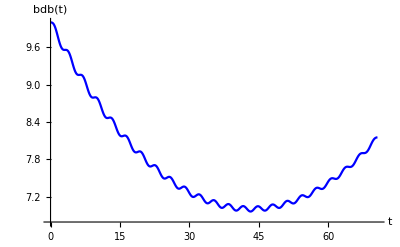

```mathematica
pbbb0p5=ListPlot[data0p5, AxesLabel->{"t","bdb(t)"},Joined->True,PlotStyle->{Blue}]
```

## Average cooling starting from a coherent state of mean quanta n̄=10, with Δϕ=0.4ϕ_p, theory predictions.

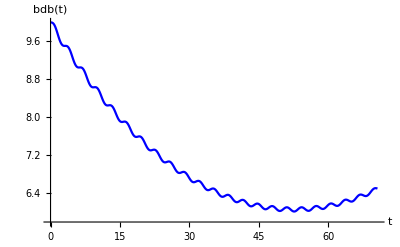

```mathematica
pbbb0p4=ListPlot[data0p4, AxesLabel->{"t","bdb(t)"},Joined->True,PlotStyle->{Blue}]
```

## Average cooling starting from a coherent state of mean quanta n̄=10, with Δϕ=0.3ϕ_p, theory predictions.

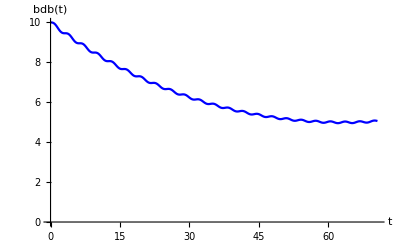

```mathematica
pbbb0p3=ListPlot[data0p3, AxesLabel->{"t","bdb(t)"},Joined->True,PlotStyle->{Blue}]
```

## Average cooling starting from a coherent state of mean quanta n̄=10, with Δϕ=0.2ϕ_p, theory predictions.

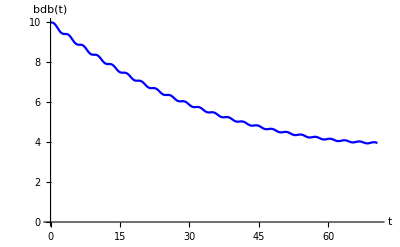

```mathematica
pbbb0p2=ListPlot[data0p2, AxesLabel->{"t","bdb(t)"},Joined->True,PlotStyle->{Blue}]
```

## Average cooling starting from a coherent state of mean quanta n̄=10, with Δϕ=0.1ϕ_p, theory predictions.

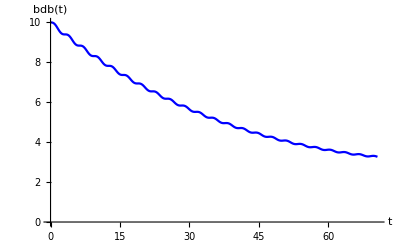

```mathematica
pbbb0p1=ListPlot[data0p1, AxesLabel->{"t","bdb(t)"},Joined->True,PlotStyle->{Blue}]
```

## Average cooling starting from a coherent state of mean quanta n̄=10, with Δϕ=0, theory predictions.

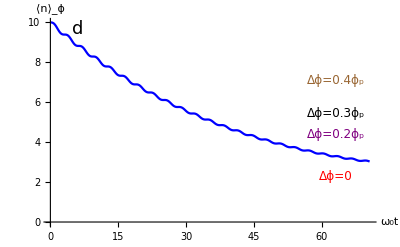

```mathematica
pbbb0=ListPlot[data0,Joined->True,PlotStyle->{Blue},BaseStyle->{FontSize->16,Black},AxesLabel->{Style["ω_0t",Black,18],Style["⟨n⟩_ϕ",Black,18]},TicksStyle->Directive[Black],Epilog->{{Inset[Style["Δϕ=0.4ϕ_p",12,Brown],Scaled[{0.88,0.7}]]},{Inset[Style["Δϕ=0.3ϕ_p",12,Black],Scaled[{0.88,0.54}]]},{Inset[Style["Δϕ=0.2ϕ_p",12,Purple],Scaled[{0.88,0.44}]]},{Inset[Style["Δϕ=0",12,Red],Scaled[{0.88,0.24}]]},{Inset[Style["d",18,Black],Scaled[{0.1,0.95}]]}}]
```

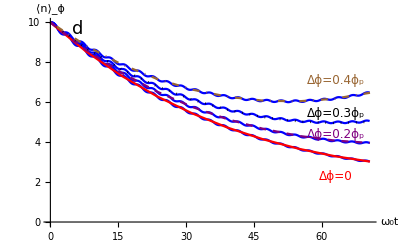

```mathematica
pisa=Show[pbbb0,pbbb0p2,pbbb0p3,pbbb0p4,psafa0,psafa0p2,psafa0p3,psafa0p4]
```

## 5. The following command generates Fig. 2 in the article. Please refer to caption of Fig. 2 for a detailed summary.

```mathematica
pmaha=GraphicsGrid[{{plta,paaaaaa},{pbb,pisa}},Spacings->{0,0},ImageSize->800];
```